```mathematica
translate[codon_]:=Which[codon=="GCT"||codon=="GCC"||codon=="GCA"||codon=="GCG","A",codon=="CGT"||codon=="CGC"||codon=="CGA"||codon=="CGG"||codon=="AGA"||codon=="AGG","R",codon=="AAC"||codon=="AAT","N",codon=="GAT"||codon=="GAC","D",codon=="TGT"||codon=="TGC","C",codon=="CAA"||codon=="CAG","Q",codon=="GAA"||codon=="GAG","E",codon=="GGT"||codon=="GGC"||codon=="GGA"||codon=="GGG","G",codon=="CAT"||codon=="CAC","H",codon=="ATT"||codon=="ATC"||codon=="ATA","I",codon=="TTA"||codon=="TTG"||codon=="CTT"||codon=="CTC"||codon=="CTA"||codon=="CTG","L",codon=="AAA"||codon=="AAG","K",codon=="ATG","M",codon=="TTT"||codon=="TTC","F",codon=="CCT"||codon=="CCC"||codon=="CCA"||codon=="CCG","P",codon=="TCT"||codon=="TCC"||codon=="TCA"||codon=="TCG"||codon=="AGT"||codon=="AGC","S",codon=="ACT"||codon=="ACC"||codon=="ACA"||codon=="ACG","T",codon=="TGG","W",codon=="TAT"||codon=="TAC","Y",codon=="GTT"||codon=="GTC"||codon=="GTA"||codon=="GTG","V"]

getcomplement[base_]:=Which[base=="G","C",base=="C","G",base=="T","A",base=="A","T"]

reversecomplement[sequence_]:=Module[{temp1,complement},

temp1=Characters[sequence];

complement=Table[getcomplement[temp1[[i]]],{i,1,Length[temp1]}];

StringJoin[Reverse[complement]]

]

primerparams[sequence_,annealingportion_,mismatch_]:=Module[{n,g,c,gc},

n=StringLength[sequence];

g=StringCount[sequence,"G"];

c=StringCount[sequence,"C"];

gc=(g+c)/n*100.0;

(*Print[TableForm[{{"Length","%GC","Tm"},{n,gc,81.5+0.41*gc-(675.0/n)-mismatch/42*100.}}]];*)

{n,gc,81.5+0.41*gc-(675.0/n)-mismatch/42*100.}

]

Tmscore[Tm_]:=Piecewise[{{2,Tm≥78.0&&Tm<82.0},{(Tm-77.0)+1,Tm<78.0},{-1*(Tm-82.0)+2,Tm≥82.0}}]
```

### Open an external Python process to calculate hairpin Tms

```mathematica
Tmcounter=0;

pythonpath=StartProcess[{path,"-i"}];

cmd="import primer3";
Pause[0.001];
WriteLine[pythonpath,cmd];

calcHairpin[sequence_]:=(

Tmcounternew=Tmcounter+1;

path="/Library/Frameworks/Python.framework/Versions/2.7/bin/python";

If[Tmcounternew==500,

(KillProcess[pythonpath];

pythonpath=StartProcess[{path,"-i"}];

cmd="import primer3";
Pause[0.001];
WriteLine[pythonpath,cmd];

Tmcounternew=0)];

cmd=StringJoin["primer3.calcHairpin('",sequence,"').tm"];
Pause[0.001];

WriteLine[pythonpath,cmd];

Pause[0.05];

out=ReadString[pythonpath,EndOfBuffer];

Tmcounter=Tmcounternew;

out)
```

```mathematica
calcHairpin["GCACATTCTGTGGGCTTTGGGCAAGCACATAAAATGCC"]
```

58.19360163176441

```mathematica
alanine={"GCT","GCC","GCA","GCG"};

arginine={"CGT","CGC","CGA","CGG","AGA","AGG"};

asparagine={"AAC","AAT","TAA"};

aspartate={"GAT","GAC"};

cysteine={"TGT","TGC"};

glutamine={"CAA","CAG"};

glutamate={"GAA","GAG"};

glycine={"GGT","GGC","GGA","GGG"};

histidine={"CAT","CAC"};

isoleucine={"ATT","ATC","ATA"};

leucine={"TTA","TTG","CTT","CTC","CTA","CTG"};

lysine={"AAA","AAG"};

methionine={"ATG"};

phenylalanine={"TTT","TTC"};

proline={"CCT","CCC","CCA","CCG"};

serine={"TCT","TCC","TCA","TCG","AGT","AGC"};

threonine={"ACT","ACC","ACA","ACG"};

tryptophan={"TGG"};

tyrosine={"TAT","TAC"};

valine={"GTT","GTC","GTA","GTG"};
```

```mathematica
pafAsequence="AGAAATAATTTTGTTTAACTTTAAGAAGGAGATATACATATGCAAAAAACGAATGCTGTACCAAGACCTAAACTTGTGGTAGGACTGGTAGTTGATCAGATGAGATGGGATTATCTTTACCGTTATTATAGCAAGTATGGTGAAGGAGGTTTTAAGAGAATGCTGAATACCGGGTATTCGTTAAATAATGTTCATATAGACTATGTACCTACAGTAACTGCAATCGGACATACTTCAATTTTTACAGGTTCTGTTCCCTCCATCCACGGAATTGCAGGAAACGATTGGTATGATAAAGAATTAGGGAAAAGTGTTTACTGTACATCTGATGAAACAGTACAACCGGTAGGAACTACTTCTAACTCGGTTGGACAACATTCACCAAGAAACCTTTGGTCTACTACGGTAACAGATCAGCTAGGTTTGGCAACAAACTTTACTTCTAAGGTTGTGGGGGTCTCTCTGAAAGACAGAGCATCAATTCTGCCTGCAGGGCACAACCCAACAGGAGCATTTTGGTTCGATGATACTACAGGTAAATTCATTACCAGTACATATTATACTAAAGAATTACCTAAATGGGTAAACGACTTTAATAATAAAAATGTTCCGGCTCAGTTGGTAGCTAATGGCTGGAATACACTATTGCCCATTAATCAGTATACAGAAAGCTCAGAAGATAATGTGGAATGGGAAGGTTTATTAGGGAGTAAAAAAACACCTACATTCCCTTATACAGATCTGGCTAAAGATTATGAAGCTAAAAAAGGATTAATCCGTACTACACCATTTGGAAATACCTTAACTCTTCAGATGGCAGATGCTGCAATTGATGGTAACCAAATGGGAGTTGATGATATTACTGACTTCCTTACAGTAAACCTTGCTTCAACGGATTATGTTGGACACAACTTTGGTCCAAACTCTATAGAAGTTGAGGATACTTATCTGAGATTAGACAGAGATTTGGCTGACTTCTTCAATAACCTTGATAAAAAAGTTGGAAAAGGAAACTACCTTGTATTCCTTTCTGCGGATCATGGCGCTGCACATTCTGTGGGCTTTATGCAAGCACATAAAATGCCAACAGGCTTCTTTGTAGAAGATATGAAAAAAGAAATGAACGCTAAGCTGAAGCAAAAATTCGGTGCTGATAATATAATTGCAGCTGCGATGAACTATCAGGTTTATTTCGACAGAAAGGTTTTAGCAGACAGCAAATTAGAATTGGATGACGTAAGAGATTATGTAATGACAGAACTTAAAAAAGAGCCATCAGTTCTTTATGTTCTTAGCACGGATGAAATCTGGGAATCGTCTATTCCGGAACCGATAAAGTCCAGAGTAATCAATGGTTATAACTGGAAAAGAAGCGGAGATATTCAGATCATTTCTAAAGACGGATATCTTTCAGCATATTCCAAAAAAGGGACAACACACAGTGTATGGAACTCTTATGATTCACATATTCCTTTACTCTTTATGGGGTGGGGTATCAAACAGGGAGAGTCCAATCAGCCATACCATATGACGGATATTGCACCAACTGTTTCATCATTACTTAAAATTCAGTTCCCTAGTGGTGCTGTAGGTAAACCAATTACCGAAGTTATAGGAAGAGGAGGAGGGTCTGGGGGAGGAGGCAGTGGCATGGTGAGCAAG";

pafAcodons=Partition[Characters[pafAsequence],3];
```

```mathematica
(* translate *)

translation=Table[{i,StringJoin["Res ",ToString[i*3-2]],StringJoin[pafAcodons[[i]]],Style[translate[StringJoin[pafAcodons[[i]]]],Bold]},{i,1,Length[pafAcodons]}]
```

{{1,Res 1,AGA,R},{2,Res 4,AAT,N},{3,Res 7,AAT,N},{4,Res 10,TTT,F},{5,Res 13,GTT,V},{6,Res 16,TAA,Null},{7,Res 19,CTT,L},{8,Res 22,TAA,Null},{9,Res 25,GAA,E},{10,Res 28,GGA,G},{11,Res 31,GAT,D},{12,Res 34,ATA,I},{13,Res 37,CAT,H},{14,Res 40,ATG,M},{15,Res 43,CAA,Q},{16,Res 46,AAA,K},{17,Res 49,ACG,T},{18,Res 52,AAT,N},{19,Res 55,GCT,A},{20,Res 58,GTA,V},{21,Res 61,CCA,P},{22,Res 64,AGA,R},{23,Res 67,CCT,P},{24,Res 70,AAA,K},{25,Res 73,CTT,L},{26,Res 76,GTG,V},{27,Res 79,GTA,V},{28,Res 82,GGA,G},{29,Res 85,CTG,L},{30,Res 88,GTA,V},{31,Res 91,GTT,V},{32,Res 94,GAT,D},{33,Res 97,CAG,Q},{34,Res 100,ATG,M},{35,Res 103,AGA,R},{36,Res 106,TGG,W},{37,Res 109,GAT,D},{38,Res 112,TAT,Y},{39,Res 115,CTT,L},{40,Res 118,TAC,Y},{41,Res 121,CGT,R},{42,Res 124,TAT,Y},{43,Res 127,TAT,Y},{44,Res 130,AGC,S},{45,Res 133,AAG,K},{46,Res 136,TAT,Y},{47,Res 139,GGT,G},{48,Res 142,GAA,E},{49,Res 145,GGA,G},{50,Res 148,GGT,G},{51,Res 151,TTT,F},{52,Res 154,AAG,K},{53,Res 157,AGA,R},{54,Res 160,ATG,M},{55,Res 163,CTG,L},{56,Res 166,AAT,N},{57,Res 169,ACC,T},{58,Res 172,GGG,G},{59,Res 175,TAT,Y},{60,Res 178,TCG,S},{61,Res 181,TTA,L},{62,Res 184,AAT,N},{63,Res 187,AAT,N},{64,Res 190,GTT,V},{65,Res 193,CAT,H},{66,Res 196,ATA,I},{67,Res 199,GAC,D},{68,Res 202,TAT,Y},{69,Res 205,GTA,V},{70,Res 208,CCT,P},{71,Res 211,ACA,T},{72,Res 214,GTA,V},{73,Res 217,ACT,T},{74,Res 220,GCA,A},{75,Res 223,ATC,I},{76,Res 226,GGA,G},{77,Res 229,CAT,H},{78,Res 232,ACT,T},{79,Res 235,TCA,S},{80,Res 238,ATT,I},{81,Res 241,TTT,F},{82,Res 244,ACA,T},{83,Res 247,GGT,G},{84,Res 250,TCT,S},{85,Res 253,GTT,V},{86,Res 256,CCC,P},{87,Res 259,TCC,S},{88,Res 262,ATC,I},{89,Res 265,CAC,H},{90,Res 268,GGA,G},{91,Res 271,ATT,I},{92,Res 274,GCA,A},{93,Res 277,GGA,G},{94,Res 280,AAC,N},{95,Res 283,GAT,D},{96,Res 286,TGG,W},{97,Res 289,TAT,Y},{98,Res 292,GAT,D},{99,Res 295,AAA,K},{100,Res 298,GAA,E},{101,Res 301,TTA,L},{102,Res 304,GGG,G},{103,Res 307,AAA,K},{104,Res 310,AGT,S},{105,Res 313,GTT,V},{106,Res 316,TAC,Y},{107,Res 319,TGT,C},{108,Res 322,ACA,T},{109,Res 325,TCT,S},{110,Res 328,GAT,D},{111,Res 331,GAA,E},{112,Res 334,ACA,T},{113,Res 337,GTA,V},{114,Res 340,CAA,Q},{115,Res 343,CCG,P},{116,Res 346,GTA,V},{117,Res 349,GGA,G},{118,Res 352,ACT,T},{119,Res 355,ACT,T},{120,Res 358,TCT,S},{121,Res 361,AAC,N},{122,Res 364,TCG,S},{123,Res 367,GTT,V},{124,Res 370,GGA,G},{125,Res 373,CAA,Q},{126,Res 376,CAT,H},{127,Res 379,TCA,S},{128,Res 382,CCA,P},{129,Res 385,AGA,R},{130,Res 388,AAC,N},{131,Res 391,CTT,L},{132,Res 394,TGG,W},{133,Res 397,TCT,S},{134,Res 400,ACT,T},{135,Res 403,ACG,T},{136,Res 406,GTA,V},{137,Res 409,ACA,T},{138,Res 412,GAT,D},{139,Res 415,CAG,Q},{140,Res 418,CTA,L},{141,Res 421,GGT,G},{142,Res 424,TTG,L},{143,Res 427,GCA,A},{144,Res 430,ACA,T},{145,Res 433,AAC,N},{146,Res 436,TTT,F},{147,Res 439,ACT,T},{148,Res 442,TCT,S},{149,Res 445,AAG,K},{150,Res 448,GTT,V},{151,Res 451,GTG,V},{152,Res 454,GGG,G},{153,Res 457,GTC,V},{154,Res 460,TCT,S},{155,Res 463,CTG,L},{156,Res 466,AAA,K},{157,Res 469,GAC,D},{158,Res 472,AGA,R},{159,Res 475,GCA,A},{160,Res 478,TCA,S},{161,Res 481,ATT,I},{162,Res 484,CTG,L},{163,Res 487,CCT,P},{164,Res 490,GCA,A},{165,Res 493,GGG,G},{166,Res 496,CAC,H},{167,Res 499,AAC,N},{168,Res 502,CCA,P},{169,Res 505,ACA,T},{170,Res 508,GGA,G},{171,Res 511,GCA,A},{172,Res 514,TTT,F},{173,Res 517,TGG,W},{174,Res 520,TTC,F},{175,Res 523,GAT,D},{176,Res 526,GAT,D},{177,Res 529,ACT,T},{178,Res 532,ACA,T},{179,Res 535,GGT,G},{180,Res 538,AAA,K},{181,Res 541,TTC,F},{182,Res 544,ATT,I},{183,Res 547,ACC,T},{184,Res 550,AGT,S},{185,Res 553,ACA,T},{186,Res 556,TAT,Y},{187,Res 559,TAT,Y},{188,Res 562,ACT,T},{189,Res 565,AAA,K},{190,Res 568,GAA,E},{191,Res 571,TTA,L},{192,Res 574,CCT,P},{193,Res 577,AAA,K},{194,Res 580,TGG,W},{195,Res 583,GTA,V},{196,Res 586,AAC,N},{197,Res 589,GAC,D},{198,Res 592,TTT,F},{199,Res 595,AAT,N},{200,Res 598,AAT,N},{201,Res 601,AAA,K},{202,Res 604,AAT,N},{203,Res 607,GTT,V},{204,Res 610,CCG,P},{205,Res 613,GCT,A},{206,Res 616,CAG,Q},{207,Res 619,TTG,L},{208,Res 622,GTA,V},{209,Res 625,GCT,A},{210,Res 628,AAT,N},{211,Res 631,GGC,G},{212,Res 634,TGG,W},{213,Res 637,AAT,N},{214,Res 640,ACA,T},{215,Res 643,CTA,L},{216,Res 646,TTG,L},{217,Res 649,CCC,P},{218,Res 652,ATT,I},{219,Res 655,AAT,N},{220,Res 658,CAG,Q},{221,Res 661,TAT,Y},{222,Res 664,ACA,T},{223,Res 667,GAA,E},{224,Res 670,AGC,S},{225,Res 673,TCA,S},{226,Res 676,GAA,E},{227,Res 679,GAT,D},{228,Res 682,AAT,N},{229,Res 685,GTG,V},{230,Res 688,GAA,E},{231,Res 691,TGG,W},{232,Res 694,GAA,E},{233,Res 697,GGT,G},{234,Res 700,TTA,L},{235,Res 703,TTA,L},{236,Res 706,GGG,G},{237,Res 709,AGT,S},{238,Res 712,AAA,K},{239,Res 715,AAA,K},{240,Res 718,ACA,T},{241,Res 721,CCT,P},{242,Res 724,ACA,T},{243,Res 727,TTC,F},{244,Res 730,CCT,P},{245,Res 733,TAT,Y},{246,Res 736,ACA,T},{247,Res 739,GAT,D},{248,Res 742,CTG,L},{249,Res 745,GCT,A},{250,Res 748,AAA,K},{251,Res 751,GAT,D},{252,Res 754,TAT,Y},{253,Res 757,GAA,E},{254,Res 760,GCT,A},{255,Res 763,AAA,K},{256,Res 766,AAA,K},{257,Res 769,GGA,G},{258,Res 772,TTA,L},{259,Res 775,ATC,I},{260,Res 778,CGT,R},{261,Res 781,ACT,T},{262,Res 784,ACA,T},{263,Res 787,CCA,P},{264,Res 790,TTT,F},{265,Res 793,GGA,G},{266,Res 796,AAT,N},{267,Res 799,ACC,T},{268,Res 802,TTA,L},{269,Res 805,ACT,T},{270,Res 808,CTT,L},{271,Res 811,CAG,Q},{272,Res 814,ATG,M},{273,Res 817,GCA,A},{274,Res 820,GAT,D},{275,Res 823,GCT,A},{276,Res 826,GCA,A},{277,Res 829,ATT,I},{278,Res 832,GAT,D},{279,Res 835,GGT,G},{280,Res 838,AAC,N},{281,Res 841,CAA,Q},{282,Res 844,ATG,M},{283,Res 847,GGA,G},{284,Res 850,GTT,V},{285,Res 853,GAT,D},{286,Res 856,GAT,D},{287,Res 859,ATT,I},{288,Res 862,ACT,T},{289,Res 865,GAC,D},{290,Res 868,TTC,F},{291,Res 871,CTT,L},{292,Res 874,ACA,T},{293,Res 877,GTA,V},{294,Res 880,AAC,N},{295,Res 883,CTT,L},{296,Res 886,GCT,A},{297,Res 889,TCA,S},{298,Res 892,ACG,T},{299,Res 895,GAT,D},{300,Res 898,TAT,Y},{301,Res 901,GTT,V},{302,Res 904,GGA,G},{303,Res 907,CAC,H},{304,Res 910,AAC,N},{305,Res 913,TTT,F},{306,Res 916,GGT,G},{307,Res 919,CCA,P},{308,Res 922,AAC,N},{309,Res 925,TCT,S},{310,Res 928,ATA,I},{311,Res 931,GAA,E},{312,Res 934,GTT,V},{313,Res 937,GAG,E},{314,Res 940,GAT,D},{315,Res 943,ACT,T},{316,Res 946,TAT,Y},{317,Res 949,CTG,L},{318,Res 952,AGA,R},{319,Res 955,TTA,L},{320,Res 958,GAC,D},{321,Res 961,AGA,R},{322,Res 964,GAT,D},{323,Res 967,TTG,L},{324,Res 970,GCT,A},{325,Res 973,GAC,D},{326,Res 976,TTC,F},{327,Res 979,TTC,F},{328,Res 982,AAT,N},{329,Res 985,AAC,N},{330,Res 988,CTT,L},{331,Res 991,GAT,D},{332,Res 994,AAA,K},{333,Res 997,AAA,K},{334,Res 1000,GTT,V},{335,Res 1003,GGA,G},{336,Res 1006,AAA,K},{337,Res 1009,GGA,G},{338,Res 1012,AAC,N},{339,Res 1015,TAC,Y},{340,Res 1018,CTT,L},{341,Res 1021,GTA,V},{342,Res 1024,TTC,F},{343,Res 1027,CTT,L},{344,Res 1030,TCT,S},{345,Res 1033,GCG,A},{346,Res 1036,GAT,D},{347,Res 1039,CAT,H},{348,Res 1042,GGC,G},{349,Res 1045,GCT,A},{350,Res 1048,GCA,A},{351,Res 1051,CAT,H},{352,Res 1054,TCT,S},{353,Res 1057,GTG,V},{354,Res 1060,GGC,G},{355,Res 1063,TTT,F},{356,Res 1066,ATG,M},{357,Res 1069,CAA,Q},{358,Res 1072,GCA,A},{359,Res 1075,CAT,H},{360,Res 1078,AAA,K},{361,Res 1081,ATG,M},{362,Res 1084,CCA,P},{363,Res 1087,ACA,T},{364,Res 1090,GGC,G},{365,Res 1093,TTC,F},{366,Res 1096,TTT,F},{367,Res 1099,GTA,V},{368,Res 1102,GAA,E},{369,Res 1105,GAT,D},{370,Res 1108,ATG,M},{371,Res 1111,AAA,K},{372,Res 1114,AAA,K},{373,Res 1117,GAA,E},{374,Res 1120,ATG,M},{375,Res 1123,AAC,N},{376,Res 1126,GCT,A},{377,Res 1129,AAG,K},{378,Res 1132,CTG,L},{379,Res 1135,AAG,K},{380,Res 1138,CAA,Q},{381,Res 1141,AAA,K},{382,Res 1144,TTC,F},{383,Res 1147,GGT,G},{384,Res 1150,GCT,A},{385,Res 1153,GAT,D},{386,Res 1156,AAT,N},{387,Res 1159,ATA,I},{388,Res 1162,ATT,I},{389,Res 1165,GCA,A},{390,Res 1168,GCT,A},{391,Res 1171,GCG,A},{392,Res 1174,ATG,M},{393,Res 1177,AAC,N},{394,Res 1180,TAT,Y},{395,Res 1183,CAG,Q},{396,Res 1186,GTT,V},{397,Res 1189,TAT,Y},{398,Res 1192,TTC,F},{399,Res 1195,GAC,D},{400,Res 1198,AGA,R},{401,Res 1201,AAG,K},{402,Res 1204,GTT,V},{403,Res 1207,TTA,L},{404,Res 1210,GCA,A},{405,Res 1213,GAC,D},{406,Res 1216,AGC,S},{407,Res 1219,AAA,K},{408,Res 1222,TTA,L},{409,Res 1225,GAA,E},{410,Res 1228,TTG,L},{411,Res 1231,GAT,D},{412,Res 1234,GAC,D},{413,Res 1237,GTA,V},{414,Res 1240,AGA,R},{415,Res 1243,GAT,D},{416,Res 1246,TAT,Y},{417,Res 1249,GTA,V},{418,Res 1252,ATG,M},{419,Res 1255,ACA,T},{420,Res 1258,GAA,E},{421,Res 1261,CTT,L},{422,Res 1264,AAA,K},{423,Res 1267,AAA,K},{424,Res 1270,GAG,E},{425,Res 1273,CCA,P},{426,Res 1276,TCA,S},{427,Res 1279,GTT,V},{428,Res 1282,CTT,L},{429,Res 1285,TAT,Y},{430,Res 1288,GTT,V},{431,Res 1291,CTT,L},{432,Res 1294,AGC,S},{433,Res 1297,ACG,T},{434,Res 1300,GAT,D},{435,Res 1303,GAA,E},{436,Res 1306,ATC,I},{437,Res 1309,TGG,W},{438,Res 1312,GAA,E},{439,Res 1315,TCG,S},{440,Res 1318,TCT,S},{441,Res 1321,ATT,I},{442,Res 1324,CCG,P},{443,Res 1327,GAA,E},{444,Res 1330,CCG,P},{445,Res 1333,ATA,I},{446,Res 1336,AAG,K},{447,Res 1339,TCC,S},{448,Res 1342,AGA,R},{449,Res 1345,GTA,V},{450,Res 1348,ATC,I},{451,Res 1351,AAT,N},{452,Res 1354,GGT,G},{453,Res 1357,TAT,Y},{454,Res 1360,AAC,N},{455,Res 1363,TGG,W},{456,Res 1366,AAA,K},{457,Res 1369,AGA,R},{458,Res 1372,AGC,S},{459,Res 1375,GGA,G},{460,Res 1378,GAT,D},{461,Res 1381,ATT,I},{462,Res 1384,CAG,Q},{463,Res 1387,ATC,I},{464,Res 1390,ATT,I},{465,Res 1393,TCT,S},{466,Res 1396,AAA,K},{467,Res 1399,GAC,D},{468,Res 1402,GGA,G},{469,Res 1405,TAT,Y},{470,Res 1408,CTT,L},{471,Res 1411,TCA,S},{472,Res 1414,GCA,A},{473,Res 1417,TAT,Y},{474,Res 1420,TCC,S},{475,Res 1423,AAA,K},{476,Res 1426,AAA,K},{477,Res 1429,GGG,G},{478,Res 1432,ACA,T},{479,Res 1435,ACA,T},{480,Res 1438,CAC,H},{481,Res 1441,AGT,S},{482,Res 1444,GTA,V},{483,Res 1447,TGG,W},{484,Res 1450,AAC,N},{485,Res 1453,TCT,S},{486,Res 1456,TAT,Y},{487,Res 1459,GAT,D},{488,Res 1462,TCA,S},{489,Res 1465,CAT,H},{490,Res 1468,ATT,I},{491,Res 1471,CCT,P},{492,Res 1474,TTA,L},{493,Res 1477,CTC,L},{494,Res 1480,TTT,F},{495,Res 1483,ATG,M},{496,Res 1486,GGG,G},{497,Res 1489,TGG,W},{498,Res 1492,GGT,G},{499,Res 1495,ATC,I},{500,Res 1498,AAA,K},{501,Res 1501,CAG,Q},{502,Res 1504,GGA,G},{503,Res 1507,GAG,E},{504,Res 1510,TCC,S},{505,Res 1513,AAT,N},{506,Res 1516,CAG,Q},{507,Res 1519,CCA,P},{508,Res 1522,TAC,Y},{509,Res 1525,CAT,H},{510,Res 1528,ATG,M},{511,Res 1531,ACG,T},{512,Res 1534,GAT,D},{513,Res 1537,ATT,I},{514,Res 1540,GCA,A},{515,Res 1543,CCA,P},{516,Res 1546,ACT,T},{517,Res 1549,GTT,V},{518,Res 1552,TCA,S},{519,Res 1555,TCA,S},{520,Res 1558,TTA,L},{521,Res 1561,CTT,L},{522,Res 1564,AAA,K},{523,Res 1567,ATT,I},{524,Res 1570,CAG,Q},{525,Res 1573,TTC,F},{526,Res 1576,CCT,P},{527,Res 1579,AGT,S},{528,Res 1582,GGT,G},{529,Res 1585,GCT,A},{530,Res 1588,GTA,V},{531,Res 1591,GGT,G},{532,Res 1594,AAA,K},{533,Res 1597,CCA,P},{534,Res 1600,ATT,I},{535,Res 1603,ACC,T},{536,Res 1606,GAA,E},{537,Res 1609,GTT,V},{538,Res 1612,ATA,I},{539,Res 1615,GGA,G},{540,Res 1618,AGA,R},{541,Res 1621,GGA,G},{542,Res 1624,GGA,G},{543,Res 1627,GGG,G},{544,Res 1630,TCT,S},{545,Res 1633,GGG,G},{546,Res 1636,GGA,G},{547,Res 1639,GGA,G},{548,Res 1642,GGC,G},{549,Res 1645,AGT,S},{550,Res 1648,GGC,G},{551,Res 1651,ATG,M},{552,Res 1654,GTG,V},{553,Res 1657,AGC,S},{554,Res 1660,AAG,K}}

```mathematica
mutation={"Q15G","K16G","T17G","N18G","A19G","V20G","P21G","R22G","P23G","K24G","L25G","V26G","V27G","G28A","L29G","V30G","V31G","D32G","Q33G","M34G","R35G","W36G","D37G","Y38G","L39G","Y40G","R41G","Y42G","Y43G","S44G","K45G","Y46G","G47A","E48G","G49A","G50A","F51G","K52G","R53G","M54G","L55G","N56G","T57G","G58A","Y59G","S60G","L61G","N62G","N63G","V64G","H65G","I66G","D67G","Y68G","V69G","P70G","T71G","V72G","T73G","A74G","I75G","G76A","H77G","T78G","S79G","I80G","F81G","T82G","G83A","S84G","V85G","P86G","S87G","I88G","H89G","G90A","I91G","A92G","G93A","N94G","D95G","W96G","Y97G","D98G","K99G","E100G","L101G","G102A","K103G","S104G","V105G","Y106G","C107G","T108G","S109G","D110G","E111G","T112G","V113G","Q114G","P115G","V116G","G117A","T118G","T119G","S120G","N121G","S122G","V123G","G124A","Q125G","H126G","S127G","P128G","R129G","N130G","L131G","W132G","S133G","T134G","T135G","V136G","T137G","D138G","Q139G","L140G","G141A","L142G","A143G","T144G","N145G","F146G","T147G","S148G","K149G","V150G","V151G","G152A","V153G","S154G","L155G","K156G","D157G","R158G","A159G","S160G","I161G","L162G","P163G","A164G","G165A","H166G","N167G","P168G","T169G","G170A","A171G","F172G","W173G","F174G","D175G","D176G","T177G","T178G","G179A","K180G","F181G","I182G","T183G","S184G","T185G","Y186G","Y187G","T188G","K189G","E190G","L191G","P192G","K193G","W194G","V195G","N196G","D197G","F198G","N199G","N200G","K201G","N202G","V203G","P204G","A205G","Q206G","L207G","V208G","A209G","N210G","G211A","W212G","N213G","T214G","L215G","L216G","P217G","I218G","N219G","Q220G","Y221G","T222G","E223G","S224G","S225G","E226G","D227G","N228G","V229G","E230G","W231G","E232G","G233A","L234G","L235G","G236A","S237G","K238G","K239G","T240G","P241G","T242G","F243G","P244G","Y245G","T246G","D247G","L248G","A249G","K250G","D251G","Y252G","E253G","A254G","K255G","K256G","G257A","L258G","I259G","R260G","T261G","T262G","P263G","F264G","G265A","N266G","T267G","L268G","T269G","L270G","Q271G","M272G","A273G","D274G","A275G","A276G","I277G","D278G","G279A","N280G","Q281G","M282G","G283A","V284G","D285G","D286G","I287G","T288G","D289G","F290G","L291G","T292G","V293G","N294G","L295G","A296G","S297G","T298G","D299G","Y300G","V301G","G302A","H303G","N304G","F305G","G306A","P307G","N308G","S309G","I310G","E311G","V312G","E313G","D314G","T315G","Y316G","L317G","R318G","L319G","D320G","R321G","D322G","L323G","A324G","D325G","F326G","F327G","N328G","N329G","L330G","D331G","K332G","K333G","V334G","G335A","K336G","G337A","N338G","Y339G","L340G","V341G","F342G","L343G","S344G","A345G","D346G","H347G","G348A","A349G","A350G","H351G","S352G","V353G","G354A","F355G","M356G","Q357G","A358G","H359G","K360G","M361G","P362G","T363G","G364A","F365G","F366G","V367G","E368G","D369G","M370G","K371G","K372G","E373G","M374G","N375G","A376G","K377G","L378G","K379G","Q380G","K381G","F382G","G383A","A384G","D385G","N386G","I387G","I388G","A389G","A390G","A391G","M392G","N393G","Y394G","Q395G","V396G","Y397G","F398G","D399G","R400G","K401G","V402G","L403G","A404G","D405G","S406G","K407G","L408G","E409G","L410G","D411G","D412G","V413G","R414G","D415G","Y416G","V417G","M418G","T419G","E420G","L421G","K422G","K423G","E424G","P425G","S426G","V427G","L428G","Y429G","V430G","L431G","S432G","T433G","D434G","E435G","I436G","W437G","E438G","S439G","S440G","I441G","P442G","E443G","P444G","I445G","K446G","S447G","R448G","V449G","I450G","N451G","G452A","Y453G","N454G","W455G","K456G","R457G","S458G","G459A","D460G","I461G","Q462G","I463G","I464G","S465G","K466G","D467G","G468A","Y469G","L470G","S471G","A472G","Y473G","S474G","K475G","K476G","G477A","T478G","T479G","H480G","S481G","V482G","W483G","N484G","S485G","Y486G","D487G","S488G","H489G","I490G","P491G","L492G","L493G","F494G","M495G","G496A","W497G","G498A","I499G","K500G","Q501G","G502A","E503G","S504G","N505G","Q506G","P507G","Y508G","H509G","M510G","T511G","D512G","I513G","A514G","P515G","T516G","V517G","S518G","S519G","L520G","L521G","K522G","I523G","Q524G","F525G","P526G","S527G","G528A","A529G","V530G","G531A","K532G","P533G","I534G","T535G","E536G","V537G","I538G","G539A","R540G"};
```

```mathematica
Length[mutation]
```

526

```mathematica
Dynamic[loop]
Dynamic[i]

Do[

resnumber=ToExpression[StringDrop[StringDrop[mutation[[loop]],{1}],{-1}]];

restypeIN=StringTake[mutation[[loop]],{-1}];

(* calculate the number of base pair changes between the wild-type sequence and all codons of the mutated amino acid *)
newrescodons=Which[restypeIN=="A",alanine,restypeIN=="G",glycine,restypeIN=="D",aspartate,restypeIN=="N",asparagine,restypeIN=="E",glutamate,restypeIN=="Q",glutamine,restypeIN=="V",valine,restypeIN=="L",leucine,restypeIN=="I",isoleucine,restypeIN=="P",proline,restypeIN=="H",histidine,restypeIN=="K",lysine,restypeIN=="R",arginine,restypeIN=="Y",tyrosine,restypeIN=="F",phenylalanine,restypeIN=="W",tryptophan,restypeIN=="S",serine,restypeIN=="T",threonine,restypeIN=="C",cysteine,restypeIN=="M",methionine];

testwt=pafAcodons[[resnumber]];
(*Print[testwt];

Print[translation[[resnumber]]];*)

Do[

testmutant=Characters[newrescodons[[i]]];

codondiff[i]=If[testwt[[1]]==testmutant[[1]],0,1]+If[testwt[[2]]==testmutant[[2]],0,1]+If[testwt[[3]]==testmutant[[3]],0,1];

,{i,1,Length[newrescodons]}];

(* select codon requiring the least number of base pair changes *)
newcodon=Sort[Table[{StringJoin[newrescodons[[i]]],codondiff[i]},{i,1,Length[newrescodons]}],#1[[2]]<#2[[2]]&][[1]];

(*Print["New codon"];
Print[newcodon];*)

(* test a range of flanking lengths *)
base5prime=resnumber*3-2;
base3prime=resnumber*3;

(* below plots the piecewise function used by Tmscore *)
(* Plot[Piecewise[{{2,Tm≥78.0},{(Tm-77.0)+1,Tm≥77.0},{(Tm-70.0)*0.142857,Tm<77.0}}],{Tm,70,85}] *)

(* counter for indexing the mutagenic primers *)
counter=0;

Do[

Do[

fiveprimeend=base5prime-i;
threeprimeend=base3prime+j;

wildtypeprimer=StringTake[pafAsequence,{fiveprimeend,threeprimeend}];

(* insert mutation into sense primer *)
mutagenicprimer=StringJoin[StringTake[pafAsequence,{fiveprimeend,base5prime-1}],StringJoin[newcodon[[1]]],StringTake[pafAsequence,{base3prime+1,threeprimeend}]];

gcfirst=If[StringTake[mutagenicprimer,1]=="G"||StringTake[mutagenicprimer,1]=="C",1,0];

gclast=If[StringTake[mutagenicprimer,-1]=="G"||StringTake[mutagenicprimer,-1]=="C",1,0];

(* calculate the annealing portion of the sequence for Tm calcuations *)
wtseq=Characters[wildtypeprimer];
mutantseq=Characters[mutagenicprimer];

seqforTm=StringJoin[Select[Table[If[wtseq[[i]]==mutantseq[[i]],wtseq[[i]]],{i,1,Length[wtseq]}],#=="G"||#=="C"||#=="A"||#=="T"&]];

(* use "primerparams" function to calculate %GC and melting temperature *)
parameters=primerparams[mutagenicprimer,seqforTm,newcodon[[2]]];

(* include penalties for primer 3' self-complementarity *)
onebase=If[getcomplement[StringTake[mutagenicprimer,-1]]==StringTake[mutagenicprimer,{-2}],-0.25,0];
twobases=If[getcomplement[StringTake[mutagenicprimer,{2}]]==StringTake[mutagenicprimer,{-2}]&&onebase==-0.25,-0.5,0];
threebases=If[getcomplement[StringTake[mutagenicprimer,{3}]]==StringTake[mutagenicprimer,{-3}]&&twobases==-0.25,-1.0,0];

(* calculate final "objective function" score *)
(* 06/24/26 - included a penalty for longer primers (to reduce oligo synthesis costs) *)
endscore=gcfirst+gclast+Tmscore[parameters[[3]]]+If[StringLength[mutagenicprimer]>19*2&&parameters[[3]]>79.0,(-0.04*StringLength[mutagenicprimer]),0]+If[StringTake[mutagenicprimer,{-1}]==StringTake[mutagenicprimer,{-2}],-0.25,0.0]+If[StringTake[mutagenicprimer,{1}]==StringTake[mutagenicprimer,{2}],-0.25,0.0]+onebase+twobases+threebases;

(* need to clear the self-complementarity tests otherwise will be included in calculations for subsequent primers *)
Clear[onebase,twobases,threebases];

(* counter *)
counter2=counter+1;
counter=counter2;

primertest[counter]={mutagenicprimer,parameters,endscore};

,{j,i-1,i+1}]

,{i,12,28}];

allprimers=Table[primertest[m],{m,1,counter}];

(*Print[allprimers];*)

(*Print[ListPlot[allprimers[[All,4]],PlotRange->All]];*)

best[mutation[[loop]]]={mutation[[loop]],Select[Sort[allprimers,#1[[3]]>#2[[3]]&],#[[2,1]]<50&][[1;;3]]};

Print[best[mutation[[loop]]]];

,{loop,1,Length[mutation]}]
```

{Q15G,{{TTTAAGAAGGAGATATACATATGGGAAAAACGAATGCTGTACCAAGACC,{49,36.7347,78.0238},2.5},{TTAAGAAGGAGATATACATATGGGAAAAACGAATGCTGTACCAAGACC,{48,37.5,78.0506},2.5},{TAAGAAGGAGATATACATATGGGAAAAACGAATGCTGTACCAAGAC,{46,36.9565,77.2164},2.21636}}}

{K16G,{{GGAGATATACATATGCAAGGAACGAATGCTGTACCAAGAC,{40,42.5,77.2881},3.0381},{AGGAGATATACATATGCAAGGAACGAATGCTGTACCAAGACC,{42,42.8571,78.2381},2.75},{AAGGAGATATACATATGCAAGGAACGAATGCTGTACCAAGACC,{43,41.8605,78.2032},2.5}}}

{T17G,{{GGAGATATACATATGCAAAAAGGGAATGCTGTACCAAGACCTAAAC,{46,39.1304,78.1077},3.75},{AGGAGATATACATATGCAAAAAGGGAATGCTGTACCAAGACCTAAAC,{47,38.2979,78.0785},3.},{AAGGAGATATACATATGCAAAAAGGGAATGCTGTACCAAGACCTAAAC,{48,37.5,78.0506},2.75}}}

{N18G,{{GAGATATACATATGCAAAAAACGGGTGCTGTACCAAGACCTAAACTTG,{48,39.5833,78.9048},4.},{GATATACATATGCAAAAAACGGGTGCTGTACCAAGACCTAAACTTG,{46,39.1304,78.1077},4.},{GAGATATACATATGCAAAAAACGGGTGCTGTACCAAGACCTAAACTTGT,{49,38.7755,78.8605},3.}}}

{A19G,{{CATATGCAAAAAACGAATGGTGTACCAAGACCTAAACTTG,{40,37.5,77.619},3.61905},{TATACATATGCAAAAAACGAATGGTGTACCAAGACCTAAACTTGTG,{46,34.7826,78.706},3.},{ATACATATGCAAAAAACGAATGGTGTACCAAGACCTAAACTTGTG,{45,35.5556,78.6968},3.}}}

{V20G,{{GCAAAAAACGAATGCTGGACCAAGACCTAAACTTG,{35,42.8571,77.4048},3.40476},{TATGCAAAAAACGAATGCTGGACCAAGACCTAAACTTGTG,{40,40.,78.644},3.},{ATGCAAAAAACGAATGCTGGACCAAGACCTAAACTTGTG,{39,41.0256,78.6319},3.}}}

{P21G,{{GCAAAAAACGAATGCTGTAGGAAGACCTAAACTTGTGGTAGG,{42,42.8571,78.2381},3.75},{GCAAAAAACGAATGCTGTAGGAAGACCTAAACTTGTGGTAG,{41,41.4634,77.2747},3.27468},{ATATGCAAAAAACGAATGCTGTAGGAAGACCTAAACTTGTGGTAGGAC,{48,39.5833,78.9048},3.}}}

{R22G,{{ACGAATGCTGTACCAGGACCTAAACTTGTGGTAG,{34,47.0588,78.5602},3.},{CGAATGCTGTACCAGGACCTAAACTTGTGG,{30,50.,77.119},2.86905},{AAACGAATGCTGTACCAGGACCTAAACTTGTGGTAG,{36,44.4444,78.5913},2.75}}}

{P23G,{{CGAATGCTGTACCAAGAGGTAAACTTGTGGTAGGACTG,{38,47.3684,78.396},4.},{CGAATGCTGTACCAAGAGGTAAACTTGTGGTAGGAC,{36,47.2222,77.3492},3.34921},{ACGAATGCTGTACCAAGAGGTAAACTTGTGGTAGGACTG,{39,46.1538,78.3535},3.}}}

{K24G,{{GCTGTACCAAGACCTGGACTTGTGGTAGGACTG,{33,54.5455,78.6472},4.},{GCTGTACCAAGACCTGGACTTGTGGTAGGACTGG,{34,55.8824,79.7969},3.75},{CTGTACCAAGACCTGGACTTGTGGTAGGACTG,{32,53.125,77.4256},3.4256}}}

{L25G,{{CTGTACCAAGACCTAAAGGTGTGGTAGGACTGGTAG,{36,50.,78.4881},4.},{GTACCAAGACCTAAAGGTGTGGTAGGACTGGTAG,{34,50.,77.3852},3.38515},{GCTGTACCAAGACCTAAAGGTGTGGTAGGACTGGTAGT,{38,50.,79.4749},3.}}}

{V26G,{{CCAAGACCTAAACTTGGGGTAGGACTGGTAGTTG,{34,50.,79.7661},3.75},{CAAGACCTAAACTTGGGGTAGGACTGGTAG,{30,50.,77.119},3.11905},{GTACCAAGACCTAAACTTGGGGTAGGACTGGTAGTTGA,{38,47.3684,80.7769},3.}}}

{V27G,{{CAAGACCTAAACTTGTGGGAGGACTGGTAGTTGATCAG,{38,47.3684,80.7769},4.},{CAAGACCTAAACTTGTGGGAGGACTGGTAGTTGATC,{36,47.2222,79.7302},4.},{GACCTAAACTTGTGGGAGGACTGGTAGTTG,{30,50.,77.119},3.11905}}}

{G28A,{{GACCTAAACTTGTGGTAGCACTGGTAGTTGATCAGATG,{38,44.7368,79.698},4.},{CCTAAACTTGTGGTAGCACTGGTAGTTGATCAG,{33,45.4545,77.3009},3.05087},{GACCTAAACTTGTGGTAGCACTGGTAGTTGATCAGA,{36,44.4444,78.5913},3.}}}

{L29G,{{CCTAAACTTGTGGTAGGAGGGGTAGTTGATCAGATGAG,{38,47.3684,78.396},3.75},{CTAAACTTGTGGTAGGAGGGGTAGTTGATCAGATGAG,{37,45.9459,77.3327},3.33269},{CCTAAACTTGTGGTAGGAGGGGTAGTTGATCAGATGAGA,{39,46.1538,78.3535},2.75}}}

{V30G,{{CTTGTGGTAGGACTGGGAGTTGATCAGATGAG,{32,50.,78.5253},4.},{ACTTGTGGTAGGACTGGGAGTTGATCAGATGAGATG,{36,47.2222,79.7302},3.},{CTTGTGGTAGGACTGGGAGTTGATCAGATGAGA,{33,48.4848,78.5433},3.}}}

{V31G,{{GTGGTAGGACTGGTAGGTGATCAGATGAGATG,{32,50.,78.5253},4.},{GTGGTAGGACTGGTAGGTGATCAGATGAGATGGG,{34,52.9412,80.972},3.75},{GTGGTAGGACTGGTAGGTGATCAGATGAGATGG,{33,51.5152,79.7857},3.75}}}

{D32G,{{GTAGGACTGGTAGTTGGTCAGATGAGATGGGA,{32,50.,78.5253},3.},{GTGGTAGGACTGGTAGTTGGTCAGATGAGATGGGATTA,{38,47.3684,80.7769},2.75},{GTAGGACTGGTAGTTGGTCAGATGAGATGGGATT,{34,47.0588,78.5602},2.75}}}

{Q33G,{{GGTAGGACTGGTAGTTGATGGGATGAGATGGGATTATCTTTA,{42,42.8571,78.2381},2.5},{GGTAGGACTGGTAGTTGATGGGATGAGATGGGATTATCTTT,{41,43.9024,78.2747},2.5},{GGTAGGACTGGTAGTTGATGGGATGAGATGGGATTATCTT,{40,45.,78.3131},2.5}}}

{M34G,{{GGACTGGTAGTTGATCAGGGGAGATGGGATTATCTTTAC,{39,46.1538,78.3535},3.75},{GACTGGTAGTTGATCAGGGGAGATGGGATTATCTTTAC,{38,44.7368,77.317},3.31704},{AGGACTGGTAGTTGATCAGGGGAGATGGGATTATCTTTAC,{40,45.,78.3131},3.}}}

{R35G,{{CTGGTAGTTGATCAGATGGGATGGGATTATCTTTACCG,{38,44.7368,79.698},3.75},{GGTAGTTGATCAGATGGGATGGGATTATCTTTACCG,{36,44.4444,78.5913},3.},{GGTAGTTGATCAGATGGGATGGGATTATCTTTACC,{35,42.8571,77.4048},2.90476}}}

{W36G,{{GGTAGTTGATCAGATGAGAGGGGATTATCTTTACCGTTATTA,{42,38.0952,78.6667},2.5},{GGTAGTTGATCAGATGAGAGGGGATTATCTTTACCGTTATT,{41,39.0244,78.6556},2.5},{GGTAGTTGATCAGATGAGAGGGGATTATCTTTACCGTTAT,{40,40.,78.644},2.5}}}

{D37G,{{GTAGTTGATCAGATGAGATGGGGTTATCTTTACCGTTATTATAG,{44,36.3636,78.6872},4.},{TAGTTGATCAGATGAGATGGGGTTATCTTTACCGTTATTATAGC,{44,36.3636,78.6872},2.75},{TAGTTGATCAGATGAGATGGGGTTATCTTTACCGTTATTATAG,{43,34.8837,77.7237},2.7237}}}

{Y38G,{{GTTGATCAGATGAGATGGGATGGTCTTTACCGTTATTATAGCAAG,{45,40.,78.1381},4.},{AGTTGATCAGATGAGATGGGATGGTCTTTACCGTTATTATAGCAAG,{46,39.1304,78.1077},3.},{GTTGATCAGATGAGATGGGATGGTCTTTACCGTTATTATAGCAAGT,{46,39.1304,78.1077},3.}}}

{L39G,{{GATCAGATGAGATGGGATTATGGTTACCGTTATTATAGCAAGTATG,{46,36.9565,77.2164},3.21636},{TGATCAGATGAGATGGGATTATGGTTACCGTTATTATAGCAAGTATGG,{48,37.5,78.0506},2.75},{TTGATCAGATGAGATGGGATTATGGTTACCGTTATTATAGCAAGTATGG,{49,36.7347,78.0238},2.5}}}

{Y40G,{{CAGATGAGATGGGATTATCTTGGCCGTTATTATAGCAAGTATGGTG,{46,41.3043,78.999},4.},{CAGATGAGATGGGATTATCTTGGCCGTTATTATAGCAAGTATGG,{44,40.9091,78.1699},3.75},{GATGAGATGGGATTATCTTGGCCGTTATTATAGCAAGTATGG,{42,40.4762,77.2619},3.0119}}}

{R41G,{{GAGATGGGATTATCTTTACGGTTATTATAGCAAGTATGGTG,{41,36.5854,77.6556},3.65563},{ATGAGATGGGATTATCTTTACGGTTATTATAGCAAGTATGGTGAAG,{46,34.7826,78.706},3.},{GATGAGATGGGATTATCTTTACGGTTATTATAGCAAGTATGGTGAA,{46,34.7826,78.706},2.75}}}

{Y42G,{{GATGGGATTATCTTTACCGTGGTTATAGCAAGTATGGTGAAGG,{43,41.8605,78.2032},3.75},{GATGGGATTATCTTTACCGTGGTTATAGCAAGTATGGTGAAG,{42,40.4762,77.2619},3.2619},{GAGATGGGATTATCTTTACCGTGGTTATAGCAAGTATGGTGAAGGA,{46,41.3043,78.999},3.}}}

{Y43G,{{GGGATTATCTTTACCGTTATGGTAGCAAGTATGGTGAAGGAG,{42,42.8571,78.2381},3.75},{GGATTATCTTTACCGTTATGGTAGCAAGTATGGTGAAGGAGG,{42,42.8571,78.2381},3.5},{GGATTATCTTTACCGTTATGGTAGCAAGTATGGTGAAGGAG,{41,41.4634,77.2747},3.02468}}}

{S44G,{{GATTATCTTTACCGTTATTATGGCAAGTATGGTGAAGGAGGTTTT,{45,35.5556,78.6968},2.75},{GATTATCTTTACCGTTATTATGGCAAGTATGGTGAAGGAGGTTT,{44,36.3636,78.6872},2.75},{TATCTTTACCGTTATTATGGCAAGTATGGTGAAGGAGG,{38,39.4737,77.5401},2.2901}}}

{K45G,{{ATTATCTTTACCGTTATTATAGCGGGTATGGTGAAGGAGGTTTTAAGAG,{49,36.7347,78.0238},3.},{TTATCTTTACCGTTATTATAGCGGGTATGGTGAAGGAGGTTTTAAGAG,{48,37.5,78.0506},2.75},{ATCTTTACCGTTATTATAGCGGGTATGGTGAAGGAGGTTTTAAG,{44,38.6364,77.2381},2.2381}}}

{Y46G,{{CTTTACCGTTATTATAGCAAGGGTGGTGAAGGAGGTTTTAAGAG,{44,40.9091,78.1699},4.},{CTTTACCGTTATTATAGCAAGGGTGGTGAAGGAGGTTTTAAGAGA,{45,40.,78.1381},3.},{CTTTACCGTTATTATAGCAAGGGTGGTGAAGGAGGTTTTAAGAGAA,{46,39.1304,78.1077},2.75}}}

{G47A,{{TACCGTTATTATAGCAAGTATGCTGAAGGAGGTTTTAAGAGAATG,{45,35.5556,78.6968},3.},{ACCGTTATTATAGCAAGTATGCTGAAGGAGGTTTTAAGAGAATG,{44,36.3636,78.6872},3.},{TTACCGTTATTATAGCAAGTATGCTGAAGGAGGTTTTAAGAGAATG,{46,34.7826,78.706},2.75}}}

{E48G,{{GTTATTATAGCAAGTATGGTGGAGGAGGTTTTAAGAGAATGC,{42,38.0952,78.6667},3.75},{GTTATTATAGCAAGTATGGTGGAGGAGGTTTTAAGAGAATGCT,{43,37.2093,78.6772},3.},{TATTATAGCAAGTATGGTGGAGGAGGTTTTAAGAGAATGC,{40,37.5,77.619},2.36905}}}

{G49A,{{GTTATTATAGCAAGTATGGTGAAGCAGGTTTTAAGAGAATGCTGAATA,{48,33.3333,78.7232},2.75},{TTATTATAGCAAGTATGGTGAAGCAGGTTTTAAGAGAATGCTGAATAC,{48,33.3333,78.7232},2.75},{TATAGCAAGTATGGTGAAGCAGGTTTTAAGAGAATGCTG,{39,38.4615,77.5806},2.58059}}}

{G50A,{{TATAGCAAGTATGGTGAAGGAGCTTTTAAGAGAATGCTGAATAC,{44,36.3636,78.6872},3.},{ATAGCAAGTATGGTGAAGGAGCTTTTAAGAGAATGCTGAATAC,{43,37.2093,78.6772},3.},{TAGCAAGTATGGTGAAGGAGCTTTTAAGAGAATGCTGAATAC,{42,38.0952,78.6667},3.}}}

{F51G,{{CAAGTATGGTGAAGGAGGTGGTAAGAGAATGCTGAATACC,{40,45.,78.3131},3.75},{AAGTATGGTGAAGGAGGTGGTAAGAGAATGCTGAATACCG,{40,45.,78.3131},2.5},{GTATGGTGAAGGAGGTGGTAAGAGAATGCTGAATAC,{36,44.4444,76.2103},2.21032}}}

{K52G,{{TATGGTGAAGGAGGTTTTGGGAGAATGCTGAATACCGG,{38,47.3684,78.396},2.75},{ATGGTGAAGGAGGTTTTGGGAGAATGCTGAATACCGGG,{38,50.,79.4749},2.75},{ATGGTGAAGGAGGTTTTGGGAGAATGCTGAATACCGG,{37,48.6486,78.4408},2.75}}}

{R53G,{{GAAGGAGGTTTTAAGGGAATGCTGAATACCGGG,{33,48.4848,78.5433},3.75},{GTGAAGGAGGTTTTAAGGGAATGCTGAATACCGGGT,{36,47.2222,79.7302},3.},{GAAGGAGGTTTTAAGGGAATGCTGAATACCGGGT,{34,47.0588,78.5602},3.}}}

{M54G,{{GAAGGAGGTTTTAAGAGAGGGCTGAATACCGGGTATTC,{38,47.3684,78.396},4.},{AAGGAGGTTTTAAGAGAGGGCTGAATACCGGGTATTCG,{38,47.3684,78.396},2.5},{AGGAGGTTTTAAGAGAGGGCTGAATACCGGGTATTC,{36,47.2222,77.3492},2.34921}}}

{L55G,{{GTGAAGGAGGTTTTAAGAGAATGGGGAATACCGGGTATTCGTTAAATAA,{49,38.7755,78.8605},2.75},{GTGAAGGAGGTTTTAAGAGAATGGGGAATACCGGGTATTCGTTAAATA,{48,39.5833,78.9048},2.75},{GAAGGAGGTTTTAAGAGAATGGGGAATACCGGGTATTCGTTAAAT,{45,40.,78.1381},2.75}}}

{N56G,{{GGAGGTTTTAAGAGAATGCTGGGTACCGGGTATTCGTTAAATAATG,{46,41.3043,78.999},3.75},{AGGAGGTTTTAAGAGAATGCTGGGTACCGGGTATTCGTTAAATAATG,{47,40.4255,78.9509},3.},{AAGGAGGTTTTAAGAGAATGCTGGGTACCGGGTATTCGTTAAATAATG,{48,39.5833,78.9048},2.75}}}

{T57G,{{GAGGTTTTAAGAGAATGCTGAATGGCGGGTATTCGTTAAATAATGTTC,{48,37.5,78.0506},4.},{GAGGTTTTAAGAGAATGCTGAATGGCGGGTATTCGTTAAATAATGTTCA,{49,36.7347,78.0238},3.},{GGTTTTAAGAGAATGCTGAATGGCGGGTATTCGTTAAATAATGTTC,{46,36.9565,77.2164},2.96636}}}

{G58A,{{GTTTTAAGAGAATGCTGAATACCGCGTATTCGTTAAATAATGTTCATA,{48,31.25,77.869},2.61905},{GTTTTAAGAGAATGCTGAATACCGCGTATTCGTTAAATAATGTTCATAT,{49,30.6122,77.8946},2.14456},{TAAGAGAATGCTGAATACCGCGTATTCGTTAAATAATGTTC,{41,34.1463,76.6556},1.65563}}}

{Y59G,{{TAAGAGAATGCTGAATACCGGGGGTTCGTTAAATAATGTTCATATAG,{47,36.1702,77.2062},2.20618},{AAGAGAATGCTGAATACCGGGGGTTCGTTAAATAATGTTCATATAG,{46,36.9565,77.2164},1.96636},{TTAAGAGAATGCTGAATACCGGGGGTTCGTTAAATAATGTTCATATAG,{48,35.4167,77.1964},1.94643}}}

{S60G,{{GAGAATGCTGAATACCGGGTATGGGTTAAATAATGTTCATATAGAC,{46,36.9565,77.2164},3.21636},{GAATGCTGAATACCGGGTATGGGTTAAATAATGTTCATATAGAC,{44,36.3636,76.3063},2.30628},{GAGAATGCTGAATACCGGGTATGGGTTAAATAATGTTCATATAGACT,{47,36.1702,77.2062},2.20618}}}

{L61G,{{GAATGCTGAATACCGGGTATTCGGGAAATAATGTTCATATAGACTATG,{48,37.5,78.0506},4.},{GAATGCTGAATACCGGGTATTCGGGAAATAATGTTCATATAGACTATGT,{49,36.7347,78.0238},3.},{GCTGAATACCGGGTATTCGGGAAATAATGTTCATATAGAC,{40,40.,76.2631},2.2631}}}

{N62G,{{GCTGAATACCGGGTATTCGTTAGGTAATGTTCATATAGACTATGTAC,{47,38.2979,78.0785},4.},{GCTGAATACCGGGTATTCGTTAGGTAATGTTCATATAGACTATGTACC,{48,39.5833,78.9048},3.75},{CTGAATACCGGGTATTCGTTAGGTAATGTTCATATAGACTATGTAC,{46,36.9565,77.2164},3.21636}}}

{N63G,{{GAATACCGGGTATTCGTTAAATGGTGTTCATATAGACTATGTACCTAC,{48,37.5,78.0506},4.},{TGAATACCGGGTATTCGTTAAATGGTGTTCATATAGACTATGTACCTAC,{49,36.7347,78.0238},3.},{GAATACCGGGTATTCGTTAAATGGTGTTCATATAGACTATGTACCT,{46,36.9565,77.2164},2.21636}}}

{V64G,{{CCGGGTATTCGTTAAATAATGGTCATATAGACTATGTACCTAC,{43,37.2093,78.6772},3.75},{CGGGTATTCGTTAAATAATGGTCATATAGACTATGTACCTAC,{42,35.7143,77.6905},3.69048},{ACCGGGTATTCGTTAAATAATGGTCATATAGACTATGTACCTAC,{44,36.3636,78.6872},3.}}}

{H65G,{{CCGGGTATTCGTTAAATAATGTTGGTATAGACTATGTACCTACAGTAAC,{49,36.7347,78.0238},3.75},{CGGGTATTCGTTAAATAATGTTGGTATAGACTATGTACCTACAGTAAC,{48,35.4167,77.1964},3.19643},{CCGGGTATTCGTTAAATAATGTTGGTATAGACTATGTACCTACAGTAA,{48,35.4167,77.1964},1.69643}}}

{I66G,{{GGTATTCGTTAAATAATGTTCATGGAGACTATGTACCTACAGTAACTGC,{49,36.7347,78.0238},3.5},{GGTATTCGTTAAATAATGTTCATGGAGACTATGTACCTACAGTAACTG,{48,35.4167,77.1964},2.94643},{GTATTCGTTAAATAATGTTCATGGAGACTATGTACCTACAGTAACTGC,{48,35.4167,77.1964},2.94643}}}

{D67G,{{CGTTAAATAATGTTCATATAGGCTATGTACCTACAGTAACTGC,{43,34.8837,77.7237},3.4737},{CGTTAAATAATGTTCATATAGGCTATGTACCTACAGTAACTGCA,{44,34.0909,77.7554},2.75541},{CGTTAAATAATGTTCATATAGGCTATGTACCTACAGTAACTG,{42,33.3333,76.7143},2.71429}}}

{Y68G,{{CGTTAAATAATGTTCATATAGACGGTGTACCTACAGTAACTGCAATCGG,{49,38.7755,78.8605},3.75},{GTTAAATAATGTTCATATAGACGGTGTACCTACAGTAACTGCAATCGG,{48,37.5,78.0506},3.75},{CGTTAAATAATGTTCATATAGACGGTGTACCTACAGTAACTGCAATCG,{48,37.5,78.0506},3.25}}}

{V69G,{{ATAATGTTCATATAGACTATGGACCTACAGTAACTGCAATCGG,{43,37.2093,78.6772},2.75},{TAATGTTCATATAGACTATGGACCTACAGTAACTGCAATCGG,{42,38.0952,78.6667},2.75},{AATAATGTTCATATAGACTATGGACCTACAGTAACTGCAATCGG,{44,36.3636,78.6872},2.5}}}

{P70G,{{GTTCATATAGACTATGTAGGTACAGTAACTGCAATCGGAC,{40,40.,76.2631},2.2631},{TAATGTTCATATAGACTATGTAGGTACAGTAACTGCAATCGGACATAC,{48,35.4167,77.1964},2.19643},{ATAATGTTCATATAGACTATGTAGGTACAGTAACTGCAATCGGACATAC,{49,34.6939,77.1871},2.18707}}}

{T71G,{{GTTCATATAGACTATGTACCTGGAGTAACTGCAATCGGACATAC,{44,40.9091,78.1699},4.},{ATGTTCATATAGACTATGTACCTGGAGTAACTGCAATCGGACATACTTC,{49,38.7755,78.8605},3.},{TGTTCATATAGACTATGTACCTGGAGTAACTGCAATCGGACATACTTC,{48,39.5833,78.9048},3.}}}

{V72G,{{ATAGACTATGTACCTACAGGAACTGCAATCGGACATAC,{38,42.1053,78.619},3.},{TAGACTATGTACCTACAGGAACTGCAATCGGACATAC,{37,43.2432,78.6055},3.},{AGACTATGTACCTACAGGAACTGCAATCGGACATAC,{36,44.4444,78.5913},3.}}}

{T73G,{{GACTATGTACCTACAGTAGGTGCAATCGGACATACTTC,{38,44.7368,77.317},3.31704},{GACTATGTACCTACAGTAGGTGCAATCGGACATACTTCA,{39,43.5897,77.3022},2.3022},{CTATGTACCTACAGTAGGTGCAATCGGACATACTTC,{36,44.4444,76.2103},2.21032}}}

{A74G,{{GACTATGTACCTACAGTAACTGGAATCGGACATACTTCAATTTTT,{45,35.5556,78.6968},2.75},{GACTATGTACCTACAGTAACTGGAATCGGACATACTTCAATTTT,{44,36.3636,78.6872},2.75},{CTATGTACCTACAGTAACTGGAATCGGACATACTTCAATTTT,{42,35.7143,77.6905},2.44048}}}

{I75G,{{CTATGTACCTACAGTAACTGCAGGCGGACATACTTCAATTTTTACAG,{47,40.4255,78.9509},4.},{ACTATGTACCTACAGTAACTGCAGGCGGACATACTTCAATTTTTACAG,{48,39.5833,78.9048},3.},{CTATGTACCTACAGTAACTGCAGGCGGACATACTTCAATTTTTACA,{46,39.1304,78.1077},3.}}}

{G76A,{{CCTACAGTAACTGCAATCGCACATACTTCAATTTTTACAG,{40,37.5,77.619},3.36905},{TACCTACAGTAACTGCAATCGCACATACTTCAATTTTTACAGG,{43,37.2093,78.6772},2.75},{ACCTACAGTAACTGCAATCGCACATACTTCAATTTTTACAGG,{42,38.0952,78.6667},2.75}}}

{H77G,{{CCTACAGTAACTGCAATCGGAGGTACTTCAATTTTTACAGGTTCTG,{46,41.3043,78.999},3.75},{CCTACAGTAACTGCAATCGGAGGTACTTCAATTTTTACAGGTTC,{44,40.9091,78.1699},3.75},{CTACAGTAACTGCAATCGGAGGTACTTCAATTTTTACAGGTTC,{43,39.5349,77.2497},3.24972}}}

{T78G,{{CTACAGTAACTGCAATCGGACATGGTTCAATTTTTACAGGTTCTGTTC,{48,39.5833,78.9048},4.},{CAGTAACTGCAATCGGACATGGTTCAATTTTTACAGGTTCTG,{42,40.4762,77.2619},3.2619},{TACAGTAACTGCAATCGGACATGGTTCAATTTTTACAGGTTCTGTTC,{47,38.2979,78.0785},3.}}}

{S79G,{{GTAACTGCAATCGGACATACTGGAATTTTTACAGGTTCTGTTCC,{44,40.9091,78.1699},3.75},{GTAACTGCAATCGGACATACTGGAATTTTTACAGGTTCTGTTCCCT,{46,41.3043,78.999},3.},{AGTAACTGCAATCGGACATACTGGAATTTTTACAGGTTCTGTTCCC,{46,41.3043,78.999},2.75}}}

{I80G,{{GCAATCGGACATACTTCAGGTTTTACAGGTTCTGTTCCC,{39,46.1538,78.3535},3.75},{GCAATCGGACATACTTCAGGTTTTACAGGTTCTGTTCC,{38,44.7368,77.317},3.06704},{CAATCGGACATACTTCAGGTTTTACAGGTTCTGTTCCC,{38,44.7368,77.317},3.06704}}}

{F81G,{{CGGACATACTTCAATTGGTACAGGTTCTGTTCCCTC,{36,47.2222,77.3492},3.34921},{ATCGGACATACTTCAATTGGTACAGGTTCTGTTCCCTCC,{39,46.1538,78.3535},2.75},{TCGGACATACTTCAATTGGTACAGGTTCTGTTCCCTCC,{38,47.3684,78.396},2.75}}}

{T82G,{{CGGACATACTTCAATTTTTGGAGGTTCTGTTCCCTCCATC,{40,45.,78.3131},4.},{GGACATACTTCAATTTTTGGAGGTTCTGTTCCCTCCATCC,{40,45.,78.3131},3.5},{GGACATACTTCAATTTTTGGAGGTTCTGTTCCCTCCATC,{39,43.5897,77.3022},3.0522}}}

{G83A,{{CATACTTCAATTTTTACAGCTTCTGTTCCCTCCATCCAC,{39,41.0256,78.6319},4.},{ACATACTTCAATTTTTACAGCTTCTGTTCCCTCCATCCAC,{40,40.,78.644},3.},{CATACTTCAATTTTTACAGCTTCTGTTCCCTCCATCCA,{38,39.4737,77.5401},2.5401}}}

{S84G,{{CTTCAATTTTTACAGGTGGTGTTCCCTCCATCCACGG,{37,48.6486,78.4408},3.75},{CTTCAATTTTTACAGGTGGTGTTCCCTCCATCCACG,{36,47.2222,77.3492},3.09921},{CTTCAATTTTTACAGGTGGTGTTCCCTCCATCCACGGA,{38,47.3684,78.396},3.}}}

{V85G,{{CAATTTTTACAGGTTCTGGTCCCTCCATCCACGGAATT,{38,44.7368,79.698},2.75},{CAATTTTTACAGGTTCTGGTCCCTCCATCCACGGAAT,{37,45.9459,79.7136},2.75},{CAATTTTTACAGGTTCTGGTCCCTCCATCCACGGAA,{36,47.2222,79.7302},2.75}}}

{P86G,{{ATTTTTACAGGTTCTGTTGGCTCCATCCACGGAATTGCAG,{40,45.,78.3131},3.},{AATTTTTACAGGTTCTGTTGGCTCCATCCACGGAATTGCAG,{41,43.9024,78.2747},2.75},{CAATTTTTACAGGTTCTGTTGGCTCCATCCACGGAATTGCAG,{42,45.2381,79.2143},2.32}}}

{S87G,{{CAGGTTCTGTTCCCGGCATCCACGGAATTGC,{31,58.0645,78.7704},3.75},{CAGGTTCTGTTCCCGGCATCCACGGAATTG,{30,56.6667,77.4714},3.47143},{TACAGGTTCTGTTCCCGGCATCCACGGAATTGCAG,{35,54.2857,79.7095},3.}}}

{I88G,{{GTTCTGTTCCCTCCGGCCACGGAATTGCAG,{30,60.,78.8381},4.},{GTTCTGTTCCCTCCGGCCACGGAATTGCAGG,{31,61.2903,80.0929},3.75},{GGTTCTGTTCCCTCCGGCCACGGAATTGCAGG,{32,62.5,81.2693},3.5}}}

{H89G,{{CTGTTCCCTCCATCGGCGGAATTGCAGGAAAC,{32,56.25,78.7068},4.},{GTTCTGTTCCCTCCATCGGCGGAATTGCAGGAAACG,{36,55.5556,80.7659},3.75},{GTTCTGTTCCCTCCATCGGCGGAATTGCAGGAAACGA,{37,54.0541,80.657},3.}}}

{G90A,{{CTGTTCCCTCCATCCACGCAATTGCAGGAAACGATTG,{37,51.3514,81.9299},4.},{CCCTCCATCCACGCAATTGCAGGAAACG,{28,57.1429,78.4405},3.5},{TCTGTTCCCTCCATCCACGCAATTGCAGGAAACGATTG,{38,50.,81.8559},3.}}}

{I91G,{{CCCTCCATCCACGGAGGTGCAGGAAACGATTG,{32,59.375,79.9881},3.75},{CCTCCATCCACGGAGGTGCAGGAAACGATTG,{31,58.0645,78.7704},3.75},{CCCTCCATCCACGGAGGTGCAGGAAACGATTGG,{33,60.6061,81.132},3.5}}}

{A92G,{{CTCCATCCACGGAATTGGAGGAAACGATTGGTATG,{35,48.5714,79.7476},4.},{CCTCCATCCACGGAATTGGAGGAAACGATTGGTATG,{36,50.,80.869},3.75},{CTCCATCCACGGAATTGGAGGAAACGATTGGTATGA,{36,47.2222,79.7302},3.}}}

{G93A,{{CCATCCACGGAATTGCAGCAAACGATTGGTATGATAAA,{38,42.1053,78.619},2.5},{CCATCCACGGAATTGCAGCAAACGATTGGTATGATAA,{37,43.2432,78.6055},2.5},{CCATCCACGGAATTGCAGCAAACGATTGGTATGATA,{36,44.4444,78.5913},2.5}}}

{N94G,{{CCACGGAATTGCAGGAGGCGATTGGTATGATAAAG,{35,48.5714,77.3667},3.11667},{CATCCACGGAATTGCAGGAGGCGATTGGTATGATAAAGAATT,{42,42.8571,78.2381},2.75},{CATCCACGGAATTGCAGGAGGCGATTGGTATGATAAAGAAT,{41,43.9024,78.2747},2.75}}}

{D95G,{{CACGGAATTGCAGGAAACGGTTGGTATGATAAAGAATTAG,{40,40.,78.644},4.},{CCACGGAATTGCAGGAAACGGTTGGTATGATAAAGAATTA,{40,40.,78.644},2.5},{CACGGAATTGCAGGAAACGGTTGGTATGATAAAGAATT,{38,39.4737,77.5401},2.2901}}}

{W96G,{{GGAATTGCAGGAAACGATGGGTATGATAAAGAATTAGGG,{39,41.0256,78.6319},3.5},{GAATTGCAGGAAACGATGGGTATGATAAAGAATTAGGG,{38,39.4737,77.5401},3.2901},{GGAATTGCAGGAAACGATGGGTATGATAAAGAATTAGG,{38,39.4737,77.5401},3.0401}}}

{Y97G,{{GGAATTGCAGGAAACGATTGGGGTGATAAAGAATTAGGGAAAAGTG,{46,41.3043,78.999},3.75},{GGAATTGCAGGAAACGATTGGGGTGATAAAGAATTAGGGAAAAG,{44,40.9091,78.1699},3.75},{GAATTGCAGGAAACGATTGGGGTGATAAAGAATTAGGGAAAAG,{43,39.5349,77.2497},3.24972}}}

{D98G,{{GCAGGAAACGATTGGTATGGTAAAGAATTAGGGAAAAGTG,{40,40.,78.644},4.},{GCAGGAAACGATTGGTATGGTAAAGAATTAGGGAAAAG,{38,39.4737,77.5401},3.5401},{TGCAGGAAACGATTGGTATGGTAAAGAATTAGGGAAAAGTG,{41,39.0244,78.6556},3.}}}

{K99G,{{GCAGGAAACGATTGGTATGATGGAGAATTAGGGAAAAGTGTTTAC,{45,40.,78.1381},4.},{CAGGAAACGATTGGTATGATGGAGAATTAGGGAAAAGTGTTTAC,{44,38.6364,77.2381},3.2381},{TGCAGGAAACGATTGGTATGATGGAGAATTAGGGAAAAGTGTTTACTG,{48,39.5833,78.9048},3.}}}

{E100G,{{GGAAACGATTGGTATGATAAAGGATTAGGGAAAAGTGTTTACTG,{44,36.3636,78.6872},3.75},{GAAACGATTGGTATGATAAAGGATTAGGGAAAAGTGTTTACTG,{43,34.8837,77.7237},3.7237},{GAAACGATTGGTATGATAAAGGATTAGGGAAAAGTGTTTACTGT,{44,34.0909,77.7554},2.75541}}}

{L101G,{{GAAACGATTGGTATGATAAAGAAGGAGGGAAAAGTGTTTACTGTACATC,{49,36.7347,78.0238},4.},{CGATTGGTATGATAAAGAAGGAGGGAAAAGTGTTTACTGTAC,{42,38.0952,76.2857},2.28571},{GAAACGATTGGTATGATAAAGAAGGAGGGAAAAGTGTTTACTGTACAT,{48,35.4167,77.1964},1.94643}}}

{G102A,{{CGATTGGTATGATAAAGAATTAGCGAAAAGTGTTTACTGTACATCTG,{47,34.0426,78.7148},4.},{GATTGGTATGATAAAGAATTAGCGAAAAGTGTTTACTGTACATCTG,{46,32.6087,77.8147},3.8147},{ACGATTGGTATGATAAAGAATTAGCGAAAAGTGTTTACTGTACATCTG,{48,33.3333,78.7232},3.}}}

{K103G,{{TGGTATGATAAAGAATTAGGGGGAAGTGTTTACTGTACATCTGATG,{46,36.9565,77.2164},2.21636},{ATTGGTATGATAAAGAATTAGGGGGAAGTGTTTACTGTACATCTGATG,{48,35.4167,77.1964},2.19643},{GGTATGATAAAGAATTAGGGGGAAGTGTTTACTGTACATCTG,{42,38.0952,76.2857},2.03571}}}

{S104G,{{GTATGATAAAGAATTAGGGAAAGGTGTTTACTGTACATCTGATGAAAC,{48,33.3333,78.7232},4.},{GATAAAGAATTAGGGAAAGGTGTTTACTGTACATCTGATG,{40,35.,76.594},2.59405},{GTATGATAAAGAATTAGGGAAAGGTGTTTACTGTACATCTGATGAAA,{47,31.9149,77.8425},2.59245}}}

{V105G,{{GATAAAGAATTAGGGAAAAGTGGTTACTGTACATCTGATGAAACAG,{46,34.7826,78.706},4.},{GATAAAGAATTAGGGAAAAGTGGTTACTGTACATCTGATGAAAC,{44,34.0909,77.7554},3.75541},{ATGATAAAGAATTAGGGAAAAGTGGTTACTGTACATCTGATGAAACAG,{48,33.3333,78.7232},3.}}}

{Y106G,{{GAATTAGGGAAAAGTGTTGGCTGTACATCTGATGAAACAG,{40,40.,76.2631},2.2631},{TAAAGAATTAGGGAAAAGTGTTGGCTGTACATCTGATGAAACAGTAC,{47,36.1702,77.2062},2.20618},{ATAAAGAATTAGGGAAAAGTGTTGGCTGTACATCTGATGAAACAGTAC,{48,35.4167,77.1964},2.19643}}}

{C107G,{{GAATTAGGGAAAAGTGTTTACGGTACATCTGATGAAACAGTACA,{44,36.3636,78.6872},3.},{GAATTAGGGAAAAGTGTTTACGGTACATCTGATGAAACAGTACAA,{45,35.5556,78.6968},2.75},{ATTAGGGAAAAGTGTTTACGGTACATCTGATGAAACAGTAC,{41,36.5854,77.6556},2.65563}}}

{T108G,{{ATTAGGGAAAAGTGTTTACTGTGGATCTGATGAAACAGTACAACCGG,{47,40.4255,78.9509},2.75},{ATTAGGGAAAAGTGTTTACTGTGGATCTGATGAAACAGTACAACCG,{46,39.1304,78.1077},2.75},{TAGGGAAAAGTGTTTACTGTGGATCTGATGAAACAGTACAACCG,{44,40.9091,78.1699},2.75}}}

{S109G,{{GGAAAAGTGTTTACTGTACAGGTGATGAAACAGTACAACCGG,{42,42.8571,78.2381},3.5},{GAAAAGTGTTTACTGTACAGGTGATGAAACAGTACAACCGG,{41,41.4634,77.2747},3.02468},{GGAAAAGTGTTTACTGTACAGGTGATGAAACAGTACAACCGGT,{43,41.8605,78.2032},2.75}}}

{D110G,{{GTGTTTACTGTACATCTGGTGAAACAGTACAACCGG,{36,44.4444,78.5913},3.75},{GTTTACTGTACATCTGGTGAAACAGTACAACCGG,{34,44.1176,77.3543},3.10434},{GTGTTTACTGTACATCTGGTGAAACAGTACAACCGGT,{37,43.2432,78.6055},3.}}}

{E111G,{{GTTTACTGTACATCTGATGGAACAGTACAACCGGTAGG,{38,44.7368,79.698},3.75},{TTTACTGTACATCTGATGGAACAGTACAACCGGTAGG,{37,43.2432,78.6055},2.5},{TTACTGTACATCTGATGGAACAGTACAACCGGTAGG,{36,44.4444,78.5913},2.5}}}

{T112G,{{CTGTACATCTGATGAAGGAGTACAACCGGTAGGAAC,{36,47.2222,77.3492},3.34921},{GTTTACTGTACATCTGATGAAGGAGTACAACCGGTAGGAACTACTT,{46,41.3043,78.999},2.75},{TTTACTGTACATCTGATGAAGGAGTACAACCGGTAGGAACTAC,{43,41.8605,78.2032},2.75}}}

{V113G,{{GTACATCTGATGAAACAGGACAACCGGTAGGAACTAC,{37,45.9459,79.7136},4.},{CATCTGATGAAACAGGACAACCGGTAGGAAC,{31,48.3871,77.1836},3.18356},{TGTACATCTGATGAAACAGGACAACCGGTAGGAACTAC,{38,44.7368,79.698},3.}}}

{Q114G,{{CATCTGATGAAACAGTAGGACCGGTAGGAACTACTTC,{37,45.9459,77.3327},3.33269},{GTACATCTGATGAAACAGTAGGACCGGTAGGAACTACTTCTAA,{43,41.8605,78.2032},2.75},{GTACATCTGATGAAACAGTAGGACCGGTAGGAACTACTTCTA,{42,42.8571,78.2381},2.75}}}

{P115G,{{CATCTGATGAAACAGTACAAGGGGTAGGAACTACTTCTAACTC,{43,41.8605,78.2032},4.},{ACATCTGATGAAACAGTACAAGGGGTAGGAACTACTTCTAACTC,{44,40.9091,78.1699},3.},{TACATCTGATGAAACAGTACAAGGGGTAGGAACTACTTCTAACTCG,{46,41.3043,78.999},2.75}}}

{V116G,{{GATGAAACAGTACAACCGGGAGGAACTACTTCTAACTC,{38,44.7368,79.698},4.},{GAAACAGTACAACCGGGAGGAACTACTTCTAAC,{33,45.4545,77.3009},3.30087},{ATGAAACAGTACAACCGGGAGGAACTACTTCTAACTC,{37,43.2432,78.6055},3.}}}

{G117A,{{GAAACAGTACAACCGGTAGCAACTACTTCTAACTCGGT,{38,44.7368,79.698},3.},{CAGTACAACCGGTAGCAACTACTTCTAACTCG,{32,46.875,77.244},2.99405},{ACAGTACAACCGGTAGCAACTACTTCTAACTCGG,{34,47.0588,78.5602},2.75}}}

{T118G,{{CAGTACAACCGGTAGGAGGTACTTCTAACTCGGTTG,{36,50.,78.4881},4.},{CAGTACAACCGGTAGGAGGTACTTCTAACTCGGTTGG,{37,51.3514,79.5489},3.75},{GTACAACCGGTAGGAGGTACTTCTAACTCGGTTG,{34,50.,77.3852},3.38515}}}

{T119G,{{CAACCGGTAGGAACTGGTTCTAACTCGGTTGGAC,{34,52.9412,78.591},4.},{CAACCGGTAGGAACTGGTTCTAACTCGGTTGG,{32,53.125,77.4256},3.1756},{GTACAACCGGTAGGAACTGGTTCTAACTCGGTTGGACA,{38,50.,79.4749},3.}}}

{S120G,{{CCGGTAGGAACTACTGGTAACTCGGTTGGACAAC,{34,52.9412,78.591},3.75},{CAACCGGTAGGAACTACTGGTAACTCGGTTGGACAACA,{38,50.,79.4749},3.},{ACCGGTAGGAACTACTGGTAACTCGGTTGGACAAC,{35,51.4286,78.5381},3.}}}

{N121G,{{CGGTAGGAACTACTTCTGGCTCGGTTGGACAACATTC,{37,51.3514,79.5489},4.},{CCGGTAGGAACTACTTCTGGCTCGGTTGGACAACATTC,{38,52.6316,80.5539},3.75},{GGTAGGAACTACTTCTGGCTCGGTTGGACAACATTC,{36,50.,78.4881},3.75}}}

{S122G,{{GTAGGAACTACTTCTAACGGGGTTGGACAACATTCACC,{38,47.3684,78.396},3.75},{GTAGGAACTACTTCTAACGGGGTTGGACAACATTCACCA,{39,46.1538,78.3535},3.},{GTAGGAACTACTTCTAACGGGGTTGGACAACATTCACCAA,{40,45.,78.3131},2.75}}}

{V123G,{{GAACTACTTCTAACTCGGGTGGACAACATTCACCAAG,{37,45.9459,79.7136},4.},{GGAACTACTTCTAACTCGGGTGGACAACATTCACCAAG,{38,47.3684,80.7769},3.75},{GAACTACTTCTAACTCGGGTGGACAACATTCACCAAGA,{38,44.7368,79.698},3.}}}

{G124A,{{CTACTTCTAACTCGGTTGCACAACATTCACCAAGAAAC,{38,42.1053,78.619},4.},{ACTACTTCTAACTCGGTTGCACAACATTCACCAAGAAAC,{39,41.0256,78.6319},3.},{AACTACTTCTAACTCGGTTGCACAACATTCACCAAGAAAC,{40,40.,78.644},2.75}}}

{Q125G,{{CTTCTAACTCGGTTGGAGGACATTCACCAAGAAACC,{36,47.2222,77.3492},3.09921},{TACTTCTAACTCGGTTGGAGGACATTCACCAAGAAACCTTTG,{42,42.8571,78.2381},3.},{CTACTTCTAACTCGGTTGGAGGACATTCACCAAGAAACCTTT,{42,42.8571,78.2381},2.75}}}

{H126G,{{CTAACTCGGTTGGACAAGGTTCACCAAGAAACCTTTGG,{38,47.3684,78.396},3.75},{CTAACTCGGTTGGACAAGGTTCACCAAGAAACCTTTG,{37,45.9459,77.3327},3.33269},{TCTAACTCGGTTGGACAAGGTTCACCAAGAAACCTTTGG,{39,46.1538,78.3535},2.75}}}

{S127G,{{CTCGGTTGGACAACATGGACCAAGAAACCTTTGGTC,{36,50.,78.4881},4.},{CTCGGTTGGACAACATGGACCAAGAAACCTTTGG,{34,50.,77.3852},3.13515},{ACTCGGTTGGACAACATGGACCAAGAAACCTTTGGTC,{37,48.6486,78.4408},3.}}}

{P128G,{{CGGTTGGACAACATTCAGGAAGAAACCTTTGGTCTAC,{37,45.9459,77.3327},3.33269},{CTCGGTTGGACAACATTCAGGAAGAAACCTTTGGTCTACT,{40,45.,78.3131},3.},{CTCGGTTGGACAACATTCAGGAAGAAACCTTTGGTCTACTA,{41,43.9024,78.2747},2.75}}}

{R129G,{{GTTGGACAACATTCACCAGGAAACCTTTGGTCTACTAC,{38,44.7368,79.698},4.},{TGGACAACATTCACCAGGAAACCTTTGGTCTACTAC,{36,44.4444,78.5913},3.},{GGACAACATTCACCAGGAAACCTTTGGTCTAC,{32,46.875,77.244},2.99405}}}

{N130G,{{GACAACATTCACCAAGAGGCCTTTGGTCTACTACGG,{36,50.,78.4881},3.75},{CAACATTCACCAAGAGGCCTTTGGTCTACTACGG,{34,50.,77.3852},3.13515},{GACAACATTCACCAAGAGGCCTTTGGTCTACTACGGT,{37,48.6486,78.4408},3.}}}

{L131G,{{CAACATTCACCAAGAAACGGTTGGTCTACTACGGTAACAG,{40,45.,78.3131},4.},{CAACATTCACCAAGAAACGGTTGGTCTACTACGGTAAC,{38,44.7368,77.317},3.31704},{ACAACATTCACCAAGAAACGGTTGGTCTACTACGGTAACAG,{41,43.9024,78.2747},3.}}}

{W132G,{{CACCAAGAAACCTTGGGTCTACTACGGTAAC,{31,48.3871,77.1836},3.18356},{CATTCACCAAGAAACCTTGGGTCTACTACGGTAACAGA,{38,44.7368,79.698},3.},{ATTCACCAAGAAACCTTGGGTCTACTACGGTAACAG,{36,44.4444,78.5913},3.}}}

{S133G,{{CACCAAGAAACCTTTGGGGTACTACGGTAACAGATCAG,{38,47.3684,78.396},4.},{CACCAAGAAACCTTTGGGGTACTACGGTAACAGATC,{36,47.2222,77.3492},3.34921},{TCACCAAGAAACCTTTGGGGTACTACGGTAACAGATCAG,{39,46.1538,78.3535},3.}}}

{T134G,{{CAAGAAACCTTTGGTCTGGTACGGTAACAGATCAGC,{36,47.2222,77.3492},3.09921},{CCAAGAAACCTTTGGTCTGGTACGGTAACAGATCAGCT,{38,47.3684,78.396},2.75},{CCAAGAAACCTTTGGTCTGGTACGGTAACAGATCAGCTA,{39,46.1538,78.3535},2.5}}}

{T135G,{{GAAACCTTTGGTCTACTGGGGTAACAGATCAGCTAGG,{37,48.6486,78.4408},3.75},{GAAACCTTTGGTCTACTGGGGTAACAGATCAGCTAG,{36,47.2222,77.3492},3.34921},{GAAACCTTTGGTCTACTGGGGTAACAGATCAGCTAGGT,{38,47.3684,78.396},3.}}}

{V136G,{{CTTTGGTCTACTACGGGAACAGATCAGCTAGG,{32,50.,78.5253},3.75},{ACCTTTGGTCTACTACGGGAACAGATCAGCTAGGTTTG,{38,47.3684,80.7769},3.},{CTTTGGTCTACTACGGGAACAGATCAGCTAGGT,{33,48.4848,78.5433},3.}}}

{T137G,{{CTTTGGTCTACTACGGTAGGAGATCAGCTAGGTTTGGC,{38,50.,79.4749},3.75},{TTTGGTCTACTACGGTAGGAGATCAGCTAGGTTTGGC,{37,48.6486,78.4408},2.5},{TTGGTCTACTACGGTAGGAGATCAGCTAGGTTTGGC,{36,50.,78.4881},2.5}}}

{D138G,{{GTCTACTACGGTAACAGGTCAGCTAGGTTTGGCAAC,{36,50.,80.869},4.},{GGTCTACTACGGTAACAGGTCAGCTAGGTTTGGCAAC,{37,51.3514,81.9299},3.75},{CTACTACGGTAACAGGTCAGCTAGGTTTGGC,{31,51.6129,78.5061},3.75}}}

{Q139G,{{CTACTACGGTAACAGATGGGCTAGGTTTGGCAACAAAC,{38,47.3684,78.396},4.},{TCTACTACGGTAACAGATGGGCTAGGTTTGGCAACAAAC,{39,46.1538,78.3535},3.},{GTCTACTACGGTAACAGATGGGCTAGGTTTGGCAACAAAC,{40,47.5,79.3381},2.4}}}

{L140G,{{TACTACGGTAACAGATCAGGGAGGTTTGGCAACAAACTTTAC,{42,42.8571,78.2381},3.},{CTACTACGGTAACAGATCAGGGAGGTTTGGCAACAAACTTTA,{42,42.8571,78.2381},2.75},{CTACGGTAACAGATCAGGGAGGTTTGGCAACAAACT,{36,47.2222,77.3492},2.34921}}}

{G141A,{{CGGTAACAGATCAGCTAGCTTTGGCAACAAACTTTAC,{37,43.2432,78.6055},4.},{GGTAACAGATCAGCTAGCTTTGGCAACAAACTTTAC,{36,41.6667,77.4524},3.20238},{ACGGTAACAGATCAGCTAGCTTTGGCAACAAACTTTAC,{38,42.1053,78.619},3.}}}

{L142G,{{GTAACAGATCAGCTAGGTGGGGCAACAAACTTTACTTC,{38,44.7368,77.317},3.31704},{GGTAACAGATCAGCTAGGTGGGGCAACAAACTTTACTTCT,{40,45.,78.3131},2.75},{GGTAACAGATCAGCTAGGTGGGGCAACAAACTTTACTTCTAA,{42,42.8571,78.2381},2.5}}}

{A143G,{{CAGATCAGCTAGGTTTGGGAACAAACTTTACTTCTAAG,{38,39.4737,77.5401},3.5401},{TAACAGATCAGCTAGGTTTGGGAACAAACTTTACTTCTAAGG,{42,38.0952,78.6667},2.75},{ACAGATCAGCTAGGTTTGGGAACAAACTTTACTTCTAAGG,{40,40.,78.644},2.75}}}

{T144G,{{CAGATCAGCTAGGTTTGGCAGGAAACTTTACTTCTAAGGTTG,{42,42.8571,78.2381},4.},{GATCAGCTAGGTTTGGCAGGAAACTTTACTTCTAAGGTTG,{40,42.5,77.2881},3.2881},{CAGATCAGCTAGGTTTGGCAGGAAACTTTACTTCTAAGGTTGT,{43,41.8605,78.2032},3.}}}

{N145G,{{CAGCTAGGTTTGGCAACAGGCTTTACTTCTAAGGTTGTG,{39,46.1538,78.3535},4.},{TCAGCTAGGTTTGGCAACAGGCTTTACTTCTAAGGTTGTG,{40,45.,78.3131},3.},{CAGCTAGGTTTGGCAACAGGCTTTACTTCTAAGGTTGT,{38,44.7368,77.317},2.31704}}}

{F146G,{{CTAGGTTTGGCAACAAACGGTACTTCTAAGGTTGTGGG,{38,47.3684,78.396},3.75},{TAGGTTTGGCAACAAACGGTACTTCTAAGGTTGTGGGG,{38,47.3684,78.396},2.75},{CTAGGTTTGGCAACAAACGGTACTTCTAAGGTTGTGGGG,{39,48.7179,79.4048},2.19}}}

{T147G,{{GTTTGGCAACAAACTTTGGTTCTAAGGTTGTGGGGGTC,{38,47.3684,78.396},4.},{GTTTGGCAACAAACTTTGGTTCTAAGGTTGTGGGGG,{36,47.2222,77.3492},3.09921},{GGTTTGGCAACAAACTTTGGTTCTAAGGTTGTGGGGGT,{38,47.3684,78.396},2.75}}}

{S148G,{{GGCAACAAACTTTACTGGTAAGGTTGTGGGGGTCTC,{36,50.,78.4881},3.75},{GGCAACAAACTTTACTGGTAAGGTTGTGGGGGTC,{34,50.,77.3852},3.13515},{TGGCAACAAACTTTACTGGTAAGGTTGTGGGGGTCTC,{37,48.6486,78.4408},3.}}}

{K149G,{{CAACAAACTTTACTTCTGGGGTTGTGGGGGTCTCTCTG,{38,50.,79.4749},4.},{CAACAAACTTTACTTCTGGGGTTGTGGGGGTCTCTC,{36,50.,78.4881},4.},{GCAACAAACTTTACTTCTGGGGTTGTGGGGGTCTCTCT,{38,50.,79.4749},3.}}}

{V150G,{{CTTTACTTCTAAGGGTGTGGGGGTCTCTC,{29,51.7241,77.0501},3.05008},{CAAACTTTACTTCTAAGGGTGTGGGGGTCTCTCTGA,{36,47.2222,79.7302},3.},{ACTTTACTTCTAAGGGTGTGGGGGTCTCTCTG,{32,50.,78.5253},3.}}}

{V151G,{{CTTTACTTCTAAGGTTGGGGGGGTCTCTCTGAAAG,{35,48.5714,79.7476},4.},{ACTTTACTTCTAAGGTTGGGGGGGTCTCTCTGAAAGAC,{38,47.3684,80.7769},3.},{ACTTTACTTCTAAGGTTGGGGGGGTCTCTCTGAAAG,{36,47.2222,79.7302},3.}}}

{G152A,{{CTTCTAAGGTTGTGGCGGTCTCTCTGAAAGAC,{32,50.,78.5253},4.},{CTTCTAAGGTTGTGGCGGTCTCTCTGAAAG,{30,50.,77.119},3.11905},{TACTTCTAAGGTTGTGGCGGTCTCTCTGAAAGACAG,{36,47.2222,79.7302},3.}}}

{V153G,{{CTAAGGTTGTGGGGGGCTCTCTGAAAGACAG,{31,54.8387,79.8287},4.},{CTTCTAAGGTTGTGGGGGGCTCTCTGAAAGACAGAG,{36,52.7778,82.0079},3.99206},{TCTAAGGTTGTGGGGGGCTCTCTGAAAGACAGAG,{34,52.9412,80.972},3.}}}

{S154G,{{CTAAGGTTGTGGGGGTCGGTCTGAAAGACAGAGCATC,{37,54.0541,80.657},4.},{GGTTGTGGGGGTCGGTCTGAAAGACAGAGC,{30,60.,78.8381},3.5},{GGTTGTGGGGGTCGGTCTGAAAGACAGAG,{29,58.6207,77.4967},3.24672}}}

{L155G,{{GTTGTGGGGGTCTCTGGGAAAGACAGAGCATC,{32,56.25,78.7068},4.},{GTTGTGGGGGTCTCTGGGAAAGACAGAGCATCA,{33,54.5455,78.6472},3.},{GGTTGTGGGGGTCTCTGGGAAAGACAGAGCATCA,{34,55.8824,79.7969},2.75}}}

{K156G,{{GTGGGGGTCTCTCTGGGAGACAGAGCATCAATTC,{34,55.8824,79.7969},4.},{GTTGTGGGGGTCTCTCTGGGAGACAGAGCATCAATTCT,{38,52.6316,80.5539},3.},{TGTGGGGGTCTCTCTGGGAGACAGAGCATCAATTC,{35,54.2857,79.7095},3.}}}

{D157G,{{GGGGGTCTCTCTGAAAGGCAGAGCATCAATTCTG,{34,52.9412,80.972},3.75},{GGGGTCTCTCTGAAAGGCAGAGCATCAATTCTG,{33,51.5152,79.7857},3.75},{GGGTCTCTCTGAAAGGCAGAGCATCAATTCTG,{32,50.,78.5253},3.75}}}

{R158G,{{GTCTCTCTGAAAGACGGAGCATCAATTCTGCCTG,{34,50.,79.7661},4.},{GGTCTCTCTGAAAGACGGAGCATCAATTCTGCCTG,{35,51.4286,80.919},3.75},{GTCTCTCTGAAAGACGGAGCATCAATTCTGCC,{32,50.,78.5253},3.75}}}

{A159G,{{CTCTCTGAAAGACAGAGGATCAATTCTGCCTGCAG,{35,48.5714,79.7476},4.},{GTCTCTCTGAAAGACAGAGGATCAATTCTGCCTGCAGG,{38,50.,81.8559},3.75},{CTCTCTGAAAGACAGAGGATCAATTCTGCCTGCAGG,{36,50.,80.869},3.75}}}

{S160G,{{CTCTGAAAGACAGAGCAGGAATTCTGCCTGCAGGGCAC,{38,55.2632,81.6328},4.},{CTCTGAAAGACAGAGCAGGAATTCTGCCTGCAGGGC,{36,55.5556,80.7659},3.75},{CTGAAAGACAGAGCAGGAATTCTGCCTGCAGGGC,{34,55.8824,79.7969},3.75}}}

{I161G,{{GAAAGACAGAGCATCAGGTCTGCCTGCAGGGCAC,{34,58.8235,81.0028},4.},{GACAGAGCATCAGGTCTGCCTGCAGGGC,{28,64.2857,78.9881},3.75},{GACAGAGCATCAGGTCTGCCTGCAGGG,{27,62.963,77.5529},3.30291}}}

{L162G,{{GACAGAGCATCAATTGGGCCTGCAGGGCACAAC,{33,57.5758,79.8896},4.},{GACAGAGCATCAATTGGGCCTGCAGGGCACAACC,{34,58.8235,81.0028},3.75},{CAGAGCATCAATTGGGCCTGCAGGGCAC,{28,60.7143,77.5238},3.52381}}}

{P163G,{{GACAGAGCATCAATTCTGGGTGCAGGGCACAACCCAAC,{38,55.2632,81.6328},4.},{CAGAGCATCAATTCTGGGTGCAGGGCACAACCCAAC,{36,55.5556,80.7659},4.},{GAGCATCAATTCTGGGTGCAGGGCACAACCC,{31,58.0645,78.7704},3.75}}}

{A164G,{{GCATCAATTCTGCCTGGAGGGCACAACCCAAC,{32,56.25,81.0878},4.},{CATCAATTCTGCCTGGAGGGCACAACCCAAC,{31,54.8387,79.8287},4.},{GCATCAATTCTGCCTGGAGGGCACAACCCAACAG,{34,55.8824,82.1779},3.82213}}}

{G165A,{{CAATTCTGCCTGCAGCGCACAACCCAACAG,{30,56.6667,79.8524},4.},{CAATTCTGCCTGCAGCGCACAACCCAACAGG,{31,58.0645,81.1513},3.75},{CAATTCTGCCTGCAGCGCACAACCCAACAGGA,{32,56.25,81.0878},3.}}}

{H166G,{{CTGCCTGCAGGGGGCAACCCAACAGGAG,{28,67.8571,80.4524},4.},{CTGCCTGCAGGGGGCAACCCAACAGG,{26,69.2308,79.1612},3.75},{TCTGCCTGCAGGGGGCAACCCAACAGGAG,{29,65.5172,80.3243},3.}}}

{N167G,{{GCCTGCAGGGCACGGCCCAACAGGAGCA,{28,71.4286,81.9167},3.},{CCTGCAGGGCACGGCCCAACAGGAGC,{26,73.0769,80.7381},3.},{GCCTGCAGGGCACGGCCCAACAGGAGCATT,{30,66.6667,81.5714},2.75}}}

{P168G,{{GCCTGCAGGGCACAACGGAACAGGAGCATTTTGG,{34,58.8235,81.0028},3.75},{CCTGCAGGGCACAACGGAACAGGAGCATTTTG,{32,56.25,78.7068},3.75},{CTGCAGGGCACAACGGAACAGGAGCATTTTGG,{32,56.25,78.7068},3.75}}}

{T169G,{{GCAGGGCACAACCCAGGAGGAGCATTTTGGTTC,{33,57.5758,79.8896},4.},{CAGGGCACAACCCAGGAGGAGCATTTTGGTTC,{32,56.25,78.7068},4.},{CTGCAGGGCACAACCCAGGAGGAGCATTTTGGTTCG,{36,58.3333,81.9048},3.75}}}

{G170A,{{CAGGGCACAACCCAACAGCAGCATTTTGGTTCGATG,{36,52.7778,82.0079},3.99206},{GGGCACAACCCAACAGCAGCATTTTGGTTCGATG,{34,52.9412,80.972},3.75},{CAGGGCACAACCCAACAGCAGCATTTTGGTTCGATGA,{37,51.3514,81.9299},3.}}}

{A171G,{{GCACAACCCAACAGGAGGATTTTGGTTCGATGATAC,{36,47.2222,79.7302},4.},{GGGCACAACCCAACAGGAGGATTTTGGTTCGATGATAC,{38,50.,81.8559},3.75},{GGCACAACCCAACAGGAGGATTTTGGTTCGATGATAC,{37,48.6486,80.8218},3.75}}}

{F172G,{{CACAACCCAACAGGAGCAGGTTGGTTCGATGATACTAC,{38,50.,79.4749},4.},{CAACCCAACAGGAGCAGGTTGGTTCGATGATACTAC,{36,50.,78.4881},4.},{ACAACCCAACAGGAGCAGGTTGGTTCGATGATACTAC,{37,48.6486,78.4408},3.}}}

{W173G,{{CCCAACAGGAGCATTTGGGTTCGATGATACTACAG,{35,48.5714,79.7476},3.75},{CCAACAGGAGCATTTGGGTTCGATGATACTACAG,{34,47.0588,78.5602},3.75},{CCCAACAGGAGCATTTGGGTTCGATGATACTACAGG,{36,50.,80.869},3.5}}}

{F174G,{{CCAACAGGAGCATTTTGGGGCGATGATACTACAGGTAAAT,{40,45.,78.3131},2.5},{CCAACAGGAGCATTTTGGGGCGATGATACTACAGGTAAA,{39,46.1538,78.3535},2.5},{CCAACAGGAGCATTTTGGGGCGATGATACTACAGGTAA,{38,47.3684,78.396},2.5}}}

{D175G,{{CAGGAGCATTTTGGTTCGGTGATACTACAGGTAAATTC,{38,42.1053,78.619},4.},{ACAGGAGCATTTTGGTTCGGTGATACTACAGGTAAATTC,{39,41.0256,78.6319},3.},{AACAGGAGCATTTTGGTTCGGTGATACTACAGGTAAATTC,{40,40.,78.644},2.75}}}

{D176G,{{AGGAGCATTTTGGTTCGATGGTACTACAGGTAAATTCATTAC,{42,38.0952,78.6667},3.},{CAGGAGCATTTTGGTTCGATGGTACTACAGGTAAATTCATTAC,{43,39.5349,79.6307},2.28},{CAGGAGCATTTTGGTTCGATGGTACTACAGGTAAATTCATTA,{42,38.0952,78.6667},2.25}}}

{T177G,{{GGAGCATTTTGGTTCGATGATGGTACAGGTAAATTCATTACCAG,{44,40.9091,78.1699},3.75},{GAGCATTTTGGTTCGATGATGGTACAGGTAAATTCATTACCAG,{43,39.5349,77.2497},3.24972},{AGGAGCATTTTGGTTCGATGATGGTACAGGTAAATTCATTACCAGTAC,{48,39.5833,78.9048},3.}}}

{T178G,{{GCATTTTGGTTCGATGATACTGGAGGTAAATTCATTACCAGTAC,{44,38.6364,77.2381},3.2381},{GAGCATTTTGGTTCGATGATACTGGAGGTAAATTCATTACCAGTACAT,{48,37.5,78.0506},2.75},{CATTTTGGTTCGATGATACTGGAGGTAAATTCATTACCAGTAC,{43,37.2093,76.2962},2.29623}}}

{G179A,{{CATTTTGGTTCGATGATACTACAGCTAAATTCATTACCAGTACATATT,{48,31.25,77.869},2.61905},{CATTTTGGTTCGATGATACTACAGCTAAATTCATTACCAGTACATATTA,{49,30.6122,77.8946},2.14456},{GGTTCGATGATACTACAGCTAAATTCATTACCAGTAC,{37,37.8378,76.3893},2.13932}}}

{K180G,{{TTGGTTCGATGATACTACAGGTGGATTCATTACCAGTACATATTATAC,{48,35.4167,77.1964},1.94643},{TTTGGTTCGATGATACTACAGGTGGATTCATTACCAGTACATATTATAC,{49,34.6939,77.1871},1.93707},{GGTTCGATGATACTACAGGTGGATTCATTACCAGTACATATTAT,{44,36.3636,76.3063},0.806277}}}

{F181G,{{GGTTCGATGATACTACAGGTAAAGGCATTACCAGTACATATTATACTA,{48,35.4167,77.1964},1.69643},{GGTTCGATGATACTACAGGTAAAGGCATTACCAGTACATATTATACTAA,{49,34.6939,77.1871},1.68707},{GTTCGATGATACTACAGGTAAAGGCATTACCAGTACATATTATACT,{46,34.7826,76.3251},1.32505}}}

{I182G,{{CGATGATACTACAGGTAAATTCGGTACCAGTACATATTATACTAAAG,{47,34.0426,76.3338},2.33384},{GATGATACTACAGGTAAATTCGGTACCAGTACATATTATACTAAAG,{46,32.6087,75.4337},1.43375},{TCGATGATACTACAGGTAAATTCGGTACCAGTACATATTATACTAAAG,{48,33.3333,76.3423},1.34226}}}

{T183G,{{GATACTACAGGTAAATTCATTGGCAGTACATATTATACTAAAGA,{44,29.5455,73.5108},-1.48918},{GATACTACAGGTAAATTCATTGGCAGTACATATTATACTAAAGAAT,{46,28.2609,73.6511},-1.59886},{GATACTACAGGTAAATTCATTGGCAGTACATATTATACTAAAGAA,{45,28.8889,73.5825},-1.66746}}}

{S184G,{{ATACTACAGGTAAATTCATTACCGGTACATATTATACTAAAGAATTACC,{49,28.5714,77.0578},1.80782},{TACTACAGGTAAATTCATTACCGGTACATATTATACTAAAGAATTACC,{48,29.1667,77.0149},1.76488},{ATACTACAGGTAAATTCATTACCGGTACATATTATACTAAAGAATTAC,{48,27.0833,76.1607},1.16071}}}

{T185G,{{CTACAGGTAAATTCATTACCAGTGGATATTATACTAAAGAATTACCTAA,{49,28.5714,74.6769},-0.573129},{CTACAGGTAAATTCATTACCAGTGGATATTATACTAAAGAATTACCTA,{48,29.1667,74.6339},-0.616071},{CAGGTAAATTCATTACCAGTGGATATTATACTAAAGAATTACC,{43,30.2326,73.4358},-0.81423}}}

{Y186G,{{CAGGTAAATTCATTACCAGTACAGGTTATACTAAAGAATTACCTAAATG,{49,30.6122,75.5136},1.51361},{AGGTAAATTCATTACCAGTACAGGTTATACTAAAGAATTACCTAAATG,{48,29.1667,74.6339},-0.366071},{CAGGTAAATTCATTACCAGTACAGGTTATACTAAAGAATTACCTAAAT,{48,29.1667,74.6339},-0.616071}}}

{Y187G,{{GTAAATTCATTACCAGTACATATGGTACTAAAGAATTACCTAAATGGG,{48,31.25,75.4881},1.2381},{GTAAATTCATTACCAGTACATATGGTACTAAAGAATTACCTAAATGGGT,{49,30.6122,75.5136},0.513605},{TAAATTCATTACCAGTACATATGGTACTAAAGAATTACCTAAATGGG,{47,29.7872,74.5892},-0.660841}}}

{T188G,{{CATTACCAGTACATATTATGGTAAAGAATTACCTAAATGGG,{41,31.7073,73.2747},-0.975319},{CATTACCAGTACATATTATGGTAAAGAATTACCTAAATGGGT,{42,30.9524,73.3571},-1.64286},{TCATTACCAGTACATATTATGGTAAAGAATTACCTAAATGGG,{42,30.9524,73.3571},-1.89286}}}

{K189G,{{CATTACCAGTACATATTATACTGGAGAATTACCTAAATGGGTAAACG,{47,34.0426,76.3338},2.08384},{CATTACCAGTACATATTATACTGGAGAATTACCTAAATGGGTAAAC,{46,32.6087,75.4337},1.43375},{CATTACCAGTACATATTATACTGGAGAATTACCTAAATGGGTAAACGA,{48,33.3333,76.3423},1.34226}}}

{E190G,{{CCAGTACATATTATACTAAAGGATTACCTAAATGGGTAAACGAC,{44,34.0909,77.7554},3.50541},{TACCAGTACATATTATACTAAAGGATTACCTAAATGGGTAAACGAC,{46,32.6087,77.8147},2.8147},{ACCAGTACATATTATACTAAAGGATTACCTAAATGGGTAAACGAC,{45,33.3333,77.7857},2.78571}}}

{L191G,{{CCAGTACATATTATACTAAAGAAGGACCTAAATGGGTAAACGACTTTAA,{49,32.6531,76.3503},0.85034},{CCAGTACATATTATACTAAAGAAGGACCTAAATGGGTAAACGACTTTA,{48,33.3333,76.3423},0.842262},{CAGTACATATTATACTAAAGAAGGACCTAAATGGGTAAACGACTTTAA,{48,31.25,75.4881},0.238095}}}

{P192G,{{GTACATATTATACTAAAGAATTAGGTAAATGGGTAAACGACTTTAATAA,{49,24.4898,73.0034},-2.2466},{GTACATATTATACTAAAGAATTAGGTAAATGGGTAAACGACTTTAATA,{48,25.,72.9256},-2.3244},{CATATTATACTAAAGAATTAGGTAAATGGGTAAACGACTTTAAT,{44,25.,71.6472},-3.60281}}}

{K193G,{{CATATTATACTAAAGAATTACCTGGATGGGTAAACGACTTTAATAATAA,{49,26.5306,73.8401},-1.40986},{CATATTATACTAAAGAATTACCTGGATGGGTAAACGACTTTAATAATA,{48,27.0833,73.7798},-1.97024},{ATATTATACTAAAGAATTACCTGGATGGGTAAACGACTTTAATAATAA,{48,25.,72.9256},-3.3244}}}

{W194G,{{ATTATACTAAAGAATTACCTAAAGGGGTAAACGACTTTAATAATAAAAA,{49,22.449,74.5476},-1.70238},{ATTATACTAAAGAATTACCTAAAGGGGTAAACGACTTTAATAATAAAA,{48,22.9167,74.4524},-1.79762},{TATACTAAAGAATTACCTAAAGGGGTAAACGACTTTAATAATAAAA,{46,23.913,74.2495},-2.00052}}}

{V195G,{{ATACTAAAGAATTACCTAAATGGGGAAACGACTTTAATAATAAAAATG,{48,25.,75.3065},0.306548},{TACTAAAGAATTACCTAAATGGGGAAACGACTTTAATAATAAAAATG,{47,25.5319,75.2254},0.225431},{ACTAAAGAATTACCTAAATGGGGAAACGACTTTAATAATAAAAATG,{46,26.087,75.1408},0.140787}}}

{N196G,{{CTAAAGAATTACCTAAATGGGTAGGCGACTTTAATAATAAAAATGTTCC,{49,30.6122,75.5136},1.26361},{CTAAAGAATTACCTAAATGGGTAGGCGACTTTAATAATAAAAATGTTC,{48,29.1667,74.6339},0.633929},{TAAAGAATTACCTAAATGGGTAGGCGACTTTAATAATAAAAATGTTCC,{48,29.1667,74.6339},-0.616071}}}

{D197G,{{GAATTACCTAAATGGGTAAACGGCTTTAATAATAAAAATGTTCCGG,{46,32.6087,77.8147},3.5647},{AGAATTACCTAAATGGGTAAACGGCTTTAATAATAAAAATGTTCCGGC,{48,33.3333,78.7232},2.75},{GAATTACCTAAATGGGTAAACGGCTTTAATAATAAAAATGTTCCG,{45,31.1111,76.8746},2.6246}}}

{F198G,{{ATTACCTAAATGGGTAAACGACGGTAATAATAAAAATGTTCCGGCTC,{47,36.1702,77.2062},2.20618},{TTACCTAAATGGGTAAACGACGGTAATAATAAAAATGTTCCGGCTC,{46,36.9565,77.2164},1.96636},{AATTACCTAAATGGGTAAACGACGGTAATAATAAAAATGTTCCGGCTC,{48,35.4167,77.1964},1.94643}}}

{N199G,{{CCTAAATGGGTAAACGACTTTGGTAATAAAAATGTTCCGGCTCAG,{45,40.,78.1381},3.75},{CTAAATGGGTAAACGACTTTGGTAATAAAAATGTTCCGGCTCAG,{44,38.6364,77.2381},3.2381},{ACCTAAATGGGTAAACGACTTTGGTAATAAAAATGTTCCGGCTCAG,{46,39.1304,78.1077},3.}}}

{N200G,{{CTAAATGGGTAAACGACTTTAATGGTAAAAATGTTCCGGCTCAGTTGG,{48,39.5833,78.9048},3.75},{CTAAATGGGTAAACGACTTTAATGGTAAAAATGTTCCGGCTCAGTTGGT,{49,38.7755,78.8605},3.},{TAAATGGGTAAACGACTTTAATGGTAAAAATGTTCCGGCTCAGTTGG,{47,38.2979,78.0785},2.75}}}

{K201G,{{GGGTAAACGACTTTAATAATGGAAATGTTCCGGCTCAGTTGG,{42,42.8571,78.2381},3.5},{ATGGGTAAACGACTTTAATAATGGAAATGTTCCGGCTCAGTTGGTAG,{47,40.4255,78.9509},3.},{TGGGTAAACGACTTTAATAATGGAAATGTTCCGGCTCAGTTGGTAG,{46,41.3043,78.999},3.}}}

{N202G,{{GTAAACGACTTTAATAATAAAGGTGTTCCGGCTCAGTTGGTAGC,{44,40.9091,78.1699},3.75},{GTAAACGACTTTAATAATAAAGGTGTTCCGGCTCAGTTGGTAGCT,{45,40.,78.1381},3.},{GGTAAACGACTTTAATAATAAAGGTGTTCCGGCTCAGTTGGTAGCT,{46,41.3043,78.999},2.75}}}

{V203G,{{GACTTTAATAATAAAAATGGTCCGGCTCAGTTGGTAGC,{38,39.4737,77.5401},3.2901},{CGACTTTAATAATAAAAATGGTCCGGCTCAGTTGGTAGCT,{40,40.,78.644},3.},{CGACTTTAATAATAAAAATGGTCCGGCTCAGTTGGTAGCTAA,{42,38.0952,78.6667},2.75}}}

{P204G,{{CGACTTTAATAATAAAAATGTTGGGGCTCAGTTGGTAGCTAATGGCTG,{48,39.5833,78.9048},4.},{CGACTTTAATAATAAAAATGTTGGGGCTCAGTTGGTAGCTAATGGC,{46,39.1304,78.1077},3.75},{ACGACTTTAATAATAAAAATGTTGGGGCTCAGTTGGTAGCTAATGGCTG,{49,38.7755,78.8605},3.}}}

{A205G,{{TAATAATAAAAATGTTCCGGGTCAGTTGGTAGCTAATGGCTG,{42,38.0952,78.6667},3.},{TTTAATAATAAAAATGTTCCGGGTCAGTTGGTAGCTAATGGCTG,{44,36.3636,78.6872},2.75},{TTAATAATAAAAATGTTCCGGGTCAGTTGGTAGCTAATGGCTG,{43,37.2093,78.6772},2.75}}}

{Q206G,{{TAATAATAAAAATGTTCCGGCTGGGTTGGTAGCTAATGGCTGGAATAC,{48,39.5833,78.9048},3.},{TTAATAATAAAAATGTTCCGGCTGGGTTGGTAGCTAATGGCTGGAATAC,{49,38.7755,78.8605},2.75},{TAATAAAAATGTTCCGGCTGGGTTGGTAGCTAATGGCTGG,{40,45.,78.3131},2.75}}}

{L207G,{{GTTCCGGCTCAGGGGGTAGCTAATGGC,{27,62.963,77.5529},3.30291},{ATGTTCCGGCTCAGGGGGTAGCTAATGGCTG,{31,58.0645,78.7704},3.},{TGTTCCGGCTCAGGGGGTAGCTAATGGCTG,{30,60.,78.8381},3.}}}

{V208G,{{CCGGCTCAGTTGGGAGCTAATGGCTG,{26,61.5385,78.3883},3.75},{CCGGCTCAGTTGGGAGCTAATGGCTGG,{27,62.963,79.9339},3.5},{ATGTTCCGGCTCAGTTGGGAGCTAATGGCTGGAATAC,{37,51.3514,81.9299},3.}}}

{A209G,{{CGGCTCAGTTGGTAGGTAATGGCTGGAATAC,{31,51.6129,78.5061},4.},{CCGGCTCAGTTGGTAGGTAATGGCTGGAATACAC,{34,52.9412,80.972},3.75},{CCGGCTCAGTTGGTAGGTAATGGCTGGAATAC,{32,53.125,79.8065},3.75}}}

{N210G,{{CGGCTCAGTTGGTAGCTGGTGGCTGGAATACACTATTG,{38,52.6316,80.5539},4.},{CGGCTCAGTTGGTAGCTGGTGGCTGGAATACACTATT,{37,51.3514,79.5489},2.75},{CGGCTCAGTTGGTAGCTGGTGGCTGGAATACACTAT,{36,52.7778,79.627},2.75}}}

{G211A,{{GCTCAGTTGGTAGCTAATGCCTGGAATACACTATTGCC,{38,47.3684,80.7769},3.75},{CTCAGTTGGTAGCTAATGCCTGGAATACACTATTGCCC,{38,47.3684,80.7769},3.75},{CTCAGTTGGTAGCTAATGCCTGGAATACACTATTGCC,{37,45.9459,79.7136},3.75}}}

{W212G,{{GTTGGTAGCTAATGGCGGGAATACACTATTGCCC,{34,50.,79.7661},3.75},{GTTGGTAGCTAATGGCGGGAATACACTATTGCCCA,{35,48.5714,79.7476},3.},{CAGTTGGTAGCTAATGGCGGGAATACACTATTGCCCAT,{38,47.3684,80.7769},2.75}}}

{N213G,{{TTGGTAGCTAATGGCTGGGGTACACTATTGCCCATTAATC,{40,45.,78.3131},2.75},{GTTGGTAGCTAATGGCTGGGGTACACTATTGCCCATTAATC,{41,46.3415,79.2747},2.36},{GTTGGTAGCTAATGGCTGGGGTACACTATTGCCCATTAAT,{40,45.,78.3131},2.25}}}

{T214G,{{GGTAGCTAATGGCTGGAATGGACTATTGCCCATTAATCAG,{40,45.,78.3131},3.75},{GTAGCTAATGGCTGGAATGGACTATTGCCCATTAATCAG,{39,43.5897,77.3022},3.3022},{GTTGGTAGCTAATGGCTGGAATGGACTATTGCCCATTAATCAGTATA,{47,40.4255,78.9509},2.75}}}

{L215G,{{GTAGCTAATGGCTGGAATACAGGATTGCCCATTAATCAGTATACAG,{46,41.3043,78.999},4.},{GTAGCTAATGGCTGGAATACAGGATTGCCCATTAATCAGTATAC,{44,40.9091,78.1699},4.},{GTAGCTAATGGCTGGAATACAGGATTGCCCATTAATCAGTATACA,{45,40.,78.1381},3.}}}

{L216G,{{CTAATGGCTGGAATACACTAGGGCCCATTAATCAGTATACAG,{42,42.8571,78.2381},4.},{CTAATGGCTGGAATACACTAGGGCCCATTAATCAGTATACAGA,{43,41.8605,78.2032},3.},{GCTAATGGCTGGAATACACTAGGGCCCATTAATCAGTATACAGAAA,{46,41.3043,78.999},2.75}}}

{P217G,{{CTAATGGCTGGAATACACTATTGGGCATTAATCAGTATACAGAAAGCTC,{49,38.7755,78.8605},4.},{CTAATGGCTGGAATACACTATTGGGCATTAATCAGTATACAGAAAGCT,{48,37.5,78.0506},3.},{TAATGGCTGGAATACACTATTGGGCATTAATCAGTATACAGAAAGCTC,{48,37.5,78.0506},3.}}}

{I218G,{{CTGGAATACACTATTGCCCGGTAATCAGTATACAGAAAGCTC,{42,42.8571,78.2381},4.},{CTGGAATACACTATTGCCCGGTAATCAGTATACAGAAAGC,{40,42.5,77.2881},3.0381},{GCTGGAATACACTATTGCCCGGTAATCAGTATACAGAAAGCT,{42,42.8571,78.2381},3.}}}

{N219G,{{GGAATACACTATTGCCCATTGGTCAGTATACAGAAAGCTCAG,{42,42.8571,78.2381},3.75},{GAATACACTATTGCCCATTGGTCAGTATACAGAAAGCTCAG,{41,41.4634,77.2747},3.27468},{TGGAATACACTATTGCCCATTGGTCAGTATACAGAAAGCTCAGAAG,{46,41.3043,78.999},3.}}}

{Q220G,{{GGAATACACTATTGCCCATTAATGGGTATACAGAAAGCTCAGAAGATAA,{49,36.7347,78.0238},2.5},{GGAATACACTATTGCCCATTAATGGGTATACAGAAAGCTCAGAAGATA,{48,37.5,78.0506},2.5},{GAATACACTATTGCCCATTAATGGGTATACAGAAAGCTCAGAAGAT,{46,36.9565,77.2164},1.96636}}}

{Y221G,{{ATACACTATTGCCCATTAATCAGGGTACAGAAAGCTCAGAAGATAATG,{48,37.5,78.0506},3.},{TACACTATTGCCCATTAATCAGGGTACAGAAAGCTCAGAAGATAATG,{47,38.2979,78.0785},3.},{ACACTATTGCCCATTAATCAGGGTACAGAAAGCTCAGAAGATAATG,{46,39.1304,78.1077},3.}}}

{T222G,{{CACTATTGCCCATTAATCAGTATGGAGAAAGCTCAGAAGATAATGTGG,{48,39.5833,78.9048},3.75},{CTATTGCCCATTAATCAGTATGGAGAAAGCTCAGAAGATAATGTGG,{46,39.1304,78.1077},3.75},{CTATTGCCCATTAATCAGTATGGAGAAAGCTCAGAAGATAATGTG,{45,37.7778,77.227},3.22698}}}

{E223G,{{GCCCATTAATCAGTATACAGGAAGCTCAGAAGATAATGTG,{40,40.,78.644},4.},{CCCATTAATCAGTATACAGGAAGCTCAGAAGATAATGTGG,{40,40.,78.644},3.5},{CCCATTAATCAGTATACAGGAAGCTCAGAAGATAATGTG,{39,38.4615,77.5806},3.33059}}}

{S224G,{{CCATTAATCAGTATACAGAAGGCTCAGAAGATAATGTGGAATG,{43,37.2093,78.6772},3.75},{CATTAATCAGTATACAGAAGGCTCAGAAGATAATGTGGAATG,{42,35.7143,77.6905},3.69048},{CCATTAATCAGTATACAGAAGGCTCAGAAGATAATGTGGAAT,{42,35.7143,77.6905},2.19048}}}

{S225G,{{CATTAATCAGTATACAGAAAGCGGAGAAGATAATGTGGAATGGGAAG,{47,38.2979,78.0785},4.},{CCATTAATCAGTATACAGAAAGCGGAGAAGATAATGTGGAATGGGAAG,{48,39.5833,78.9048},3.75},{CATTAATCAGTATACAGAAAGCGGAGAAGATAATGTGGAATGGGAAGG,{48,39.5833,78.9048},3.75}}}

{E226G,{{GTATACAGAAAGCTCAGGAGATAATGTGGAATGGG,{35,42.8571,77.4048},3.15476},{CAGTATACAGAAAGCTCAGGAGATAATGTGGAATGGGA,{38,42.1053,78.619},3.},{CAGTATACAGAAAGCTCAGGAGATAATGTGGAATGGGAA,{39,41.0256,78.6319},2.75}}}

{D227G,{{TATACAGAAAGCTCAGAAGGTAATGTGGAATGGGAAGG,{38,42.1053,78.619},2.75},{ATACAGAAAGCTCAGAAGGTAATGTGGAATGGGAAGG,{37,43.2432,78.6055},2.75},{TACAGAAAGCTCAGAAGGTAATGTGGAATGGGAAGG,{36,44.4444,78.5913},2.75}}}

{N228G,{{GTATACAGAAAGCTCAGAAGATGGTGTGGAATGGGAAGGTTTATTAG,{47,40.4255,78.9509},4.},{AGTATACAGAAAGCTCAGAAGATGGTGTGGAATGGGAAGGTTTATTAG,{48,39.5833,78.9048},3.},{TATACAGAAAGCTCAGAAGATGGTGTGGAATGGGAAGGTTTATTAG,{46,39.1304,78.1077},3.}}}

{V229G,{{GAAAGCTCAGAAGATAATGGGGAATGGGAAGGTTTATTAG,{40,40.,78.644},4.},{AGAAAGCTCAGAAGATAATGGGGAATGGGAAGGTTTATTAG,{41,39.0244,78.6556},3.},{CAGAAAGCTCAGAAGATAATGGGGAATGGGAAGGTTTATTAG,{42,40.4762,79.6429},2.32}}}

{E230G,{{GCTCAGAAGATAATGTGGGATGGGAAGGTTTATTAGGG,{38,44.7368,79.698},3.75},{GCTCAGAAGATAATGTGGGATGGGAAGGTTTATTAGG,{37,43.2432,78.6055},3.75},{GCTCAGAAGATAATGTGGGATGGGAAGGTTTATTAG,{36,41.6667,77.4524},3.45238}}}

{W231G,{{CAGAAGATAATGTGGAAGGGGAAGGTTTATTAGGGAG,{37,43.2432,78.6055},4.},{TCAGAAGATAATGTGGAAGGGGAAGGTTTATTAGGGAG,{38,42.1053,78.619},3.},{CAGAAGATAATGTGGAAGGGGAAGGTTTATTAGGGAGT,{38,42.1053,78.619},3.}}}

{E232G,{{CAGAAGATAATGTGGAATGGGGAGGTTTATTAGGGAGTAAAAAA,{44,36.3636,78.6872},2.75},{CAGAAGATAATGTGGAATGGGGAGGTTTATTAGGGAGTAAAAA,{43,37.2093,78.6772},2.75},{CAGAAGATAATGTGGAATGGGGAGGTTTATTAGGGAGTAAAA,{42,38.0952,78.6667},2.75}}}

{G233A,{{GAAGATAATGTGGAATGGGAAGCTTTATTAGGGAGTAAAAAAACAC,{46,34.7826,78.706},4.},{GAAGATAATGTGGAATGGGAAGCTTTATTAGGGAGTAAAAAAAC,{44,34.0909,77.7554},3.75541},{AGAAGATAATGTGGAATGGGAAGCTTTATTAGGGAGTAAAAAAACAC,{47,34.0426,78.7148},3.}}}

{L234G,{{GATAATGTGGAATGGGAAGGTGGATTAGGGAGTAAAAAAACACC,{44,40.9091,78.1699},3.75},{AGATAATGTGGAATGGGAAGGTGGATTAGGGAGTAAAAAAACACCTAC,{48,39.5833,78.9048},3.},{GATAATGTGGAATGGGAAGGTGGATTAGGGAGTAAAAAAACACCT,{45,40.,78.1381},3.}}}

{L235G,{{GTGGAATGGGAAGGTTTAGGAGGGAGTAAAAAAACACC,{38,44.7368,77.317},3.06704},{ATGTGGAATGGGAAGGTTTAGGAGGGAGTAAAAAAACACCTAC,{43,41.8605,78.2032},3.},{TGTGGAATGGGAAGGTTTAGGAGGGAGTAAAAAAACACCTAC,{42,42.8571,78.2381},3.}}}

{G236A,{{TGGAATGGGAAGGTTTATTAGCGAGTAAAAAAACACCTACATTC,{44,36.3636,78.6872},3.},{GTGGAATGGGAAGGTTTATTAGCGAGTAAAAAAACACCTACATT,{44,36.3636,78.6872},2.75},{GAATGGGAAGGTTTATTAGCGAGTAAAAAAACACCTAC,{38,36.8421,76.4612},2.46115}}}

{S237G,{{GGGAAGGTTTATTAGGGGGTAAAAAAACACCTACATTC,{38,39.4737,77.5401},3.2901},{ATGGGAAGGTTTATTAGGGGGTAAAAAAACACCTACATTCC,{41,39.0244,78.6556},2.75},{TGGGAAGGTTTATTAGGGGGTAAAAAAACACCTACATTCC,{40,40.,78.644},2.75}}}

{K238G,{{ATGGGAAGGTTTATTAGGGAGTGGAAAAACACCTACATTCCCTTATAC,{48,39.5833,78.9048},3.},{AATGGGAAGGTTTATTAGGGAGTGGAAAAACACCTACATTCCCTTATAC,{49,38.7755,78.8605},2.75},{GGGAAGGTTTATTAGGGAGTGGAAAAACACCTACATTCCCTTAT,{44,40.9091,78.1699},2.5}}}

{K239G,{{GAAGGTTTATTAGGGAGTAAAGGAACACCTACATTCCCTTATACAG,{46,39.1304,78.1077},4.},{GGAAGGTTTATTAGGGAGTAAAGGAACACCTACATTCCCTTATACAG,{47,40.4255,78.9509},3.75},{GAAGGTTTATTAGGGAGTAAAGGAACACCTACATTCCCTTATAC,{44,38.6364,77.2381},3.2381}}}

{T240G,{{GGTTTATTAGGGAGTAAAAAAGGACCTACATTCCCTTATACAGATC,{46,36.9565,77.2164},2.96636},{AGGTTTATTAGGGAGTAAAAAAGGACCTACATTCCCTTATACAGATC,{47,36.1702,77.2062},2.20618},{AAGGTTTATTAGGGAGTAAAAAAGGACCTACATTCCCTTATACAGATC,{48,35.4167,77.1964},1.94643}}}

{P241G,{{GTTTATTAGGGAGTAAAAAAACAGGTACATTCCCTTATACAGATCTGGC,{49,36.7347,78.0238},3.75},{GTTTATTAGGGAGTAAAAAAACAGGTACATTCCCTTATACAGATCTGG,{48,35.4167,77.1964},2.94643},{TTTATTAGGGAGTAAAAAAACAGGTACATTCCCTTATACAGATCTGGC,{48,35.4167,77.1964},1.69643}}}

{T242G,{{GGGAGTAAAAAAACACCTGGATTCCCTTATACAGATCTGG,{40,42.5,77.2881},2.7881},{TAGGGAGTAAAAAAACACCTGGATTCCCTTATACAGATCTGGC,{43,41.8605,78.2032},2.75},{AGGGAGTAAAAAAACACCTGGATTCCCTTATACAGATCTGGC,{42,42.8571,78.2381},2.75}}}

{F243G,{{GGAGTAAAAAAACACCTACAGGCCCTTATACAGATCTGGCTAAA,{44,40.9091,78.1699},2.5},{GGAGTAAAAAAACACCTACAGGCCCTTATACAGATCTGGCTAA,{43,41.8605,78.2032},2.5},{GGAGTAAAAAAACACCTACAGGCCCTTATACAGATCTGGCTA,{42,42.8571,78.2381},2.5}}}

{P244G,{{GGAGTAAAAAAACACCTACATTCGGTTATACAGATCTGGCTAAAGATT,{48,35.4167,77.1964},1.69643},{GGAGTAAAAAAACACCTACATTCGGTTATACAGATCTGGCTAAAGATTA,{49,34.6939,77.1871},1.68707},{GTAAAAAAACACCTACATTCGGTTATACAGATCTGGCTAAAG,{42,35.7143,75.3095},1.30952}}}

{Y245G,{{GTAAAAAAACACCTACATTCCCTGGTACAGATCTGGCTAAAGATTATG,{48,37.5,78.0506},4.},{GTAAAAAAACACCTACATTCCCTGGTACAGATCTGGCTAAAGATTATGA,{49,36.7347,78.0238},3.},{TAAAAAAACACCTACATTCCCTGGTACAGATCTGGCTAAAGATTATG,{47,36.1702,77.2062},2.20618}}}

{T246G,{{AAAAAACACCTACATTCCCTTATGGAGATCTGGCTAAAGATTATGAAGC,{49,36.7347,78.0238},2.5},{AAAAACACCTACATTCCCTTATGGAGATCTGGCTAAAGATTATGAAGC,{48,37.5,78.0506},2.5},{AAAACACCTACATTCCCTTATGGAGATCTGGCTAAAGATTATGAAG,{46,36.9565,77.2164},1.96636}}}

{D247G,{{CCTACATTCCCTTATACAGGTCTGGCTAAAGATTATGAAG,{40,40.,78.644},3.75},{ACCTACATTCCCTTATACAGGTCTGGCTAAAGATTATGAAG,{41,39.0244,78.6556},3.},{CACCTACATTCCCTTATACAGGTCTGGCTAAAGATTATGAAG,{42,40.4762,79.6429},2.32}}}

{L248G,{{CACCTACATTCCCTTATACAGATGGGGCTAAAGATTATGAAGCTAAAAA,{49,36.7347,78.0238},2.75},{CACCTACATTCCCTTATACAGATGGGGCTAAAGATTATGAAGCTAAAA,{48,37.5,78.0506},2.75},{CCTACATTCCCTTATACAGATGGGGCTAAAGATTATGAAGCTAA,{44,38.6364,77.2381},1.7381}}}

{A249G,{{CTACATTCCCTTATACAGATCTGGGTAAAGATTATGAAGCTAAAAAAG,{48,33.3333,78.7232},4.},{TACATTCCCTTATACAGATCTGGGTAAAGATTATGAAGCTAAAAAAG,{47,31.9149,77.8425},2.84245},{ACATTCCCTTATACAGATCTGGGTAAAGATTATGAAGCTAAAAAAG,{46,32.6087,77.8147},2.8147}}}

{K250G,{{CCCTTATACAGATCTGGCTGGAGATTATGAAGCTAAAAAAGG,{42,40.4762,77.2619},2.7619},{CATTCCCTTATACAGATCTGGCTGGAGATTATGAAGCTAAAAAAGGATT,{49,36.7347,78.0238},2.75},{CATTCCCTTATACAGATCTGGCTGGAGATTATGAAGCTAAAAAAGGAT,{48,37.5,78.0506},2.75}}}

{D251G,{{CCCTTATACAGATCTGGCTAAAGGTTATGAAGCTAAAAAAGGATTAAT,{48,33.3333,78.7232},2.5},{CCCTTATACAGATCTGGCTAAAGGTTATGAAGCTAAAAAAGGATTAA,{47,34.0426,78.7148},2.5},{CCCTTATACAGATCTGGCTAAAGGTTATGAAGCTAAAAAAGGATTA,{46,34.7826,78.706},2.5}}}

{Y252G,{{CTTATACAGATCTGGCTAAAGATGGTGAAGCTAAAAAAGGATTAATCCG,{49,36.7347,78.0238},3.75},{CTTATACAGATCTGGCTAAAGATGGTGAAGCTAAAAAAGGATTAATCC,{48,35.4167,77.1964},2.94643},{TTATACAGATCTGGCTAAAGATGGTGAAGCTAAAAAAGGATTAATCCG,{48,35.4167,77.1964},1.69643}}}

{E253G,{{CAGATCTGGCTAAAGATTATGGAGCTAAAAAAGGATTAATCCG,{43,37.2093,78.6772},3.75},{CAGATCTGGCTAAAGATTATGGAGCTAAAAAAGGATTAATCC,{42,35.7143,77.6905},3.44048},{CAGATCTGGCTAAAGATTATGGAGCTAAAAAAGGATTAATCCGT,{44,36.3636,78.6872},3.}}}

{A254G,{{GATCTGGCTAAAGATTATGAAGGTAAAAAAGGATTAATCCGTAC,{44,34.0909,77.7554},3.75541},{AGATCTGGCTAAAGATTATGAAGGTAAAAAAGGATTAATCCGTACTAC,{48,33.3333,78.7232},3.},{GATCTGGCTAAAGATTATGAAGGTAAAAAAGGATTAATCCGTACT,{45,33.3333,77.7857},2.78571}}}

{K255G,{{CTGGCTAAAGATTATGAAGCTGGAAAAGGATTAATCCGTACTACAC,{46,39.1304,78.1077},4.},{CTGGCTAAAGATTATGAAGCTGGAAAAGGATTAATCCGTACTAC,{44,38.6364,77.2381},3.2381},{ATCTGGCTAAAGATTATGAAGCTGGAAAAGGATTAATCCGTACTACAC,{48,37.5,78.0506},3.}}}

{K256G,{{GCTAAAGATTATGAAGCTAAAGGAGGATTAATCCGTACTACACC,{44,38.6364,77.2381},2.9881},{GGCTAAAGATTATGAAGCTAAAGGAGGATTAATCCGTACTACACCA,{46,39.1304,78.1077},2.75},{GGCTAAAGATTATGAAGCTAAAGGAGGATTAATCCGTACTACACCATT,{48,37.5,78.0506},2.5}}}

{G257A,{{CTAAAGATTATGAAGCTAAAAAAGCATTAATCCGTACTACACCATTTG,{48,31.25,77.869},3.86905},{CTAAAGATTATGAAGCTAAAAAAGCATTAATCCGTACTACACCATTTGG,{49,32.6531,78.7313},3.75},{TAAAGATTATGAAGCTAAAAAAGCATTAATCCGTACTACACCATTTGG,{48,31.25,77.869},2.61905}}}

{L258G,{{GATTATGAAGCTAAAAAAGGAGGAATCCGTACTACACCATTTGG,{44,38.6364,77.2381},2.9881},{GATTATGAAGCTAAAAAAGGAGGAATCCGTACTACACCATTTGGA,{45,37.7778,77.227},2.22698},{GATTATGAAGCTAAAAAAGGAGGAATCCGTACTACACCATTTGGAA,{46,36.9565,77.2164},1.96636}}}

{I259G,{{ATTATGAAGCTAAAAAAGGATTAGGCCGTACTACACCATTTGGAAATAC,{49,34.6939,77.1871},2.18707},{GAAGCTAAAAAAGGATTAGGCCGTACTACACCATTTGG,{38,42.1053,76.2381},1.9881},{TTATGAAGCTAAAAAAGGATTAGGCCGTACTACACCATTTGGAAATAC,{48,35.4167,77.1964},1.94643}}}

{R260G,{{GAAGCTAAAAAAGGATTAATCGGTACTACACCATTTGGAAATAC,{44,34.0909,77.7554},3.75541},{GAAGCTAAAAAAGGATTAATCGGTACTACACCATTTGGAAATACC,{45,35.5556,78.6968},3.75},{GAAGCTAAAAAAGGATTAATCGGTACTACACCATTTGGAAATACCT,{46,34.7826,78.706},3.}}}

{T261G,{{AGCTAAAAAAGGATTAATCCGTGGTACACCATTTGGAAATACCTTAAC,{48,35.4167,77.1964},2.19643},{AAGCTAAAAAAGGATTAATCCGTGGTACACCATTTGGAAATACCTTAAC,{49,34.6939,77.1871},1.93707},{GCTAAAAAAGGATTAATCCGTGGTACACCATTTGGAAATACCTTAA,{46,34.7826,76.3251},1.07505}}}

{T262G,{{CTAAAAAAGGATTAATCCGTACTGGACCATTTGGAAATACCTTAACTC,{48,35.4167,77.1964},3.19643},{CTAAAAAAGGATTAATCCGTACTGGACCATTTGGAAATACCTTAACTCT,{49,34.6939,77.1871},2.18707},{TAAAAAAGGATTAATCCGTACTGGACCATTTGGAAATACCTTAACTC,{47,34.0426,76.3338},1.33384}}}

{P263G,{{AAAAAGGATTAATCCGTACTACAGGATTTGGAAATACCTTAACTCTTC,{48,33.3333,76.3423},1.09226},{AAAAGGATTAATCCGTACTACAGGATTTGGAAATACCTTAACTCTTC,{47,34.0426,76.3338},1.08384},{AAAGGATTAATCCGTACTACAGGATTTGGAAATACCTTAACTCTTC,{46,34.7826,76.3251},1.07505}}}

{F264G,{{GATTAATCCGTACTACACCAGGTGGAAATACCTTAACTCTTCAG,{44,40.9091,78.1699},4.},{GATTAATCCGTACTACACCAGGTGGAAATACCTTAACTCTTC,{42,40.4762,77.2619},3.2619},{AGGATTAATCCGTACTACACCAGGTGGAAATACCTTAACTCTTCAG,{46,41.3043,78.999},3.}}}

{G265A,{{ATTAATCCGTACTACACCATTTGCAAATACCTTAACTCTTCAGATG,{46,34.7826,78.706},3.},{TAATCCGTACTACACCATTTGCAAATACCTTAACTCTTCAGATG,{44,36.3636,78.6872},3.},{TTAATCCGTACTACACCATTTGCAAATACCTTAACTCTTCAGATG,{45,35.5556,78.6968},2.75}}}

{N266G,{{CCGTACTACACCATTTGGAGGTACCTTAACTCTTCAGATG,{40,45.,78.3131},3.75},{CGTACTACACCATTTGGAGGTACCTTAACTCTTCAGATGG,{40,45.,78.3131},3.75},{CGTACTACACCATTTGGAGGTACCTTAACTCTTCAGATG,{39,43.5897,77.3022},3.3022}}}

{T267G,{{GTACTACACCATTTGGAAATGGCTTAACTCTTCAGATGGCAG,{42,42.8571,78.2381},4.},{GTACTACACCATTTGGAAATGGCTTAACTCTTCAGATGGCAGA,{43,41.8605,78.2032},3.},{ACTACACCATTTGGAAATGGCTTAACTCTTCAGATGGCAG,{40,42.5,77.2881},2.2881}}}

{L268G,{{CACCATTTGGAAATACCGGAACTCTTCAGATGGCAG,{36,47.2222,77.3492},3.34921},{TACACCATTTGGAAATACCGGAACTCTTCAGATGGCAGATG,{41,43.9024,78.2747},3.},{ACACCATTTGGAAATACCGGAACTCTTCAGATGGCAGATG,{40,45.,78.3131},3.}}}

{T269G,{{CCATTTGGAAATACCTTAGGTCTTCAGATGGCAGATGCTG,{40,45.,78.3131},3.75},{ACCATTTGGAAATACCTTAGGTCTTCAGATGGCAGATGCTG,{41,43.9024,78.2747},3.},{CACCATTTGGAAATACCTTAGGTCTTCAGATGGCAGATGCTG,{42,45.2381,79.2143},2.32}}}

{L270G,{{CATTTGGAAATACCTTAACTGGTCAGATGGCAGATGCTGCAATT,{44,40.9091,78.1699},2.75},{CATTTGGAAATACCTTAACTGGTCAGATGGCAGATGCTGCAAT,{43,41.8605,78.2032},2.75},{CATTTGGAAATACCTTAACTGGTCAGATGGCAGATGCTGCAA,{42,42.8571,78.2381},2.75}}}

{Q271G,{{GGAAATACCTTAACTCTTGGGATGGCAGATGCTGCAATTG,{40,45.,78.3131},3.75},{ATTTGGAAATACCTTAACTCTTGGGATGGCAGATGCTGCAATTGATG,{47,40.4255,78.9509},3.},{TGGAAATACCTTAACTCTTGGGATGGCAGATGCTGCAATTG,{41,43.9024,78.2747},3.}}}

{M272G,{{AAATACCTTAACTCTTCAGGGGGCAGATGCTGCAATTGATG,{41,43.9024,78.2747},2.75},{AATACCTTAACTCTTCAGGGGGCAGATGCTGCAATTGATG,{40,45.,78.3131},2.75},{ACCTTAACTCTTCAGGGGGCAGATGCTGCAATTG,{34,50.,77.3852},2.38515}}}

{A273G,{{CCTTAACTCTTCAGATGGGAGATGCTGCAATTGATG,{36,44.4444,78.5913},3.75},{CTTAACTCTTCAGATGGGAGATGCTGCAATTGATGG,{36,44.4444,78.5913},3.75},{CCTTAACTCTTCAGATGGGAGATGCTGCAATTGATGG,{37,45.9459,79.7136},3.5}}}

{D274G,{{CTCTTCAGATGGCAGGTGCTGCAATTGATGG,{31,51.6129,78.5061},3.75},{CTCTTCAGATGGCAGGTGCTGCAATTGATG,{30,50.,77.119},3.11905},{TAACTCTTCAGATGGCAGGTGCTGCAATTGATGGTAAC,{38,44.7368,79.698},3.}}}

{A275G,{{CTCTTCAGATGGCAGATGGTGCAATTGATGGTAACC,{36,47.2222,79.7302},3.75},{CTTCAGATGGCAGATGGTGCAATTGATGGTAACC,{34,47.0588,78.5602},3.75},{CTTCAGATGGCAGATGGTGCAATTGATGGTAAC,{33,45.4545,77.3009},3.30087}}}

{A276G,{{TTCAGATGGCAGATGCTGGAATTGATGGTAACCAAATG,{38,42.1053,78.619},2.75},{CTTCAGATGGCAGATGCTGGAATTGATGGTAACCAAATG,{39,43.5897,79.6832},2.44},{CTTCAGATGGCAGATGCTGGAATTGATGGTAACCAAAT,{38,42.1053,78.619},2.25}}}

{I277G,{{CAGATGGCAGATGCTGCAGGTGATGGTAACCAAATGGG,{38,52.6316,80.5539},3.75},{GATGGCAGATGCTGCAGGTGATGGTAACCAAATGGG,{36,52.7778,79.627},3.75},{GATGGCAGATGCTGCAGGTGATGGTAACCAAATGG,{35,51.4286,78.5381},3.75}}}

{D278G,{{GCAGATGCTGCAATTGGTGGTAACCAAATGGGAG,{34,50.,79.7661},4.},{GGCAGATGCTGCAATTGGTGGTAACCAAATGGGAG,{35,51.4286,80.919},3.75},{GCAGATGCTGCAATTGGTGGTAACCAAATGGG,{32,50.,78.5253},3.75}}}

{G279A,{{CAGATGCTGCAATTGATGCTAACCAAATGGGAGTTG,{36,44.4444,78.5913},4.},{GATGCTGCAATTGATGCTAACCAAATGGGAGTTG,{34,44.1176,77.3543},3.35434},{GCAGATGCTGCAATTGATGCTAACCAAATGGGAGTTGA,{38,44.7368,79.698},3.}}}

{N280G,{{GCTGCAATTGATGGTGGCCAAATGGGAGTTGATG,{34,50.,77.3852},3.38515},{GATGCTGCAATTGATGGTGGCCAAATGGGAGTTGATGA,{38,47.3684,78.396},3.},{GATGCTGCAATTGATGGTGGCCAAATGGGAGTTGATGAT,{39,46.1538,78.3535},2.75}}}

{Q281G,{{GATGCTGCAATTGATGGTAACGGAATGGGAGTTGATGATATTACTG,{46,41.3043,78.999},4.},{GATGCTGCAATTGATGGTAACGGAATGGGAGTTGATGATATTAC,{44,40.9091,78.1699},4.},{AGATGCTGCAATTGATGGTAACGGAATGGGAGTTGATGATATTACTG,{47,40.4255,78.9509},3.}}}

{M282G,{{CTGCAATTGATGGTAACCAAGGGGGAGTTGATGATATTACTG,{42,42.8571,78.2381},4.},{GCAATTGATGGTAACCAAGGGGGAGTTGATGATATTACTG,{40,42.5,77.2881},3.2881},{CTGCAATTGATGGTAACCAAGGGGGAGTTGATGATATTACTGA,{43,41.8605,78.2032},3.}}}

{G283A,{{CAATTGATGGTAACCAAATGGCAGTTGATGATATTACTGACTTC,{44,36.3636,78.6872},4.},{GCAATTGATGGTAACCAAATGGCAGTTGATGATATTACTGACTT,{44,36.3636,78.6872},2.75},{CAATTGATGGTAACCAAATGGCAGTTGATGATATTACTGACT,{42,35.7143,77.6905},2.69048}}}

{V284G,{{GATGGTAACCAAATGGGAGGTGATGATATTACTGACTTC,{39,41.0256,78.6319},4.},{TGATGGTAACCAAATGGGAGGTGATGATATTACTGACTTC,{40,40.,78.644},3.},{ATGGTAACCAAATGGGAGGTGATGATATTACTGACTTC,{38,39.4737,77.5401},2.5401}}}

{D285G,{{GTAACCAAATGGGAGTTGGTGATATTACTGACTTCC,{36,41.6667,77.4524},3.20238},{GGTAACCAAATGGGAGTTGGTGATATTACTGACTTCCT,{38,42.1053,78.619},2.75},{GGTAACCAAATGGGAGTTGGTGATATTACTGACTTCCTTA,{40,40.,78.644},2.5}}}

{D286G,{{CCAAATGGGAGTTGATGGTATTACTGACTTCCTTAC,{36,41.6667,77.4524},3.20238},{TAACCAAATGGGAGTTGATGGTATTACTGACTTCCTTACAG,{41,39.0244,78.6556},3.},{AACCAAATGGGAGTTGATGGTATTACTGACTTCCTTACAG,{40,40.,78.644},2.75}}}

{I287G,{{TAACCAAATGGGAGTTGATGATGGTACTGACTTCCTTACAGTAAAC,{46,39.1304,78.1077},3.},{ACCAAATGGGAGTTGATGATGGTACTGACTTCCTTACAGTAAAC,{44,40.9091,78.1699},3.},{TAACCAAATGGGAGTTGATGATGGTACTGACTTCCTTACAGTAAACC,{47,40.4255,78.9509},2.75}}}

{T288G,{{CAAATGGGAGTTGATGATATTGGTGACTTCCTTACAGTAAACCTTG,{46,39.1304,78.1077},4.},{CCAAATGGGAGTTGATGATATTGGTGACTTCCTTACAGTAAACCTTG,{47,40.4255,78.9509},3.75},{ACCAAATGGGAGTTGATGATATTGGTGACTTCCTTACAGTAAACCTTG,{48,39.5833,78.9048},3.}}}

{D289G,{{GGAGTTGATGATATTACTGGCTTCCTTACAGTAAACCTTG,{40,40.,78.644},3.75},{GGGAGTTGATGATATTACTGGCTTCCTTACAGTAAACCTT,{40,40.,78.644},2.5},{GGAGTTGATGATATTACTGGCTTCCTTACAGTAAACCT,{38,39.4737,77.5401},2.2901}}}

{F290G,{{GAGTTGATGATATTACTGACGGCCTTACAGTAAACCTTGCTTC,{43,41.8605,78.2032},4.},{GAGTTGATGATATTACTGACGGCCTTACAGTAAACCTTGCTTCA,{44,40.9091,78.1699},3.},{GGAGTTGATGATATTACTGACGGCCTTACAGTAAACCTTGCTTCAA,{46,41.3043,78.999},2.5}}}

{L291G,{{GTTGATGATATTACTGACTTCGGTACAGTAAACCTTGCTTCAACGG,{46,41.3043,78.999},3.75},{GTTGATGATATTACTGACTTCGGTACAGTAAACCTTGCTTCAACG,{45,40.,78.1381},3.75},{GTTGATGATATTACTGACTTCGGTACAGTAAACCTTGCTTCAAC,{44,38.6364,77.2381},3.2381}}}

{T292G,{{GATATTACTGACTTCCTTGGAGTAAACCTTGCTTCAACGG,{40,42.5,77.2881},3.0381},{GATGATATTACTGACTTCCTTGGAGTAAACCTTGCTTCAACGGA,{44,40.9091,78.1699},3.},{GATGATATTACTGACTTCCTTGGAGTAAACCTTGCTTCAACGGATT,{46,39.1304,78.1077},2.75}}}

{V293G,{{CTGACTTCCTTACAGGAAACCTTGCTTCAACG,{32,46.875,77.244},2.99405},{TACTGACTTCCTTACAGGAAACCTTGCTTCAACGG,{35,45.7143,78.5762},2.75},{ACTGACTTCCTTACAGGAAACCTTGCTTCAACGG,{34,47.0588,78.5602},2.75}}}

{N294G,{{ATATTACTGACTTCCTTACAGTAGGCCTTGCTTCAACGGATTATGTTG,{48,39.5833,78.9048},3.},{TATTACTGACTTCCTTACAGTAGGCCTTGCTTCAACGGATTATGTTG,{47,40.4255,78.9509},3.},{ATTACTGACTTCCTTACAGTAGGCCTTGCTTCAACGGATTATGTTG,{46,41.3043,78.999},3.}}}

{L295G,{{CTGACTTCCTTACAGTAAACGGTGCTTCAACGGATTATGTTG,{42,42.8571,78.2381},4.},{GACTTCCTTACAGTAAACGGTGCTTCAACGGATTATGTTG,{40,42.5,77.2881},3.2881},{TGACTTCCTTACAGTAAACGGTGCTTCAACGGATTATGTTGG,{42,42.8571,78.2381},2.75}}}

{A296G,{{CTTCCTTACAGTAAACCTTGGTTCAACGGATTATGTTGGA,{40,40.,78.644},3.},{CCTTACAGTAAACCTTGGTTCAACGGATTATGTTGG,{36,41.6667,77.4524},2.95238},{TTCCTTACAGTAAACCTTGGTTCAACGGATTATGTTGGAC,{40,40.,78.644},2.75}}}

{S297G,{{CCTTACAGTAAACCTTGCTGGAACGGATTATGTTGGACAC,{40,45.,78.3131},3.75},{CTTACAGTAAACCTTGCTGGAACGGATTATGTTGGACAC,{39,43.5897,77.3022},3.3022},{CCTTACAGTAAACCTTGCTGGAACGGATTATGTTGGACACA,{41,43.9024,78.2747},2.75}}}

{T298G,{{CTTACAGTAAACCTTGCTTCAGGGGATTATGTTGGACACAACTTTG,{46,41.3043,78.999},4.},{CAGTAAACCTTGCTTCAGGGGATTATGTTGGACACAAC,{38,44.7368,77.317},3.31704},{CTTACAGTAAACCTTGCTTCAGGGGATTATGTTGGACACAACTTT,{45,40.,78.1381},2.75}}}

{D299G,{{GTAAACCTTGCTTCAACGGGTTATGTTGGACACAACTTT,{39,41.0256,78.6319},2.75},{GTAAACCTTGCTTCAACGGGTTATGTTGGACACAACTT,{38,42.1053,78.619},2.75},{GTAAACCTTGCTTCAACGGGTTATGTTGGACACAACTTTG,{40,42.5,79.669},2.4}}}

{Y300G,{{CCTTGCTTCAACGGATGGTGTTGGACACAACTTTGG,{36,50.,78.4881},3.5},{CCTTGCTTCAACGGATGGTGTTGGACACAACTTTG,{35,48.5714,77.3667},3.11667},{ACCTTGCTTCAACGGATGGTGTTGGACACAACTTTGG,{37,48.6486,78.4408},2.75}}}

{V301G,{{GCTTCAACGGATTATGGTGGACACAACTTTGGTC,{34,47.0588,78.5602},4.},{CTTGCTTCAACGGATTATGGTGGACACAACTTTGGTCC,{38,47.3684,80.7769},3.75},{TGCTTCAACGGATTATGGTGGACACAACTTTGGTC,{35,45.7143,78.5762},3.}}}

{G302A,{{CTTCAACGGATTATGTTGCACACAACTTTGGTCCAAAC,{38,42.1053,78.619},4.},{GCTTCAACGGATTATGTTGCACACAACTTTGGTCCAAA,{38,42.1053,78.619},2.75},{GCTTCAACGGATTATGTTGCACACAACTTTGGTCCAAAC,{39,43.5897,79.6832},2.44}}}

{H303G,{{CAACGGATTATGTTGGAGGCAACTTTGGTCCAAACTC,{37,45.9459,77.3327},3.33269},{CTTCAACGGATTATGTTGGAGGCAACTTTGGTCCAAACTCTATA,{44,40.9091,78.1699},2.75},{CTTCAACGGATTATGTTGGAGGCAACTTTGGTCCAAACTCTA,{42,42.8571,78.2381},2.75}}}

{N304G,{{ACGGATTATGTTGGACACGGCTTTGGTCCAAACTCTATAG,{40,45.,78.3131},3.},{AACGGATTATGTTGGACACGGCTTTGGTCCAAACTCTATAG,{41,43.9024,78.2747},2.75},{CAACGGATTATGTTGGACACGGCTTTGGTCCAAACTCTATAG,{42,45.2381,79.2143},2.32}}}

{F305G,{{GGATTATGTTGGACACAACGGTGGTCCAAACTCTATAGAAG,{41,43.9024,78.2747},3.75},{GATTATGTTGGACACAACGGTGGTCCAAACTCTATAGAAG,{40,42.5,77.2881},3.2881},{GGATTATGTTGGACACAACGGTGGTCCAAACTCTATAGAAGT,{42,42.8571,78.2381},2.75}}}

{G306A,{{GATTATGTTGGACACAACTTTGCTCCAAACTCTATAGAAGTTGA,{44,36.3636,78.6872},3.},{ATTATGTTGGACACAACTTTGCTCCAAACTCTATAGAAGTTGAG,{44,36.3636,78.6872},3.},{ATTATGTTGGACACAACTTTGCTCCAAACTCTATAGAAGTTG,{42,35.7143,77.6905},2.69048}}}

{P307G,{{GTTGGACACAACTTTGGTGGAAACTCTATAGAAGTTGAGG,{40,42.5,77.2881},3.0381},{ATTATGTTGGACACAACTTTGGTGGAAACTCTATAGAAGTTGAGGATAC,{49,36.7347,78.0238},3.},{TTATGTTGGACACAACTTTGGTGGAAACTCTATAGAAGTTGAGGATAC,{48,37.5,78.0506},2.75}}}

{N308G,{{GACACAACTTTGGTCCAGGCTCTATAGAAGTTGAGG,{36,47.2222,77.3492},3.09921},{GGACACAACTTTGGTCCAGGCTCTATAGAAGTTGAGGA,{38,47.3684,78.396},2.75},{GGACACAACTTTGGTCCAGGCTCTATAGAAGTTGAGGATA,{40,45.,78.3131},2.5}}}

{S309G,{{GGACACAACTTTGGTCCAAACGGTATAGAAGTTGAGGATACTTATC,{46,41.3043,78.999},3.75},{TGGACACAACTTTGGTCCAAACGGTATAGAAGTTGAGGATACTTATC,{47,40.4255,78.9509},3.},{TTGGACACAACTTTGGTCCAAACGGTATAGAAGTTGAGGATACTTATC,{48,39.5833,78.9048},2.75}}}

{I310G,{{CAACTTTGGTCCAAACTCTGGAGAAGTTGAGGATACTTATC,{41,41.4634,77.2747},3.27468},{ACACAACTTTGGTCCAAACTCTGGAGAAGTTGAGGATACTTATCTG,{46,41.3043,78.999},3.},{CACAACTTTGGTCCAAACTCTGGAGAAGTTGAGGATACTTATCTGA,{46,41.3043,78.999},3.}}}

{E311G,{{CTTTGGTCCAAACTCTATAGGAGTTGAGGATACTTATCTG,{40,40.,78.644},4.},{CTTTGGTCCAAACTCTATAGGAGTTGAGGATACTTATCTGA,{41,39.0244,78.6556},3.},{TTTGGTCCAAACTCTATAGGAGTTGAGGATACTTATCTG,{39,38.4615,77.5806},2.33059}}}

{V312G,{{GGTCCAAACTCTATAGAAGGTGAGGATACTTATCTGAG,{38,42.1053,78.619},3.75},{GTCCAAACTCTATAGAAGGTGAGGATACTTATCTGAG,{37,40.5405,77.4974},3.49743},{GGTCCAAACTCTATAGAAGGTGAGGATACTTATCTGAGA,{39,41.0256,78.6319},2.75}}}

{E313G,{{GTCCAAACTCTATAGAAGTTGGGGATACTTATCTGAGATTAG,{42,38.0952,78.6667},4.},{CCAAACTCTATAGAAGTTGGGGATACTTATCTGAGATTAG,{40,37.5,77.619},3.36905},{GTCCAAACTCTATAGAAGTTGGGGATACTTATCTGAGATTAGA,{43,37.2093,78.6772},3.}}}

{D314G,{{CAAACTCTATAGAAGTTGAGGGTACTTATCTGAGATTAGACAG,{43,37.2093,78.6772},4.},{CAAACTCTATAGAAGTTGAGGGTACTTATCTGAGATTAGACAGA,{44,36.3636,78.6872},3.},{CAAACTCTATAGAAGTTGAGGGTACTTATCTGAGATTAGACA,{42,35.7143,77.6905},2.69048}}}

{T315G,{{CTCTATAGAAGTTGAGGATGGTTATCTGAGATTAGACAGAG,{41,39.0244,76.2747},2.27468},{CAAACTCTATAGAAGTTGAGGATGGTTATCTGAGATTAGACAGAGATT,{48,35.4167,77.1964},1.94643},{CAAACTCTATAGAAGTTGAGGATGGTTATCTGAGATTAGACAGAGATTT,{49,34.6939,77.1871},1.93707}}}

{Y316G,{{CTCTATAGAAGTTGAGGATACTGGTCTGAGATTAGACAGAGATTTG,{46,39.1304,78.1077},4.},{CTCTATAGAAGTTGAGGATACTGGTCTGAGATTAGACAGAGATTTGG,{47,40.4255,78.9509},3.75},{CTATAGAAGTTGAGGATACTGGTCTGAGATTAGACAGAGATTTG,{44,38.6364,77.2381},3.2381}}}

{L317G,{{CTATAGAAGTTGAGGATACTTATGGGAGATTAGACAGAGATTTGGCTG,{48,39.5833,78.9048},4.},{CTATAGAAGTTGAGGATACTTATGGGAGATTAGACAGAGATTTGGCTGA,{49,38.7755,78.8605},3.},{TATAGAAGTTGAGGATACTTATGGGAGATTAGACAGAGATTTGGCTG,{47,38.2979,78.0785},3.}}}

{R318G,{{GTTGAGGATACTTATCTGGGATTAGACAGAGATTTGGC,{38,42.1053,78.619},3.75},{GTTGAGGATACTTATCTGGGATTAGACAGAGATTTGGCT,{39,41.0256,78.6319},3.},{GTTGAGGATACTTATCTGGGATTAGACAGAGATTTGGCTG,{40,42.5,79.669},2.4}}}

{L319G,{{GAGGATACTTATCTGAGAGGAGACAGAGATTTGGCTGAC,{39,46.1538,78.3535},4.},{TGAGGATACTTATCTGAGAGGAGACAGAGATTTGGCTGAC,{40,45.,78.3131},3.},{GAGGATACTTATCTGAGAGGAGACAGAGATTTGGCTGACT,{40,45.,78.3131},3.}}}

{D320G,{{GATACTTATCTGAGATTAGGCAGAGATTTGGCTGACTTC,{39,41.0256,78.6319},4.},{GATACTTATCTGAGATTAGGCAGAGATTTGGCTGACTTCT,{40,40.,78.644},3.},{ATACTTATCTGAGATTAGGCAGAGATTTGGCTGACTTC,{38,39.4737,77.5401},2.5401}}}

{R321G,{{CTTATCTGAGATTAGACGGAGATTTGGCTGACTTCTTC,{38,42.1053,78.619},4.},{TACTTATCTGAGATTAGACGGAGATTTGGCTGACTTCTTC,{40,40.,78.644},3.},{ACTTATCTGAGATTAGACGGAGATTTGGCTGACTTCTTC,{39,41.0256,78.6319},3.}}}

{D322G,{{CTGAGATTAGACAGAGGTTTGGCTGACTTCTTC,{33,45.4545,77.3009},3.30087},{CTTATCTGAGATTAGACAGAGGTTTGGCTGACTTCTTCAATAA,{43,37.2093,78.6772},2.75},{CTTATCTGAGATTAGACAGAGGTTTGGCTGACTTCTTCAATA,{42,38.0952,78.6667},2.75}}}

{L323G,{{CTGAGATTAGACAGAGATGGGGCTGACTTCTTCAATAACC,{40,45.,78.3131},3.75},{CTGAGATTAGACAGAGATGGGGCTGACTTCTTCAATAAC,{39,43.5897,77.3022},3.3022},{TATCTGAGATTAGACAGAGATGGGGCTGACTTCTTCAATAACCTTG,{46,41.3043,78.999},3.}}}

{A324G,{{GAGATTAGACAGAGATTTGGGTGACTTCTTCAATAACCTTG,{41,39.0244,78.6556},4.},{TGAGATTAGACAGAGATTTGGGTGACTTCTTCAATAACCTTG,{42,38.0952,78.6667},3.},{GAGATTAGACAGAGATTTGGGTGACTTCTTCAATAACCTTGA,{42,38.0952,78.6667},3.}}}

{D325G,{{GACAGAGATTTGGCTGGCTTCTTCAATAACCTTG,{34,44.1176,77.3543},3.35434},{GATTAGACAGAGATTTGGCTGGCTTCTTCAATAACCTTGATAAA,{44,36.3636,78.6872},2.75},{GATTAGACAGAGATTTGGCTGGCTTCTTCAATAACCTTGATAA,{43,37.2093,78.6772},2.75}}}

{F326G,{{GATTAGACAGAGATTTGGCTGACGGCTTCAATAACCTTGATAAAAAAG,{48,37.5,78.0506},4.},{GATTAGACAGAGATTTGGCTGACGGCTTCAATAACCTTGATAAAAAAGT,{49,36.7347,78.0238},3.},{ATTAGACAGAGATTTGGCTGACGGCTTCAATAACCTTGATAAAAAAG,{47,36.1702,77.2062},2.20618}}}

{F327G,{{GACAGAGATTTGGCTGACTTCGGCAATAACCTTGATAAAAAAGTTG,{46,39.1304,78.1077},4.},{TAGACAGAGATTTGGCTGACTTCGGCAATAACCTTGATAAAAAAGTTG,{48,37.5,78.0506},3.},{AGACAGAGATTTGGCTGACTTCGGCAATAACCTTGATAAAAAAGTTG,{47,38.2979,78.0785},3.}}}

{N328G,{{CAGAGATTTGGCTGACTTCTTCGGTAACCTTGATAAAAAAGTTGGA,{46,39.1304,78.1077},3.},{GAGATTTGGCTGACTTCTTCGGTAACCTTGATAAAAAAGTTGG,{43,39.5349,77.2497},2.99972},{CAGAGATTTGGCTGACTTCTTCGGTAACCTTGATAAAAAAGTTGGAAA,{48,37.5,78.0506},2.75}}}

{N329G,{{GAGATTTGGCTGACTTCTTCAATGGCCTTGATAAAAAAGTTGGAAAAG,{48,37.5,78.0506},4.},{GAGATTTGGCTGACTTCTTCAATGGCCTTGATAAAAAAGTTGGAAAAGG,{49,38.7755,78.8605},3.75},{GATTTGGCTGACTTCTTCAATGGCCTTGATAAAAAAGTTGGAAAAG,{46,36.9565,77.2164},3.21636}}}

{L330G,{{GGCTGACTTCTTCAATAACGGTGATAAAAAAGTTGGAAAAGG,{42,38.0952,76.2857},1.78571},{TGGCTGACTTCTTCAATAACGGTGATAAAAAAGTTGGAAAAGG,{43,37.2093,76.2962},1.04623},{GGCTGACTTCTTCAATAACGGTGATAAAAAAGTTGGAAAAG,{41,36.5854,75.2747},1.02468}}}

{D331G,{{GCTGACTTCTTCAATAACCTTGGTAAAAAAGTTGGAAAAGGAAAC,{45,35.5556,78.6968},4.},{CTGACTTCTTCAATAACCTTGGTAAAAAAGTTGGAAAAGGAAAC,{44,34.0909,77.7554},3.75541},{GCTGACTTCTTCAATAACCTTGGTAAAAAAGTTGGAAAAGGAAACT,{46,34.7826,78.706},3.}}}

{K332G,{{CTGACTTCTTCAATAACCTTGATGGAAAAGTTGGAAAAGGAAACTACC,{48,37.5,78.0506},3.75},{CTGACTTCTTCAATAACCTTGATGGAAAAGTTGGAAAAGGAAACTACCT,{49,36.7347,78.0238},3.},{GACTTCTTCAATAACCTTGATGGAAAAGTTGGAAAAGGAAACTACC,{46,36.9565,77.2164},2.96636}}}

{K333G,{{CTTCTTCAATAACCTTGATAAAGGAGTTGGAAAAGGAAACTACCTTG,{47,36.1702,77.2062},3.20618},{ACTTCTTCAATAACCTTGATAAAGGAGTTGGAAAAGGAAACTACCTTG,{48,35.4167,77.1964},2.19643},{CTTCTTCAATAACCTTGATAAAGGAGTTGGAAAAGGAAACTACCTTGT,{48,35.4167,77.1964},2.19643}}}

{V334G,{{CAATAACCTTGATAAAAAAGGTGGAAAAGGAAACTACCTTG,{41,34.1463,76.6556},2.65563},{CTTCAATAACCTTGATAAAAAAGGTGGAAAAGGAAACTACCTTGTATT,{48,31.25,77.869},2.61905},{CTTCAATAACCTTGATAAAAAAGGTGGAAAAGGAAACTACCTTGTA,{46,32.6087,77.8147},2.5647}}}

{G335A,{{CAATAACCTTGATAAAAAAGTTGCAAAAGGAAACTACCTTGTATTCC,{47,31.9149,77.8425},3.59245},{CAATAACCTTGATAAAAAAGTTGCAAAAGGAAACTACCTTGTATTC,{46,30.4348,76.9234},2.9234},{CAATAACCTTGATAAAAAAGTTGCAAAAGGAAACTACCTTGTATTCCT,{48,31.25,77.869},2.86905}}}

{K336G,{{TAACCTTGATAAAAAAGTTGGAGGAGGAAACTACCTTGTATTCCTTTC,{48,35.4167,77.1964},2.19643},{ATAACCTTGATAAAAAAGTTGGAGGAGGAAACTACCTTGTATTCCTTTC,{49,34.6939,77.1871},2.18707},{CCTTGATAAAAAAGTTGGAGGAGGAAACTACCTTGTATTCC,{41,39.0244,76.2747},1.77468}}}

{G337A,{{CTTGATAAAAAAGTTGGAAAAGCAAACTACCTTGTATTCCTTTCTG,{46,32.6087,77.8147},3.8147},{CCTTGATAAAAAAGTTGGAAAAGCAAACTACCTTGTATTCCTTTCTG,{47,34.0426,78.7148},3.75},{ACCTTGATAAAAAAGTTGGAAAAGCAAACTACCTTGTATTCCTTTCTG,{48,33.3333,78.7232},3.}}}

{N338G,{{GATAAAAAAGTTGGAAAAGGAGGCTACCTTGTATTCCTTTCTGCGG,{46,41.3043,78.999},3.75},{GATAAAAAAGTTGGAAAAGGAGGCTACCTTGTATTCCTTTCTGCG,{45,40.,78.1381},3.75},{GATAAAAAAGTTGGAAAAGGAGGCTACCTTGTATTCCTTTCTGC,{44,38.6364,77.2381},2.9881}}}

{Y339G,{{ATAAAAAAGTTGGAAAAGGAAACGGCCTTGTATTCCTTTCTGCGGATC,{48,39.5833,78.9048},3.},{TAAAAAAGTTGGAAAAGGAAACGGCCTTGTATTCCTTTCTGCGGATC,{47,40.4255,78.9509},3.},{AAAAAAGTTGGAAAAGGAAACGGCCTTGTATTCCTTTCTGCGGATC,{46,41.3043,78.999},2.75}}}

{L340G,{{GTTGGAAAAGGAAACTACGGTGTATTCCTTTCTGCGGATC,{40,45.,78.3131},4.},{AGTTGGAAAAGGAAACTACGGTGTATTCCTTTCTGCGGATC,{41,43.9024,78.2747},3.},{AAAAAGTTGGAAAAGGAAACTACGGTGTATTCCTTTCTGCGGATCATG,{48,39.5833,78.9048},2.75}}}

{V341G,{{GAAAAGGAAACTACCTTGGATTCCTTTCTGCGGATC,{36,44.4444,78.5913},4.},{GAAAAGGAAACTACCTTGGATTCCTTTCTGCGGATCA,{37,43.2432,78.6055},3.},{GGAAAAGGAAACTACCTTGGATTCCTTTCTGCGGATCA,{38,44.7368,79.698},2.75}}}

{F342G,{{GGAAACTACCTTGTAGGCCTTTCTGCGGATCATG,{34,50.,77.3852},3.13515},{AGGAAACTACCTTGTAGGCCTTTCTGCGGATCATGG,{36,50.,78.4881},2.75},{AAAGGAAACTACCTTGTAGGCCTTTCTGCGGATCATGG,{38,47.3684,78.396},2.5}}}

{L343G,{{GAAACTACCTTGTATTCGGTTCTGCGGATCATGGCGC,{37,51.3514,79.5489},3.75},{GAAACTACCTTGTATTCGGTTCTGCGGATCATGGCG,{36,50.,78.4881},3.75},{GGAAACTACCTTGTATTCGGTTCTGCGGATCATGGCGC,{38,52.6316,80.5539},3.5}}}

{S344G,{{CTACCTTGTATTCCTTGGTGCGGATCATGGCGCTG,{35,54.2857,79.7095},4.},{CTACCTTGTATTCCTTGGTGCGGATCATGGCGCTGC,{36,55.5556,80.7659},3.75},{ACTACCTTGTATTCCTTGGTGCGGATCATGGCGCTG,{36,52.7778,79.627},3.}}}

{A345G,{{CTTGTATTCCTTTCTGGGGATCATGGCGCTGCAC,{34,52.9412,80.972},4.},{CTTGTATTCCTTTCTGGGGATCATGGCGCTGC,{32,53.125,79.8065},3.75},{CCTTGTATTCCTTTCTGGGGATCATGGCGCTGCAC,{35,54.2857,82.0905},3.65952}}}

{D346G,{{CTTGTATTCCTTTCTGCGGGTCATGGCGCTGCACATTC,{38,52.6316,82.9348},3.06516},{GTATTCCTTTCTGCGGGTCATGGCGCTGCACA,{32,56.25,81.0878},3.},{TATTCCTTTCTGCGGGTCATGGCGCTGCAC,{30,56.6667,79.8524},3.}}}

{H347G,{{CCTTTCTGCGGATGGTGGCGCTGCACATTC,{30,60.,78.8381},3.75},{GTATTCCTTTCTGCGGATGGTGGCGCTGCACATTCTGT,{38,52.6316,80.5539},3.},{TATTCCTTTCTGCGGATGGTGGCGCTGCACATTCTGTG,{38,52.6316,80.5539},3.}}}

{G348A,{{CTTTCTGCGGATCATGCCGCTGCACATTCTGTG,{33,54.5455,81.0281},4.},{CCTTTCTGCGGATCATGCCGCTGCACATTCTGTG,{34,55.8824,82.1779},3.57213},{CTTTCTGCGGATCATGCCGCTGCACATTCTGTGG,{34,55.8824,82.1779},3.57213}}}

{A349G,{{GCGGATCATGGCGGTGCACATTCTGTG,{27,59.2593,78.4153},4.},{CTGCGGATCATGGCGGTGCACATTCTGTGG,{30,60.,81.219},3.75},{GCGGATCATGGCGGTGCACATTCTGTGG,{28,60.7143,79.9048},3.75}}}

{A350G,{{GATCATGGCGCTGGACATTCTGTGGGC,{27,59.2593,78.4153},3.75},{GGATCATGGCGCTGGACATTCTGTGGGC,{28,60.7143,79.9048},3.5},{CGGATCATGGCGCTGGACATTCTGTGGGCT,{30,60.,81.219},3.}}}

{H351G,{{GATCATGGCGCTGCAGGTTCTGTGGGCTTTATG,{33,54.5455,78.6472},4.},{CGGATCATGGCGCTGCAGGTTCTGTGGGCTTTATGC,{36,58.3333,81.9048},3.75},{GGATCATGGCGCTGCAGGTTCTGTGGGCTTTATG,{34,55.8824,79.7969},3.75}}}

{S352G,{{CATGGCGCTGCACATGGTGTGGGCTTTATGCAAG,{34,55.8824,79.7969},4.},{GATCATGGCGCTGCACATGGTGTGGGCTTTATGCAAGC,{38,55.2632,81.6328},3.75},{GGCGCTGCACATGGTGTGGGCTTTATGC,{28,60.7143,77.5238},3.02381}}}

{V353G,{{GCGCTGCACATTCTGGGGGCTTTATGCAAG,{30,56.6667,79.8524},4.},{CGCTGCACATTCTGGGGGCTTTATGCAAG,{29,55.1724,78.4639},4.},{CGCTGCACATTCTGGGGGCTTTATGCAAGC,{30,56.6667,79.8524},3.75}}}

{G354A,{{CTGCACATTCTGTGGCCTTTATGCAAGCAC,{30,50.,77.119},3.11905},{GCTGCACATTCTGTGGCCTTTATGCAAGCACA,{32,50.,78.5253},3.},{GCGCTGCACATTCTGTGGCCTTTATGCAAGCACATAAA,{38,47.3684,80.7769},2.75}}}

{F355G,{{CTGCACATTCTGTGGGCGGTATGCAAGCACATAAAATG,{38,47.3684,78.396},4.},{GCTGCACATTCTGTGGGCGGTATGCAAGCACATAAAAT,{38,47.3684,78.396},2.75},{GCTGCACATTCTGTGGGCGGTATGCAAGCACATAAAATG,{39,48.7179,79.4048},2.44}}}

{M356G,{{GCACATTCTGTGGGCTTTGGGCAAGCACATAAAATGCC,{38,50.,79.4749},3.75},{CACATTCTGTGGGCTTTGGGCAAGCACATAAAATGCC,{37,48.6486,78.4408},3.75},{CACATTCTGTGGGCTTTGGGCAAGCACATAAAATGC,{36,47.2222,77.3492},3.09921}}}

{Q357G,{{CATTCTGTGGGCTTTATGGGAGCACATAAAATGCCAACAG,{40,45.,78.3131},4.},{CATTCTGTGGGCTTTATGGGAGCACATAAAATGCCAAC,{38,44.7368,77.317},3.31704},{ACATTCTGTGGGCTTTATGGGAGCACATAAAATGCCAACAG,{41,43.9024,78.2747},3.}}}

{A358G,{{CTGTGGGCTTTATGCAAGGACATAAAATGCCAACAG,{36,44.4444,78.5913},4.},{CTGTGGGCTTTATGCAAGGACATAAAATGCCAACAGGC,{38,47.3684,80.7769},3.75},{CTGTGGGCTTTATGCAAGGACATAAAATGCCAACAGG,{37,45.9459,79.7136},3.75}}}

{H359G,{{TGGGCTTTATGCAAGCAGGTAAAATGCCAACAGGCTTC,{38,47.3684,78.396},3.},{GGGCTTTATGCAAGCAGGTAAAATGCCAACAGGC,{34,50.,77.3852},2.88515},{GTGGGCTTTATGCAAGCAGGTAAAATGCCAACAGGCTT,{38,47.3684,78.396},2.75}}}

{K360G,{{GGCTTTATGCAAGCACATGGAATGCCAACAGGCTTCTTT,{39,46.1538,78.3535},2.5},{GGCTTTATGCAAGCACATGGAATGCCAACAGGCTTCTT,{38,47.3684,78.396},2.5},{GCTTTATGCAAGCACATGGAATGCCAACAGGCTTCT,{36,47.2222,77.3492},2.34921}}}

{M361G,{{CTTTATGCAAGCACATAAAGGGCCAACAGGCTTCTTTGTAG,{41,43.9024,78.2747},4.},{CTTTATGCAAGCACATAAAGGGCCAACAGGCTTCTTTGTAGA,{42,42.8571,78.2381},3.},{GCTTTATGCAAGCACATAAAGGGCCAACAGGCTTCTTTGTAG,{42,45.2381,79.2143},2.32}}}

{P362G,{{GCTTTATGCAAGCACATAAAATGGGAACAGGCTTCTTTGTAGAAGATAT,{49,36.7347,78.0238},2.75},{GCTTTATGCAAGCACATAAAATGGGAACAGGCTTCTTTGTAGAAGATA,{48,37.5,78.0506},2.75},{CTTTATGCAAGCACATAAAATGGGAACAGGCTTCTTTGTAGAAGATA,{47,36.1702,77.2062},1.95618}}}

{T363G,{{TATGCAAGCACATAAAATGCCAGGAGGCTTCTTTGTAGAAGATATG,{46,39.1304,78.1077},3.},{ATGCAAGCACATAAAATGCCAGGAGGCTTCTTTGTAGAAGATATG,{45,40.,78.1381},3.},{TGCAAGCACATAAAATGCCAGGAGGCTTCTTTGTAGAAGATATG,{44,40.9091,78.1699},3.}}}

{G364A,{{GCACATAAAATGCCAACAGCCTTCTTTGTAGAAGATATG,{39,38.4615,77.5806},3.58059},{CAAGCACATAAAATGCCAACAGCCTTCTTTGTAGAAGATATGAAAA,{46,34.7826,78.706},2.75},{CAAGCACATAAAATGCCAACAGCCTTCTTTGTAGAAGATATGAAA,{45,35.5556,78.6968},2.75}}}

{F365G,{{GCACATAAAATGCCAACAGGCGGCTTTGTAGAAGATATGAAAAAAG,{46,39.1304,78.1077},4.},{AGCACATAAAATGCCAACAGGCGGCTTTGTAGAAGATATGAAAAAAG,{47,38.2979,78.0785},3.},{AAGCACATAAAATGCCAACAGGCGGCTTTGTAGAAGATATGAAAAAAG,{48,37.5,78.0506},2.75}}}

{F366G,{{CACATAAAATGCCAACAGGCTTCGGTGTAGAAGATATGAAAAAAGAAA,{48,35.4167,77.1964},1.94643},{CACATAAAATGCCAACAGGCTTCGGTGTAGAAGATATGAAAAAAGAAAT,{49,34.6939,77.1871},1.93707},{CATAAAATGCCAACAGGCTTCGGTGTAGAAGATATGAAAAAAGA,{44,36.3636,76.3063},1.30628}}}

{V367G,{{TAAAATGCCAACAGGCTTCTTTGGAGAAGATATGAAAAAAGAAATG,{46,32.6087,77.8147},2.8147},{AAAATGCCAACAGGCTTCTTTGGAGAAGATATGAAAAAAGAAATG,{45,33.3333,77.7857},2.53571},{AAATGCCAACAGGCTTCTTTGGAGAAGATATGAAAAAAGAAATG,{44,34.0909,77.7554},2.50541}}}

{E368G,{{GCCAACAGGCTTCTTTGTAGGAGATATGAAAAAAGAAATG,{40,37.5,77.619},3.61905},{ATGCCAACAGGCTTCTTTGTAGGAGATATGAAAAAAGAAATGAAC,{45,35.5556,78.6968},3.},{TGCCAACAGGCTTCTTTGTAGGAGATATGAAAAAAGAAATGAAC,{44,36.3636,78.6872},3.}}}

{D369G,{{CAACAGGCTTCTTTGTAGAAGGTATGAAAAAAGAAATGAACGC,{43,37.2093,78.6772},3.75},{CAACAGGCTTCTTTGTAGAAGGTATGAAAAAAGAAATGAACG,{42,35.7143,77.6905},3.44048},{CAACAGGCTTCTTTGTAGAAGGTATGAAAAAAGAAATGAACGCT,{44,36.3636,78.6872},3.}}}

{M370G,{{CAACAGGCTTCTTTGTAGAAGATGGGAAAAAAGAAATGAACGCTAAGC,{48,39.5833,78.9048},3.75},{CAGGCTTCTTTGTAGAAGATGGGAAAAAAGAAATGAACGCTAAG,{44,38.6364,77.2381},3.2381},{CAACAGGCTTCTTTGTAGAAGATGGGAAAAAAGAAATGAACGCTAAGCT,{49,38.7755,78.8605},3.}}}

{K371G,{{GGCTTCTTTGTAGAAGATATGGGAAAAGAAATGAACGCTAAGCTG,{45,40.,78.1381},3.75},{GCTTCTTTGTAGAAGATATGGGAAAAGAAATGAACGCTAAGCTG,{44,38.6364,77.2381},3.2381},{CAGGCTTCTTTGTAGAAGATATGGGAAAAGAAATGAACGCTAAGCTGA,{48,39.5833,78.9048},3.}}}

{K372G,{{CTTCTTTGTAGAAGATATGAAAGGAGAAATGAACGCTAAGCTGAAGC,{47,38.2979,78.0785},3.75},{GCTTCTTTGTAGAAGATATGAAAGGAGAAATGAACGCTAAGCTGAAGC,{48,39.5833,78.9048},3.25},{CTTCTTTGTAGAAGATATGAAAGGAGAAATGAACGCTAAGCTGAAG,{46,36.9565,77.2164},3.21636}}}

{E373G,{{GTAGAAGATATGAAAAAAGGAATGAACGCTAAGCTGAAGC,{40,37.5,77.619},3.36905},{CTTTGTAGAAGATATGAAAAAAGGAATGAACGCTAAGCTGAAGCAAAA,{48,33.3333,78.7232},2.75},{CTTTGTAGAAGATATGAAAAAAGGAATGAACGCTAAGCTGAAGCAAA,{47,34.0426,78.7148},2.75}}}

{M374G,{{GTAGAAGATATGAAAAAAGAAGGGAACGCTAAGCTGAAGCAAAAA,{45,35.5556,76.3159},1.06587},{GTAGAAGATATGAAAAAAGAAGGGAACGCTAAGCTGAAGCAAAA,{44,36.3636,76.3063},1.05628},{GTAGAAGATATGAAAAAAGAAGGGAACGCTAAGCTGAAGCAAAAAT,{46,34.7826,76.3251},0.575052}}}

{N375G,{{GAAGATATGAAAAAAGAAATGGGCGCTAAGCTGAAGCAAAAATTCG,{46,36.9565,77.2164},2.96636},{TAGAAGATATGAAAAAAGAAATGGGCGCTAAGCTGAAGCAAAAATTCGG,{49,36.7347,78.0238},2.75},{AGAAGATATGAAAAAAGAAATGGGCGCTAAGCTGAAGCAAAAATTCGG,{48,37.5,78.0506},2.75}}}

{A376G,{{GATATGAAAAAAGAAATGAACGGTAAGCTGAAGCAAAAATTCGGTG,{46,34.7826,78.706},4.},{GATATGAAAAAAGAAATGAACGGTAAGCTGAAGCAAAAATTCGG,{44,34.0909,77.7554},3.50541},{AGATATGAAAAAAGAAATGAACGGTAAGCTGAAGCAAAAATTCGGTG,{47,34.0426,78.7148},3.}}}

{K377G,{{GAAAAAAGAAATGAACGCTGGGCTGAAGCAAAAATTCGGTGC,{42,42.8571,78.2381},3.75},{GAAAAAAGAAATGAACGCTGGGCTGAAGCAAAAATTCGGTG,{41,41.4634,77.2747},3.27468},{ATATGAAAAAAGAAATGAACGCTGGGCTGAAGCAAAAATTCGGTGCTG,{48,39.5833,78.9048},3.}}}

{L378G,{{GAAAAAAGAAATGAACGCTAAGGGGAAGCAAAAATTCGGTGCTGATAA,{48,37.5,78.0506},2.75},{GAAAAAAGAAATGAACGCTAAGGGGAAGCAAAAATTCGGTGCTGAT,{46,39.1304,78.1077},2.75},{GAAAAAAGAAATGAACGCTAAGGGGAAGCAAAAATTCGGTGCTGATA,{47,38.2979,78.0785},2.25}}}

{K379G,{{GAAATGAACGCTAAGCTGGGGCAAAAATTCGGTGCTGA,{38,47.3684,78.396},3.},{GAAATGAACGCTAAGCTGGGGCAAAAATTCGGTGCTGAT,{39,46.1538,78.3535},2.75},{ATGAACGCTAAGCTGGGGCAAAAATTCGGTGCTG,{34,50.,77.3852},2.38515}}}

{Q380G,{{GAAATGAACGCTAAGCTGAAGGGAAAATTCGGTGCTGATAATAT,{44,38.6364,77.2381},1.9881},{GAAATGAACGCTAAGCTGAAGGGAAAATTCGGTGCTGATAATATAA,{46,36.9565,77.2164},1.96636},{GAAATGAACGCTAAGCTGAAGGGAAAATTCGGTGCTGATAATATA,{45,37.7778,77.227},1.47698}}}

{K381G,{{ATGAACGCTAAGCTGAAGCAAGGATTCGGTGCTGATAATATAATTG,{46,39.1304,78.1077},3.},{AAATGAACGCTAAGCTGAAGCAAGGATTCGGTGCTGATAATATAATTG,{48,37.5,78.0506},2.75},{AATGAACGCTAAGCTGAAGCAAGGATTCGGTGCTGATAATATAATTG,{47,38.2979,78.0785},2.75}}}

{F382G,{{CGCTAAGCTGAAGCAAAAAGGCGGTGCTGATAATATAATTGC,{42,42.8571,78.2381},3.75},{CGCTAAGCTGAAGCAAAAAGGCGGTGCTGATAATATAATTG,{41,41.4634,77.2747},3.27468},{GAACGCTAAGCTGAAGCAAAAAGGCGGTGCTGATAATATAATTGCA,{46,41.3043,78.999},3.}}}

{G383A,{{CTAAGCTGAAGCAAAAATTCGCTGCTGATAATATAATTGCAGC,{43,37.2093,78.6772},3.75},{CTAAGCTGAAGCAAAAATTCGCTGCTGATAATATAATTGCAG,{42,35.7143,77.6905},3.69048},{CTAAGCTGAAGCAAAAATTCGCTGCTGATAATATAATTGCAGCT,{44,36.3636,78.6872},3.}}}

{A384G,{{GCTGAAGCAAAAATTCGGTGGTGATAATATAATTGCAGCTG,{41,39.0244,78.6556},4.},{CTGAAGCAAAAATTCGGTGGTGATAATATAATTGCAGCTG,{40,37.5,77.619},3.61905},{AGCTGAAGCAAAAATTCGGTGGTGATAATATAATTGCAGCTG,{42,38.0952,78.6667},3.}}}

{D385G,{{GCAAAAATTCGGTGCTGGTAATATAATTGCAGCTGC,{36,41.6667,77.4524},2.70238},{AAGCAAAAATTCGGTGCTGGTAATATAATTGCAGCTGCG,{39,41.0256,78.6319},2.5},{AGCAAAAATTCGGTGCTGGTAATATAATTGCAGCTGCG,{38,42.1053,78.619},2.25}}}

{N386G,{{GCAAAAATTCGGTGCTGATGGTATAATTGCAGCTGCGATG,{40,45.,78.3131},4.},{CAAAAATTCGGTGCTGATGGTATAATTGCAGCTGCGATG,{39,43.5897,77.3022},3.3022},{GCAAAAATTCGGTGCTGATGGTATAATTGCAGCTGCGATGA,{41,43.9024,78.2747},3.}}}

{I387G,{{CAAAAATTCGGTGCTGATAATGGAATTGCAGCTGCGATGAACTATC,{46,41.3043,78.999},4.},{GCAAAAATTCGGTGCTGATAATGGAATTGCAGCTGCGATGAACTAT,{46,41.3043,78.999},2.75},{CAAAAATTCGGTGCTGATAATGGAATTGCAGCTGCGATGAACTAT,{45,40.,78.1381},2.75}}}

{I388G,{{CGGTGCTGATAATATAGGTGCAGCTGCGATGAAC,{34,50.,77.3852},3.38515},{ATTCGGTGCTGATAATATAGGTGCAGCTGCGATGAACTATC,{41,43.9024,78.2747},3.},{AAAATTCGGTGCTGATAATATAGGTGCAGCTGCGATGAACTATCAG,{46,41.3043,78.999},2.75}}}

{A389G,{{GGTGCTGATAATATAATTGGAGCTGCGATGAACTATCAG,{39,41.0256,78.6319},3.75},{GTGCTGATAATATAATTGGAGCTGCGATGAACTATCAG,{38,39.4737,77.5401},3.5401},{CGGTGCTGATAATATAATTGGAGCTGCGATGAACTATCAG,{40,42.5,79.669},2.4}}}

{A390G,{{GTGCTGATAATATAATTGCAGGTGCGATGAACTATCAGGTTTA,{43,37.2093,78.6772},2.75},{GTGCTGATAATATAATTGCAGGTGCGATGAACTATCAGGTTT,{42,38.0952,78.6667},2.75},{GCTGATAATATAATTGCAGGTGCGATGAACTATCAGGT,{38,39.4737,77.5401},2.5401}}}

{A391G,{{GCTGATAATATAATTGCAGCTGGGATGAACTATCAGGTTTATTTC,{45,35.5556,78.6968},4.},{CTGATAATATAATTGCAGCTGGGATGAACTATCAGGTTTATTTC,{44,34.0909,77.7554},3.75541},{TGCTGATAATATAATTGCAGCTGGGATGAACTATCAGGTTTATTTC,{46,34.7826,78.706},3.}}}

{M392G,{{GATAATATAATTGCAGCTGCGGGGAACTATCAGGTTTATTTCGAC,{45,40.,78.1381},4.},{CTGATAATATAATTGCAGCTGCGGGGAACTATCAGGTTTATTTCGACA,{48,39.5833,78.9048},3.},{TGATAATATAATTGCAGCTGCGGGGAACTATCAGGTTTATTTCGACAG,{48,39.5833,78.9048},3.}}}

{N393G,{{ATATAATTGCAGCTGCGATGGGCTATCAGGTTTATTTCGACAG,{43,41.8605,78.2032},3.},{TATAATTGCAGCTGCGATGGGCTATCAGGTTTATTTCGACAG,{42,42.8571,78.2381},3.},{AATATAATTGCAGCTGCGATGGGCTATCAGGTTTATTTCGACAG,{44,40.9091,78.1699},2.75}}}

{Y394G,{{GCAGCTGCGATGAACGGTCAGGTTTATTTCGAC,{33,51.5152,77.4048},3.40476},{TATAATTGCAGCTGCGATGAACGGTCAGGTTTATTTCGACAGAAAG,{46,41.3043,78.999},3.},{ATTGCAGCTGCGATGAACGGTCAGGTTTATTTCGACAG,{38,47.3684,78.396},3.}}}

{Q395G,{{GCAGCTGCGATGAACTATGGGGTTTATTTCGACAGAAAG,{39,46.1538,78.3535},4.},{CAGCTGCGATGAACTATGGGGTTTATTTCGACAGAAAG,{38,44.7368,77.317},3.31704},{TGCAGCTGCGATGAACTATGGGGTTTATTTCGACAGAAAG,{40,45.,78.3131},3.}}}

{V396G,{{CTGCGATGAACTATCAGGGTTATTTCGACAGAAAGG,{36,44.4444,78.5913},3.75},{GCGATGAACTATCAGGGTTATTTCGACAGAAAGG,{34,44.1176,77.3543},3.10434},{GCTGCGATGAACTATCAGGGTTATTTCGACAGAAAGGT,{38,44.7368,79.698},3.}}}

{Y397G,{{CTGCGATGAACTATCAGGTTGGTTTCGACAGAAAGGTTTTAG,{42,42.8571,78.2381},4.},{GCGATGAACTATCAGGTTGGTTTCGACAGAAAGGTTTTAG,{40,42.5,77.2881},3.2881},{TGCGATGAACTATCAGGTTGGTTTCGACAGAAAGGTTTTAGC,{42,42.8571,78.2381},2.75}}}

{F398G,{{CGATGAACTATCAGGTTTATGGCGACAGAAAGGTTTTAGCAG,{42,42.8571,78.2381},4.},{GATGAACTATCAGGTTTATGGCGACAGAAAGGTTTTAGCAG,{41,41.4634,77.2747},3.27468},{CGATGAACTATCAGGTTTATGGCGACAGAAAGGTTTTAGCAGA,{43,41.8605,78.2032},3.}}}

{D399G,{{GAACTATCAGGTTTATTTCGGCAGAAAGGTTTTAGCAGAC,{40,40.,78.644},4.},{GAACTATCAGGTTTATTTCGGCAGAAAGGTTTTAGCAGACA,{41,39.0244,78.6556},3.},{ACTATCAGGTTTATTTCGGCAGAAAGGTTTTAGCAGAC,{38,39.4737,77.5401},2.5401}}}

{R400G,{{TATCAGGTTTATTTCGACGGAAAGGTTTTAGCAGACAGC,{39,41.0256,78.6319},2.75},{ATCAGGTTTATTTCGACGGAAAGGTTTTAGCAGACAGC,{38,42.1053,78.619},2.75},{TATCAGGTTTATTTCGACGGAAAGGTTTTAGCAGACAG,{38,39.4737,77.5401},2.5401}}}

{K401G,{{CTATCAGGTTTATTTCGACAGAGGGGTTTTAGCAGACAGCAAATTAG,{47,40.4255,78.9509},4.},{ACTATCAGGTTTATTTCGACAGAGGGGTTTTAGCAGACAGCAAATTAG,{48,39.5833,78.9048},3.},{CTATCAGGTTTATTTCGACAGAGGGGTTTTAGCAGACAGCAAATTAGA,{48,39.5833,78.9048},3.}}}

{V402G,{{GGTTTATTTCGACAGAAAGGGTTTAGCAGACAGCAAATTAG,{41,39.0244,78.6556},3.75},{GTTTATTTCGACAGAAAGGGTTTAGCAGACAGCAAATTAG,{40,37.5,77.619},3.61905},{AGGTTTATTTCGACAGAAAGGGTTTAGCAGACAGCAAATTAG,{42,38.0952,78.6667},3.}}}

{L403G,{{GGTTTATTTCGACAGAAAGGTTGGAGCAGACAGCAAATTAGAATTG,{46,39.1304,78.1077},3.75},{GTTTATTTCGACAGAAAGGTTGGAGCAGACAGCAAATTAGAATTGG,{46,39.1304,78.1077},3.75},{GGTTTATTTCGACAGAAAGGTTGGAGCAGACAGCAAATTAGAATTGG,{47,40.4255,78.9509},3.5}}}

{A404G,{{TATTTCGACAGAAAGGTTTTAGGAGACAGCAAATTAGAATTGGATG,{46,34.7826,78.706},3.},{TTTATTTCGACAGAAAGGTTTTAGGAGACAGCAAATTAGAATTGGATG,{48,33.3333,78.7232},2.75},{TTATTTCGACAGAAAGGTTTTAGGAGACAGCAAATTAGAATTGGATG,{47,34.0426,78.7148},2.75}}}

{D405G,{{GACAGAAAGGTTTTAGCAGGCAGCAAATTAGAATTGGATG,{40,40.,78.644},4.},{CGACAGAAAGGTTTTAGCAGGCAGCAAATTAGAATTGGAT,{40,40.,78.644},2.75},{GACAGAAAGGTTTTAGCAGGCAGCAAATTAGAATTGGA,{38,39.4737,77.5401},2.5401}}}

{S406G,{{CAGAAAGGTTTTAGCAGACGGCAAATTAGAATTGGATGAC,{40,40.,78.644},4.},{GAAAGGTTTTAGCAGACGGCAAATTAGAATTGGATGAC,{38,39.4737,77.5401},3.5401},{AGAAAGGTTTTAGCAGACGGCAAATTAGAATTGGATGAC,{39,38.4615,77.5806},2.58059}}}

{K407G,{{GAAAGGTTTTAGCAGACAGCGGATTAGAATTGGATGACGTAAG,{43,41.8605,78.2032},4.},{CAGAAAGGTTTTAGCAGACAGCGGATTAGAATTGGATGACGTAAGA,{46,41.3043,78.999},3.},{AGAAAGGTTTTAGCAGACAGCGGATTAGAATTGGATGACGTAAGAG,{46,41.3043,78.999},3.}}}

{L408G,{{GGTTTTAGCAGACAGCAAAGGAGAATTGGATGACGTAAGAG,{41,43.9024,78.2747},3.75},{GTTTTAGCAGACAGCAAAGGAGAATTGGATGACGTAAGAG,{40,42.5,77.2881},3.2881},{AGGTTTTAGCAGACAGCAAAGGAGAATTGGATGACGTAAGAG,{42,42.8571,78.2381},3.}}}

{E409G,{{GCAGACAGCAAATTAGGATTGGATGACGTAAGAG,{34,44.1176,77.3543},3.35434},{GTTTTAGCAGACAGCAAATTAGGATTGGATGACGTAAGAGATTA,{44,36.3636,78.6872},2.75},{TAGCAGACAGCAAATTAGGATTGGATGACGTAAGAG,{36,41.6667,77.4524},2.45238}}}

{L410G,{{GCAGACAGCAAATTAGAAGGGGATGACGTAAGAGATTATG,{40,42.5,77.2881},3.2881},{AGCAGACAGCAAATTAGAAGGGGATGACGTAAGAGATTATG,{41,41.4634,77.2747},2.27468},{TAGCAGACAGCAAATTAGAAGGGGATGACGTAAGAGATTATG,{42,40.4762,77.2619},2.2619}}}

{D411G,{{CAGACAGCAAATTAGAATTGGGTGACGTAAGAGATTATGTAATG,{44,36.3636,78.6872},4.},{GCAGACAGCAAATTAGAATTGGGTGACGTAAGAGATTATGTAAT,{44,36.3636,78.6872},2.75},{CAGACAGCAAATTAGAATTGGGTGACGTAAGAGATTATGTAAT,{43,34.8837,77.7237},2.4737}}}

{D412G,{{GACAGCAAATTAGAATTGGATGGCGTAAGAGATTATGTAATGAC,{44,36.3636,78.6872},4.},{CAGCAAATTAGAATTGGATGGCGTAAGAGATTATGTAATGAC,{42,35.7143,77.6905},3.69048},{GACAGCAAATTAGAATTGGATGGCGTAAGAGATTATGTAATGACA,{45,35.5556,78.6968},3.}}}

{V413G,{{GCAAATTAGAATTGGATGACGGAAGAGATTATGTAATGACAG,{42,35.7143,77.6905},3.69048},{AGCAAATTAGAATTGGATGACGGAAGAGATTATGTAATGACAGAAC,{46,34.7826,78.706},3.},{CAGCAAATTAGAATTGGATGACGGAAGAGATTATGTAATGACAGAA,{46,34.7826,78.706},2.75}}}

{R414G,{{GCAAATTAGAATTGGATGACGTAGGAGATTATGTAATGACAGAACTTAA,{49,32.6531,78.7313},2.75},{GCAAATTAGAATTGGATGACGTAGGAGATTATGTAATGACAGAACTTA,{48,33.3333,78.7232},2.75},{CAAATTAGAATTGGATGACGTAGGAGATTATGTAATGACAGAACTTAA,{48,31.25,77.869},2.61905}}}

{D415G,{{GAATTGGATGACGTAAGAGGTTATGTAATGACAGAACT,{38,36.8421,76.4612},1.46115},{GAATTGGATGACGTAAGAGGTTATGTAATGACAGAACTT,{39,35.8974,76.5293},1.2793},{GAATTGGATGACGTAAGAGGTTATGTAATGACAGAACTTA,{40,35.,76.594},0.844048}}}

{Y416G,{{GAATTGGATGACGTAAGAGATGGTGTAATGACAGAACTTAAAAAAG,{46,34.7826,76.3251},2.32505},{TAGAATTGGATGACGTAAGAGATGGTGTAATGACAGAACTTAAAAAAG,{48,33.3333,76.3423},1.34226},{AGAATTGGATGACGTAAGAGATGGTGTAATGACAGAACTTAAAAAAG,{47,34.0426,76.3338},1.33384}}}

{V417G,{{ATTGGATGACGTAAGAGATTATGGAATGACAGAACTTAAAAAAGAG,{46,32.6087,77.8147},2.8147},{TGGATGACGTAAGAGATTATGGAATGACAGAACTTAAAAAAGAG,{44,34.0909,77.7554},2.75541},{ATTGGATGACGTAAGAGATTATGGAATGACAGAACTTAAAAAAGAGC,{47,34.0426,78.7148},2.75}}}

{M418G,{{GGATGACGTAAGAGATTATGTAGGGACAGAACTTAAAAAAGAGCCATC,{48,39.5833,78.9048},3.75},{TGGATGACGTAAGAGATTATGTAGGGACAGAACTTAAAAAAGAGCCATC,{49,38.7755,78.8605},3.},{GATGACGTAAGAGATTATGTAGGGACAGAACTTAAAAAAGAGCC,{44,38.6364,77.2381},2.9881}}}

{T419G,{{GACGTAAGAGATTATGTAATGGGAGAACTTAAAAAAGAGCCATCAG,{46,36.9565,77.2164},3.21636},{GACGTAAGAGATTATGTAATGGGAGAACTTAAAAAAGAGCCATC,{44,36.3636,76.3063},2.30628},{TGACGTAAGAGATTATGTAATGGGAGAACTTAAAAAAGAGCCATCAG,{47,36.1702,77.2062},2.20618}}}

{E420G,{{GTAAGAGATTATGTAATGACAGGACTTAAAAAAGAGCCATCAGTTC,{46,34.7826,78.706},4.},{GTAAGAGATTATGTAATGACAGGACTTAAAAAAGAGCCATCAGT,{44,34.0909,77.7554},2.75541},{CGTAAGAGATTATGTAATGACAGGACTTAAAAAAGAGCCATCAGTT,{46,34.7826,78.706},2.75}}}

{L421G,{{GAGATTATGTAATGACAGAAGGTAAAAAAGAGCCATCAGTTC,{42,35.7143,75.3095},1.30952},{GAGATTATGTAATGACAGAAGGTAAAAAAGAGCCATCAGTTCT,{43,34.8837,75.3427},0.342746},{GATTATGTAATGACAGAAGGTAAAAAAGAGCCATCAGTTC,{40,35.,74.2131},0.213095}}}

{K422G,{{GAGATTATGTAATGACAGAACTTGGAAAAGAGCCATCAGTTCTTTATG,{48,35.4167,77.1964},3.19643},{GATTATGTAATGACAGAACTTGGAAAAGAGCCATCAGTTCTTTATG,{46,34.7826,76.3251},2.32505},{GAGATTATGTAATGACAGAACTTGGAAAAGAGCCATCAGTTCTTTATGT,{49,34.6939,77.1871},2.18707}}}

{K423G,{{ATTATGTAATGACAGAACTTAAAGGAGAGCCATCAGTTCTTTATGTTC,{48,33.3333,76.3423},1.34226},{TATGTAATGACAGAACTTAAAGGAGAGCCATCAGTTCTTTATGTTC,{46,34.7826,76.3251},1.32505},{GTAATGACAGAACTTAAAGGAGAGCCATCAGTTCTTTATG,{40,37.5,75.2381},1.2381}}}

{E424G,{{ATGTAATGACAGAACTTAAAAAAGGGCCATCAGTTCTTTATGTTCTTAG,{49,32.6531,78.7313},3.},{TGTAATGACAGAACTTAAAAAAGGGCCATCAGTTCTTTATGTTCTTAG,{48,33.3333,78.7232},3.},{GTAATGACAGAACTTAAAAAAGGGCCATCAGTTCTTTATGTTCT,{44,34.0909,77.7554},2.75541}}}

{P425G,{{TAATGACAGAACTTAAAAAAGAGGGATCAGTTCTTTATGTTCTTAGCAC,{49,32.6531,76.3503},1.35034},{AATGACAGAACTTAAAAAAGAGGGATCAGTTCTTTATGTTCTTAGCAC,{48,33.3333,76.3423},1.09226},{GACAGAACTTAAAAAAGAGGGATCAGTTCTTTATGTTCTTAG,{42,33.3333,74.3333},0.333333}}}

{S426G,{{GACAGAACTTAAAAAAGAGCCAGGAGTTCTTTATGTTCTTAGCACGG,{47,40.4255,78.9509},3.75},{GACAGAACTTAAAAAAGAGCCAGGAGTTCTTTATGTTCTTAGCACG,{46,39.1304,78.1077},3.75},{GACAGAACTTAAAAAAGAGCCAGGAGTTCTTTATGTTCTTAGCACGGA,{48,39.5833,78.9048},3.}}}

{V427G,{{CTTAAAAAAGAGCCATCAGGTCTTTATGTTCTTAGCACGG,{40,40.,78.644},3.75},{CTTAAAAAAGAGCCATCAGGTCTTTATGTTCTTAGCACG,{39,38.4615,77.5806},3.33059},{ACTTAAAAAAGAGCCATCAGGTCTTTATGTTCTTAGCACGG,{41,39.0244,78.6556},2.75}}}

{L428G,{{CTTAAAAAAGAGCCATCAGTTGGTTATGTTCTTAGCACGGATGA,{44,38.6364,77.2381},2.2381},{CTTAAAAAAGAGCCATCAGTTGGTTATGTTCTTAGCACGGATGAA,{45,37.7778,77.227},1.97698},{CTTAAAAAAGAGCCATCAGTTGGTTATGTTCTTAGCACGGATGAAA,{46,36.9565,77.2164},1.96636}}}

{Y429G,{{GAGCCATCAGTTCTTGGTGTTCTTAGCACGGATG,{34,50.,77.3852},3.38515},{TAAAAAAGAGCCATCAGTTCTTGGTGTTCTTAGCACGGATGAAATCTG,{48,39.5833,78.9048},3.},{TAAAAAAGAGCCATCAGTTCTTGGTGTTCTTAGCACGGATGAAATC,{46,39.1304,78.1077},3.}}}

{V430G,{{AGCCATCAGTTCTTTATGGTCTTAGCACGGATGAAATC,{38,42.1053,78.619},3.},{GAGCCATCAGTTCTTTATGGTCTTAGCACGGATGAAAT,{38,42.1053,78.619},2.75},{GAGCCATCAGTTCTTTATGGTCTTAGCACGGATGAAATC,{39,43.5897,79.6832},2.44}}}

{L431G,{{GCCATCAGTTCTTTATGTTGGTAGCACGGATGAAATCTGG,{40,45.,78.3131},3.75},{CCATCAGTTCTTTATGTTGGTAGCACGGATGAAATCTGGG,{40,45.,78.3131},3.5},{CCATCAGTTCTTTATGTTGGTAGCACGGATGAAATCTGG,{39,43.5897,77.3022},2.8022}}}

{S432G,{{CAGTTCTTTATGTTCTTGGCACGGATGAAATCTGGG,{36,44.4444,78.5913},3.75},{GTTCTTTATGTTCTTGGCACGGATGAAATCTGGG,{34,44.1176,77.3543},3.10434},{CAGTTCTTTATGTTCTTGGCACGGATGAAATCTGGGA,{37,43.2432,78.6055},3.}}}

{T433G,{{GTTCTTTATGTTCTTAGCGGGGATGAAATCTGGGAATCG,{39,43.5897,77.3022},3.0522},{CAGTTCTTTATGTTCTTAGCGGGGATGAAATCTGGGAATCGT,{42,42.8571,78.2381},3.},{AGTTCTTTATGTTCTTAGCGGGGATGAAATCTGGGAATCGTC,{42,42.8571,78.2381},3.}}}

{D434G,{{CTTTATGTTCTTAGCACGGGTGAAATCTGGGAATCGTC,{38,44.7368,79.698},4.},{TTTATGTTCTTAGCACGGGTGAAATCTGGGAATCGTC,{37,43.2432,78.6055},2.75},{TTATGTTCTTAGCACGGGTGAAATCTGGGAATCGTC,{36,44.4444,78.5913},2.75}}}

{E435G,{{GTTCTTAGCACGGATGGAATCTGGGAATCGTC,{32,50.,78.5253},4.},{GTTCTTAGCACGGATGGAATCTGGGAATCGTCT,{33,48.4848,78.5433},3.},{GTTCTTAGCACGGATGGAATCTGGGAATCGTCTA,{34,47.0588,78.5602},2.75}}}

{I436G,{{GTTCTTAGCACGGATGAAGGCTGGGAATCGTCTATTCC,{38,50.,79.4749},3.75},{CTTAGCACGGATGAAGGCTGGGAATCGTCTATTC,{34,50.,77.3852},3.38515},{TCTTAGCACGGATGAAGGCTGGGAATCGTCTATTCC,{36,50.,78.4881},2.75}}}

{W437G,{{GCACGGATGAAATCGGGGAATCGTCTATTCCG,{32,53.125,79.8065},3.75},{GCACGGATGAAATCGGGGAATCGTCTATTCC,{31,51.6129,78.5061},3.75},{GCACGGATGAAATCGGGGAATCGTCTATTC,{30,50.,77.119},3.11905}}}

{E438G,{{CACGGATGAAATCTGGGGATCGTCTATTCCGGAAC,{35,51.4286,80.919},4.},{GCACGGATGAAATCTGGGGATCGTCTATTCCGGAAC,{36,52.7778,82.0079},3.99206},{CGGATGAAATCTGGGGATCGTCTATTCCGG,{30,53.3333,78.4857},3.75}}}

{S439G,{{GATGAAATCTGGGAAGGGTCTATTCCGGAACCG,{33,51.5152,77.4048},3.15476},{CGGATGAAATCTGGGAAGGGTCTATTCCGGAACCGA,{36,52.7778,79.627},3.},{GGATGAAATCTGGGAAGGGTCTATTCCGGAACCG,{34,52.9412,78.591},3.}}}

{S440G,{{GATGAAATCTGGGAATCGGGTATTCCGGAACCGATAAAG,{39,46.1538,78.3535},4.},{GATGAAATCTGGGAATCGGGTATTCCGGAACCGATAAAGT,{40,45.,78.3131},3.},{ATGAAATCTGGGAATCGGGTATTCCGGAACCGATAAAG,{38,44.7368,77.317},2.31704}}}

{I441G,{{GAAATCTGGGAATCGTCTGGTCCGGAACCGATAAAGTC,{38,50.,79.4749},4.},{AAATCTGGGAATCGTCTGGTCCGGAACCGATAAAGTC,{37,48.6486,78.4408},2.75},{AATCTGGGAATCGTCTGGTCCGGAACCGATAAAGTC,{36,50.,78.4881},2.75}}}

{P442G,{{CTGGGAATCGTCTATTGGGGAACCGATAAAGTCCAG,{36,50.,78.4881},4.},{CTGGGAATCGTCTATTGGGGAACCGATAAAGTCC,{34,50.,77.3852},3.13515},{ATCTGGGAATCGTCTATTGGGGAACCGATAAAGTCCAG,{38,47.3684,78.396},3.}}}

{E443G,{{GAATCGTCTATTCCGGGACCGATAAAGTCCAGAG,{34,50.,79.7661},4.},{GAATCGTCTATTCCGGGACCGATAAAGTCCAG,{32,50.,78.5253},4.},{GGAATCGTCTATTCCGGGACCGATAAAGTCCAGAG,{35,51.4286,80.919},3.75}}}

{P444G,{{GGAATCGTCTATTCCGGAAGGGATAAAGTCCAGAGTAATC,{40,45.,78.3131},3.75},{GAATCGTCTATTCCGGAAGGGATAAAGTCCAGAGTAATC,{39,43.5897,77.3022},3.3022},{GGAATCGTCTATTCCGGAAGGGATAAAGTCCAGAGTAATCA,{41,43.9024,78.2747},2.75}}}

{I445G,{{GTCTATTCCGGAACCGGGAAAGTCCAGAGTAATC,{34,50.,77.3852},3.38515},{CGTCTATTCCGGAACCGGGAAAGTCCAGAGTAATCA,{36,50.,78.4881},3.},{CGTCTATTCCGGAACCGGGAAAGTCCAGAGTAATCAAT,{38,47.3684,78.396},2.75}}}

{K446G,{{CTATTCCGGAACCGATAGGGTCCAGAGTAATCAATGG,{37,48.6486,78.4408},3.75},{CTATTCCGGAACCGATAGGGTCCAGAGTAATCAATG,{36,47.2222,77.3492},3.34921},{CTATTCCGGAACCGATAGGGTCCAGAGTAATCAATGGT,{38,47.3684,78.396},3.}}}

{S447G,{{GTCTATTCCGGAACCGATAAAGGGCAGAGTAATCAATGGTTATAAC,{46,41.3043,78.999},4.},{CTATTCCGGAACCGATAAAGGGCAGAGTAATCAATGGTTATAAC,{44,40.9091,78.1699},4.},{GTCTATTCCGGAACCGATAAAGGGCAGAGTAATCAATGGTTATAACT,{47,40.4255,78.9509},3.}}}

{R448G,{{CGGAACCGATAAAGTCCGGAGTAATCAATGGTTATAAC,{38,42.1053,78.619},4.},{CCGGAACCGATAAAGTCCGGAGTAATCAATGGTTATAA,{38,42.1053,78.619},2.5},{CGGAACCGATAAAGTCCGGAGTAATCAATGGTTATAA,{37,40.5405,77.4974},2.24743}}}

{V449G,{{GAACCGATAAAGTCCAGAGGAATCAATGGTTATAACTGG,{39,41.0256,78.6319},3.75},{GAACCGATAAAGTCCAGAGGAATCAATGGTTATAACTG,{38,39.4737,77.5401},3.5401},{GAACCGATAAAGTCCAGAGGAATCAATGGTTATAACTGGA,{40,40.,78.644},3.}}}

{I450G,{{GAACCGATAAAGTCCAGAGTAGGCAATGGTTATAACTGGAAAAG,{44,40.9091,78.1699},4.},{GAACCGATAAAGTCCAGAGTAGGCAATGGTTATAACTGGAAAAGA,{45,40.,78.1381},3.},{GGAACCGATAAAGTCCAGAGTAGGCAATGGTTATAACTGGAAAAGA,{46,41.3043,78.999},2.75}}}

{N451G,{{CCGATAAAGTCCAGAGTAATCGGTGGTTATAACTGGAAAAGAAG,{44,40.9091,78.1699},3.75},{CGATAAAGTCCAGAGTAATCGGTGGTTATAACTGGAAAAGAAGC,{44,40.9091,78.1699},3.75},{CGATAAAGTCCAGAGTAATCGGTGGTTATAACTGGAAAAGAAG,{43,39.5349,77.2497},3.24972}}}

{G452A,{{ATAAAGTCCAGAGTAATCAATGCTTATAACTGGAAAAGAAGCGG,{44,36.3636,78.6872},2.75},{TAAAGTCCAGAGTAATCAATGCTTATAACTGGAAAAGAAGCGG,{43,37.2093,78.6772},2.75},{AAAGTCCAGAGTAATCAATGCTTATAACTGGAAAAGAAGCGG,{42,38.0952,78.6667},2.5}}}

{Y453G,{{GTCCAGAGTAATCAATGGTGGTAACTGGAAAAGAAGCGGA,{40,45.,78.3131},3.},{TCCAGAGTAATCAATGGTGGTAACTGGAAAAGAAGCGGAG,{40,45.,78.3131},3.},{CCAGAGTAATCAATGGTGGTAACTGGAAAAGAAGCGG,{37,45.9459,77.3327},2.83269}}}

{N454G,{{TCCAGAGTAATCAATGGTTATGGCTGGAAAAGAAGCGGAGATATTC,{46,41.3043,78.999},3.},{GTCCAGAGTAATCAATGGTTATGGCTGGAAAAGAAGCGGAGATATT,{46,41.3043,78.999},2.75},{CCAGAGTAATCAATGGTTATGGCTGGAAAAGAAGCGGAGATATT,{44,40.9091,78.1699},2.5}}}

{W455G,{{GAGTAATCAATGGTTATAACGGGAAAAGAAGCGGAGATATTC,{42,38.0952,78.6667},4.},{GTAATCAATGGTTATAACGGGAAAAGAAGCGGAGATATTC,{40,37.5,77.619},3.61905},{GAGTAATCAATGGTTATAACGGGAAAAGAAGCGGAGATATTCA,{43,37.2093,78.6772},3.}}}

{K456G,{{GTAATCAATGGTTATAACTGGGGAAGAAGCGGAGATATTCAGATC,{45,40.,78.1381},4.},{GAGTAATCAATGGTTATAACTGGGGAAGAAGCGGAGATATTCAGATCA,{48,39.5833,78.9048},3.},{AGTAATCAATGGTTATAACTGGGGAAGAAGCGGAGATATTCAGATC,{46,39.1304,78.1077},3.}}}

{R457G,{{CAATGGTTATAACTGGAAAGGAAGCGGAGATATTCAGATC,{40,40.,78.644},4.},{CAATGGTTATAACTGGAAAGGAAGCGGAGATATTCAGATCA,{41,39.0244,78.6556},3.},{CAATGGTTATAACTGGAAAGGAAGCGGAGATATTCAGATCAT,{42,38.0952,78.6667},2.75}}}

{S458G,{{ATGGTTATAACTGGAAAAGAGGCGGAGATATTCAGATCATTTC,{43,37.2093,78.6772},3.},{TGGTTATAACTGGAAAAGAGGCGGAGATATTCAGATCATTTC,{42,38.0952,78.6667},3.},{AATGGTTATAACTGGAAAAGAGGCGGAGATATTCAGATCATTTC,{44,36.3636,78.6872},2.75}}}

{G459A,{{GGTTATAACTGGAAAAGAAGCGCAGATATTCAGATCATTTCTAAAG,{46,34.7826,78.706},3.75},{ATGGTTATAACTGGAAAAGAAGCGCAGATATTCAGATCATTTCTAAAG,{48,33.3333,78.7232},3.},{TGGTTATAACTGGAAAAGAAGCGCAGATATTCAGATCATTTCTAAAG,{47,34.0426,78.7148},3.}}}

{D460G,{{TATAACTGGAAAAGAAGCGGAGGTATTCAGATCATTTCTAAAGAC,{45,35.5556,78.6968},3.},{ATAACTGGAAAAGAAGCGGAGGTATTCAGATCATTTCTAAAGAC,{44,36.3636,78.6872},3.},{TTATAACTGGAAAAGAAGCGGAGGTATTCAGATCATTTCTAAAGAC,{46,34.7826,78.706},2.75}}}

{I461G,{{CTGGAAAAGAAGCGGAGATGGTCAGATCATTTCTAAAGACG,{41,43.9024,78.2747},3.75},{CTGGAAAAGAAGCGGAGATGGTCAGATCATTTCTAAAGAC,{40,42.5,77.2881},3.2881},{ACTGGAAAAGAAGCGGAGATGGTCAGATCATTTCTAAAGACG,{42,42.8571,78.2381},2.75}}}

{Q462G,{{CTGGAAAAGAAGCGGAGATATTGGGATCATTTCTAAAGACGGATATC,{47,40.4255,78.9509},4.},{ACTGGAAAAGAAGCGGAGATATTGGGATCATTTCTAAAGACGGATATC,{48,39.5833,78.9048},3.},{CTGGAAAAGAAGCGGAGATATTGGGATCATTTCTAAAGACGGATATCT,{48,39.5833,78.9048},3.}}}

{I463G,{{GAAAAGAAGCGGAGATATTCAGGGCATTTCTAAAGACGGATATCTTTC,{48,39.5833,78.9048},4.},{GAAAAGAAGCGGAGATATTCAGGGCATTTCTAAAGACGGATATCTTT,{47,38.2979,78.0785},2.75},{GAAAAGAAGCGGAGATATTCAGGGCATTTCTAAAGACGGATATCTT,{46,39.1304,78.1077},2.75}}}

{I464G,{{GAAGCGGAGATATTCAGATCGGTTCTAAAGACGGATATCTTTC,{43,41.8605,78.2032},4.},{AGAAGCGGAGATATTCAGATCGGTTCTAAAGACGGATATCTTTCAG,{46,41.3043,78.999},3.},{AGAAGCGGAGATATTCAGATCGGTTCTAAAGACGGATATCTTTC,{44,40.9091,78.1699},3.}}}

{S465G,{{GCGGAGATATTCAGATCATTGGTAAAGACGGATATCTTTCAG,{42,40.4762,77.2619},3.2619},{GCGGAGATATTCAGATCATTGGTAAAGACGGATATCTTTCAGC,{43,41.8605,78.2032},3.25},{CGGAGATATTCAGATCATTGGTAAAGACGGATATCTTTCAGC,{42,40.4762,77.2619},3.0119}}}

{K466G,{{CGGAGATATTCAGATCATTTCTGGAGACGGATATCTTTCAGCATATTC,{48,39.5833,78.9048},4.},{GCGGAGATATTCAGATCATTTCTGGAGACGGATATCTTTCAGCATATT,{48,39.5833,78.9048},2.75},{CGGAGATATTCAGATCATTTCTGGAGACGGATATCTTTCAGCATATT,{47,38.2979,78.0785},2.75}}}

{D467G,{{GATATTCAGATCATTTCTAAAGGCGGATATCTTTCAGCATATTC,{44,34.0909,77.7554},3.75541},{GATATTCAGATCATTTCTAAAGGCGGATATCTTTCAGCATATTCC,{45,35.5556,78.6968},3.75},{GATATTCAGATCATTTCTAAAGGCGGATATCTTTCAGCATATTCCA,{46,34.7826,78.706},3.}}}

{G468A,{{CAGATCATTTCTAAAGACGCATATCTTTCAGCATATTCC,{39,35.8974,76.5293},2.2793},{CAGATCATTTCTAAAGACGCATATCTTTCAGCATATTCCA,{40,35.,76.594},1.59405},{CAGATCATTTCTAAAGACGCATATCTTTCAGCATATTC,{38,34.2105,75.3822},1.38221}}}

{Y469G,{{CAGATCATTTCTAAAGACGGAGGTCTTTCAGCATATTCCAAAAAAG,{46,36.9565,77.2164},3.21636},{TCAGATCATTTCTAAAGACGGAGGTCTTTCAGCATATTCCAAAAAAGG,{48,37.5,78.0506},2.75},{TTCAGATCATTTCTAAAGACGGAGGTCTTTCAGCATATTCCAAAAAAGG,{49,36.7347,78.0238},2.5}}}

{L470G,{{GATCATTTCTAAAGACGGATATGGTTCAGCATATTCCAAAAAAGGGAC,{48,37.5,78.0506},4.},{AGATCATTTCTAAAGACGGATATGGTTCAGCATATTCCAAAAAAGGGAC,{49,36.7347,78.0238},3.},{GATCATTTCTAAAGACGGATATGGTTCAGCATATTCCAAAAAAGGG,{46,36.9565,77.2164},2.96636}}}

{S471G,{{CATTTCTAAAGACGGATATCTTGGAGCATATTCCAAAAAAGGGACAAC,{48,37.5,78.0506},4.},{TCATTTCTAAAGACGGATATCTTGGAGCATATTCCAAAAAAGGGACAAC,{49,36.7347,78.0238},3.},{CATTTCTAAAGACGGATATCTTGGAGCATATTCCAAAAAAGGGACA,{46,36.9565,77.2164},2.21636}}}

{A472G,{{CTAAAGACGGATATCTTTCAGGATATTCCAAAAAAGGGACAAC,{43,37.2093,78.6772},4.},{TCTAAAGACGGATATCTTTCAGGATATTCCAAAAAAGGGACAAC,{44,36.3636,78.6872},3.},{CTAAAGACGGATATCTTTCAGGATATTCCAAAAAAGGGACAACA,{44,36.3636,78.6872},3.}}}

{Y473G,{{GACGGATATCTTTCAGCAGGTTCCAAAAAAGGGACAACAC,{40,45.,78.3131},4.},{GACGGATATCTTTCAGCAGGTTCCAAAAAAGGGACAAC,{38,44.7368,77.317},3.31704},{TAAAGACGGATATCTTTCAGCAGGTTCCAAAAAAGGGACAACACAC,{46,41.3043,78.999},3.}}}

{S474G,{{CGGATATCTTTCAGCATATGGCAAAAAAGGGACAACACACAG,{42,42.8571,78.2381},4.},{CGGATATCTTTCAGCATATGGCAAAAAAGGGACAACACAC,{40,42.5,77.2881},3.2881},{ACGGATATCTTTCAGCATATGGCAAAAAAGGGACAACACACAG,{43,41.8605,78.2032},3.}}}

{K475G,{{GATATCTTTCAGCATATTCCGGAAAAGGGACAACACACAGTG,{42,42.8571,78.2381},4.},{GATATCTTTCAGCATATTCCGGAAAAGGGACAACACACAGTGT,{43,41.8605,78.2032},3.},{GGATATCTTTCAGCATATTCCGGAAAAGGGACAACACACAGTGTAT,{46,41.3043,78.999},2.5}}}

{K476G,{{TATCTTTCAGCATATTCCAAAGGAGGGACAACACACAGTGTATG,{44,40.9091,78.1699},3.},{ATCTTTCAGCATATTCCAAAGGAGGGACAACACACAGTGTATG,{43,41.8605,78.2032},3.},{TCTTTCAGCATATTCCAAAGGAGGGACAACACACAGTGTATG,{42,42.8571,78.2381},3.}}}

{G477A,{{CAGCATATTCCAAAAAAGCGACAACACACAGTGTATGG,{38,42.1053,78.619},3.75},{CAGCATATTCCAAAAAAGCGACAACACACAGTGTATG,{37,40.5405,77.4974},3.49743},{TCAGCATATTCCAAAAAAGCGACAACACACAGTGTATGG,{39,41.0256,78.6319},2.75}}}

{T478G,{{GCATATTCCAAAAAAGGGGGAACACACAGTGTATGGAAC,{39,43.5897,77.3022},3.3022},{CAGCATATTCCAAAAAAGGGGGAACACACAGTGTATGGAACT,{42,42.8571,78.2381},3.},{AGCATATTCCAAAAAAGGGGGAACACACAGTGTATGGAACTC,{42,42.8571,78.2381},3.}}}

{T479G,{{GCATATTCCAAAAAAGGGACAGGACACAGTGTATGGAACTCTTATG,{46,41.3043,78.999},4.},{AGCATATTCCAAAAAAGGGACAGGACACAGTGTATGGAACTCTTATG,{47,40.4255,78.9509},3.},{GCATATTCCAAAAAAGGGACAGGACACAGTGTATGGAACTCTTAT,{45,40.,78.1381},2.75}}}

{H480G,{{CATATTCCAAAAAAGGGACAACAGGCAGTGTATGGAACTCTTATGATTC,{49,38.7755,78.8605},4.},{ATATTCCAAAAAAGGGACAACAGGCAGTGTATGGAACTCTTATGATTC,{48,37.5,78.0506},3.},{CATATTCCAAAAAAGGGACAACAGGCAGTGTATGGAACTCTTATGATT,{48,37.5,78.0506},2.75}}}

{S481G,{{CAAAAAAGGGACAACACACGGTGTATGGAACTCTTATGATT,{41,39.0244,78.6556},2.75},{CAAAAAAGGGACAACACACGGTGTATGGAACTCTTATGAT,{40,40.,78.644},2.75},{CAAAAAAGGGACAACACACGGTGTATGGAACTCTTATGATTC,{42,40.4762,79.6429},2.32}}}

{V482G,{{AGGGACAACACACAGTGGATGGAACTCTTATGATTC,{36,44.4444,78.5913},3.},{AAAGGGACAACACACAGTGGATGGAACTCTTATGATTC,{38,42.1053,78.619},2.75},{AAGGGACAACACACAGTGGATGGAACTCTTATGATTC,{37,43.2432,78.6055},2.75}}}

{W483G,{{GGACAACACACAGTGTAGGGAACTCTTATGATTCAC,{36,44.4444,78.5913},3.75},{GACAACACACAGTGTAGGGAACTCTTATGATTCAC,{35,42.8571,77.4048},3.40476},{GGGACAACACACAGTGTAGGGAACTCTTATGATTCACA,{38,44.7368,79.698},2.75}}}

{N484G,{{GGACAACACACAGTGTATGGGGCTCTTATGATTCACATATTC,{42,42.8571,78.2381},3.75},{GACAACACACAGTGTATGGGGCTCTTATGATTCACATATTCC,{42,42.8571,78.2381},3.75},{GACAACACACAGTGTATGGGGCTCTTATGATTCACATATTC,{41,41.4634,77.2747},3.27468}}}

{S485G,{{GACAACACACAGTGTATGGAACGGTTATGATTCACATATTCCTTTAC,{47,38.2979,78.0785},4.},{GGACAACACACAGTGTATGGAACGGTTATGATTCACATATTCCTTTAC,{48,39.5833,78.9048},3.75},{GACAACACACAGTGTATGGAACGGTTATGATTCACATATTCCTTTACT,{48,37.5,78.0506},3.}}}

{Y486G,{{CACACAGTGTATGGAACTCTGGTGATTCACATATTCCTTTACTC,{44,40.9091,78.1699},4.},{CACACAGTGTATGGAACTCTGGTGATTCACATATTCCTTTAC,{42,40.4762,77.2619},3.2619},{CAACACACAGTGTATGGAACTCTGGTGATTCACATATTCCTTTACTCT,{48,39.5833,78.9048},3.}}}

{D487G,{{CAGTGTATGGAACTCTTATGGTTCACATATTCCTTTACTC,{40,37.5,77.619},3.61905},{CACAGTGTATGGAACTCTTATGGTTCACATATTCCTTTACTCTTT,{45,35.5556,78.6968},2.75},{CACAGTGTATGGAACTCTTATGGTTCACATATTCCTTTACTCTT,{44,36.3636,78.6872},2.75}}}

{S488G,{{CAGTGTATGGAACTCTTATGATGGACATATTCCTTTACTCTTTATGGG,{48,37.5,78.0506},3.75},{CAGTGTATGGAACTCTTATGATGGACATATTCCTTTACTCTTTATGG,{47,36.1702,77.2062},2.95618},{ACAGTGTATGGAACTCTTATGATGGACATATTCCTTTACTCTTTATGGG,{49,36.7347,78.0238},2.75}}}

{H489G,{{GTGTATGGAACTCTTATGATTCAGGTATTCCTTTACTCTTTATGGGGTG,{49,38.7755,78.8605},4.},{GTGTATGGAACTCTTATGATTCAGGTATTCCTTTACTCTTTATGGGGT,{48,37.5,78.0506},3.},{TGTATGGAACTCTTATGATTCAGGTATTCCTTTACTCTTTATGGGGTG,{48,37.5,78.0506},3.}}}

{I490G,{{GGAACTCTTATGATTCACATGGTCCTTTACTCTTTATGGGGTG,{43,41.8605,78.2032},3.75},{GAACTCTTATGATTCACATGGTCCTTTACTCTTTATGGGGTG,{42,40.4762,77.2619},3.2619},{TGGAACTCTTATGATTCACATGGTCCTTTACTCTTTATGGGGTG,{44,40.9091,78.1699},3.}}}

{P491G,{{CTCTTATGATTCACATATTGGTTTACTCTTTATGGGGTGGGG,{42,40.4762,77.2619},3.0119},{GAACTCTTATGATTCACATATTGGTTTACTCTTTATGGGGTGGGGT,{46,39.1304,78.1077},3.},{GAACTCTTATGATTCACATATTGGTTTACTCTTTATGGGGTGGGGTAT,{48,37.5,78.0506},2.75}}}

{L492G,{{CTTATGATTCACATATTCCTGGACTCTTTATGGGGTGGGGTA,{42,42.8571,78.2381},2.75},{CTTATGATTCACATATTCCTGGACTCTTTATGGGGTGGGGTAT,{43,41.8605,78.2032},2.25},{CTTATGATTCACATATTCCTGGACTCTTTATGGGGTGGGGTATC,{44,43.1818,79.1017},2.24}}}

{L493G,{{CTTATGATTCACATATTCCTTTAGGCTTTATGGGGTGGGGTATCAAAC,{48,39.5833,78.9048},4.},{GATTCACATATTCCTTTAGGCTTTATGGGGTGGGGTATC,{39,43.5897,77.3022},3.3022},{CTTATGATTCACATATTCCTTTAGGCTTTATGGGGTGGGGTATCAAACA,{49,38.7755,78.8605},3.}}}

{F494G,{{ATTCACATATTCCTTTACTCGGTATGGGGTGGGGTATCAAAC,{42,42.8571,78.2381},3.},{TCACATATTCCTTTACTCGGTATGGGGTGGGGTATCAAAC,{40,45.,78.3131},3.},{TTCACATATTCCTTTACTCGGTATGGGGTGGGGTATCAAAC,{41,43.9024,78.2747},2.75}}}

{M495G,{{CATATTCCTTTACTCTTTGGGGGGTGGGGTATCAAACAG,{39,46.1538,78.3535},4.},{ACATATTCCTTTACTCTTTGGGGGGTGGGGTATCAAACAG,{40,45.,78.3131},3.},{CATATTCCTTTACTCTTTGGGGGGTGGGGTATCAAACA,{38,44.7368,77.317},2.31704}}}

{G496A,{{CCTTTACTCTTTATGGCGTGGGGTATCAAACAGG,{34,47.0588,78.5602},3.5},{CCTTTACTCTTTATGGCGTGGGGTATCAAACAG,{33,45.4545,77.3009},3.05087},{ATTCCTTTACTCTTTATGGCGTGGGGTATCAAACAGGG,{38,44.7368,79.698},2.75}}}

{W497G,{{CTTTACTCTTTATGGGGGGGGGTATCAAACAGGGAGAG,{38,50.,81.8559},4.},{CTTTACTCTTTATGGGGGGGGGTATCAAACAGGGAG,{36,50.,80.869},4.},{CTTTACTCTTTATGGGGGGGGGTATCAAACAGGGAGA,{37,48.6486,80.8218},3.}}}

{G498A,{{CTCTTTATGGGGTGGGCTATCAAACAGGGAGAG,{33,51.5152,79.7857},4.},{CTTTATGGGGTGGGCTATCAAACAGGGAG,{29,51.7241,77.0501},3.05008},{TACTCTTTATGGGGTGGGCTATCAAACAGGGAGAGTC,{37,48.6486,80.8218},3.}}}

{I499G,{{CTTTATGGGGTGGGGTGGCAAACAGGGAGAGTCC,{34,58.8235,81.0028},3.75},{CTTTATGGGGTGGGGTGGCAAACAGGGAGAGTCCA,{35,57.1429,80.881},3.},{TATGGGGTGGGGTGGCAAACAGGGAGAGTC,{30,60.,78.8381},3.}}}

{K500G,{{GGGGTGGGGTATCGGACAGGGAGAGTCC,{28,67.8571,80.4524},3.5},{GGGTGGGGTATCGGACAGGGAGAGTCC,{27,66.6667,79.0714},3.5},{GGGTGGGGTATCGGACAGGGAGAGTC,{26,65.3846,77.5842},3.33425}}}

{Q501G,{{GGGGTGGGGTATCAAAGGGGGAGAGTCCAATCAG,{34,58.8235,81.0028},3.75},{GGGTGGGGTATCAAAGGGGGAGAGTCCAATCAG,{33,57.5758,79.8896},3.75},{GGTGGGGTATCAAAGGGGGAGAGTCCAATCAG,{32,56.25,78.7068},3.75}}}

{G502A,{{GGGGTATCAAACAGGCAGAGTCCAATCAGCC,{31,54.8387,79.8287},3.5},{GGGGTATCAAACAGGCAGAGTCCAATCAGC,{30,53.3333,78.4857},3.5},{GGGTATCAAACAGGCAGAGTCCAATCAGCC,{30,53.3333,78.4857},3.5}}}

{E503G,{{GTATCAAACAGGGAGGGTCCAATCAGCCATAC,{32,50.,78.5253},4.},{GGGTATCAAACAGGGAGGGTCCAATCAGCCATAC,{34,52.9412,80.972},3.75},{GGTATCAAACAGGGAGGGTCCAATCAGCCATAC,{33,51.5152,79.7857},3.75}}}

{S504G,{{GTATCAAACAGGGAGAGGGCAATCAGCCATACCATATG,{38,47.3684,78.396},4.},{GGTATCAAACAGGGAGAGGGCAATCAGCCATACCATAT,{38,47.3684,78.396},2.5},{GGTATCAAACAGGGAGAGGGCAATCAGCCATACCATATG,{39,48.7179,79.4048},2.19}}}

{N505G,{{CAAACAGGGAGAGTCCGGTCAGCCATACCATATGAC,{36,52.7778,79.627},4.},{CAAACAGGGAGAGTCCGGTCAGCCATACCATATG,{34,52.9412,78.591},4.},{ATCAAACAGGGAGAGTCCGGTCAGCCATACCATATGAC,{38,50.,79.4749},3.}}}

{Q506G,{{CAGGGAGAGTCCAATGGGCCATACCATATGACGG,{34,55.8824,79.7969},3.75},{CAGGGAGAGTCCAATGGGCCATACCATATGACG,{33,54.5455,78.6472},3.75},{CAGGGAGAGTCCAATGGGCCATACCATATGAC,{32,53.125,77.4256},3.4256}}}

{P507G,{{CAGGGAGAGTCCAATCAGGGATACCATATGACGGATATT,{39,46.1538,78.3535},2.75},{CAGGGAGAGTCCAATCAGGGATACCATATGACGGATAT,{38,47.3684,78.396},2.75},{CAGGGAGAGTCCAATCAGGGATACCATATGACGGATATTG,{40,47.5,79.3381},2.4}}}

{Y508G,{{GAGAGTCCAATCAGCCAGGCCATATGACGGATATTG,{36,50.,78.4881},4.},{GAGAGTCCAATCAGCCAGGCCATATGACGGATATTGC,{37,51.3514,79.5489},3.75},{GGAGAGTCCAATCAGCCAGGCCATATGACGGATATTGC,{38,52.6316,80.5539},3.5}}}

{H509G,{{GAGTCCAATCAGCCATACGGTATGACGGATATTGCACC,{38,50.,79.4749},3.75},{GTCCAATCAGCCATACGGTATGACGGATATTGCACC,{36,50.,78.4881},3.75},{GTCCAATCAGCCATACGGTATGACGGATATTGCAC,{35,48.5714,77.3667},3.36667}}}

{M510G,{{CAATCAGCCATACCATGGGACGGATATTGCACCAAC,{36,50.,78.4881},4.},{CCAATCAGCCATACCATGGGACGGATATTGCACCAAC,{37,51.3514,79.5489},3.75},{TCCAATCAGCCATACCATGGGACGGATATTGCACCAAC,{38,50.,79.4749},3.}}}

{T511G,{{CAGCCATACCATATGGGGGATATTGCACCAACTG,{34,50.,77.3852},3.38515},{CAATCAGCCATACCATATGGGGGATATTGCACCAACTGTTT,{41,43.9024,78.2747},2.75},{CAATCAGCCATACCATATGGGGGATATTGCACCAACTGTT,{40,45.,78.3131},2.75}}}

{D512G,{{CAGCCATACCATATGACGGGTATTGCACCAACTGTTTC,{38,47.3684,80.7769},4.},{GCCATACCATATGACGGGTATTGCACCAACTGTTTC,{36,47.2222,79.7302},4.},{AGCCATACCATATGACGGGTATTGCACCAACTGTTTC,{37,45.9459,79.7136},3.}}}

{I513G,{{CCATACCATATGACGGATGGTGCACCAACTGTTTCATC,{38,47.3684,78.396},3.75},{CATACCATATGACGGATGGTGCACCAACTGTTTCATC,{37,45.9459,77.3327},3.33269},{CCATACCATATGACGGATGGTGCACCAACTGTTTCATCA,{39,46.1538,78.3535},2.75}}}

{A514G,{{CATACCATATGACGGATATTGGACCAACTGTTTCATCATTAC,{42,38.0952,78.6667},4.},{CATACCATATGACGGATATTGGACCAACTGTTTCATCATTACT,{43,37.2093,78.6772},3.},{CATACCATATGACGGATATTGGACCAACTGTTTCATCATTACTT,{44,36.3636,78.6872},2.75}}}

{P515G,{{CATACCATATGACGGATATTGCAGGAACTGTTTCATCATTACTTAAAAT,{49,32.6531,76.3503},1.10034},{CATACCATATGACGGATATTGCAGGAACTGTTTCATCATTACTTAAAA,{48,33.3333,76.3423},1.09226},{CCATATGACGGATATTGCAGGAACTGTTTCATCATTACTTAA,{42,35.7143,75.3095},-0.190476}}}

{T516G,{{CCATATGACGGATATTGCACCAGGTGTTTCATCATTACTTAAAATTC,{47,36.1702,77.2062},2.95618},{CATATGACGGATATTGCACCAGGTGTTTCATCATTACTTAAAATTC,{46,34.7826,76.3251},2.32505},{ACCATATGACGGATATTGCACCAGGTGTTTCATCATTACTTAAAATTC,{48,35.4167,77.1964},2.19643}}}

{V517G,{{GACGGATATTGCACCAACTGGTTCATCATTACTTAAAATTC,{41,36.5854,77.6556},3.65563},{TATGACGGATATTGCACCAACTGGTTCATCATTACTTAAAATTCAG,{46,34.7826,78.706},3.},{ATGACGGATATTGCACCAACTGGTTCATCATTACTTAAAATTCAG,{45,35.5556,78.6968},3.}}}

{S518G,{{GACGGATATTGCACCAACTGTTGGATCATTACTTAAAATTCAGTTCCC,{48,39.5833,78.9048},3.75},{GACGGATATTGCACCAACTGTTGGATCATTACTTAAAATTCAGTTCC,{47,38.2979,78.0785},3.75},{GACGGATATTGCACCAACTGTTGGATCATTACTTAAAATTCAGTTC,{46,36.9565,77.2164},3.21636}}}

{S519G,{{CGGATATTGCACCAACTGTTTCAGGATTACTTAAAATTCAGTTCCCTAG,{49,38.7755,78.8605},4.},{GGATATTGCACCAACTGTTTCAGGATTACTTAAAATTCAGTTCCCTAG,{48,37.5,78.0506},3.75},{CGGATATTGCACCAACTGTTTCAGGATTACTTAAAATTCAGTTCCCTA,{48,37.5,78.0506},2.75}}}

{L520G,{{ATATTGCACCAACTGTTTCATCAGGACTTAAAATTCAGTTCCCTAGTG,{48,37.5,78.0506},3.},{TATTGCACCAACTGTTTCATCAGGACTTAAAATTCAGTTCCCTAGTG,{47,38.2979,78.0785},3.},{ATTGCACCAACTGTTTCATCAGGACTTAAAATTCAGTTCCCTAGTG,{46,39.1304,78.1077},3.}}}

{L521G,{{GCACCAACTGTTTCATCATTAGGTAAAATTCAGTTCCCTAGTGGTG,{46,41.3043,78.999},4.},{GCACCAACTGTTTCATCATTAGGTAAAATTCAGTTCCCTAGTGG,{44,40.9091,78.1699},3.75},{TGCACCAACTGTTTCATCATTAGGTAAAATTCAGTTCCCTAGTGGTG,{47,40.4255,78.9509},3.}}}

{K522G,{{CAACTGTTTCATCATTACTTGGAATTCAGTTCCCTAGTGGTGC,{43,41.8605,78.2032},3.75},{CAACTGTTTCATCATTACTTGGAATTCAGTTCCCTAGTGGTG,{42,40.4762,77.2619},3.2619},{CAACTGTTTCATCATTACTTGGAATTCAGTTCCCTAGTGGTGCT,{44,40.9091,78.1699},3.}}}

{I523G,{{CTGTTTCATCATTACTTAAAGGTCAGTTCCCTAGTGGTGCTG,{42,42.8571,78.2381},4.},{GTTTCATCATTACTTAAAGGTCAGTTCCCTAGTGGTGCTG,{40,42.5,77.2881},3.2881},{ACTGTTTCATCATTACTTAAAGGTCAGTTCCCTAGTGGTGCTGTAG,{46,41.3043,78.999},3.}}}

{Q524G,{{GTTTCATCATTACTTAAAATTGGGTTCCCTAGTGGTGCTGTAGG,{44,40.9091,78.1699},3.75},{GTTTCATCATTACTTAAAATTGGGTTCCCTAGTGGTGCTGTAGGT,{45,40.,78.1381},3.},{CTGTTTCATCATTACTTAAAATTGGGTTCCCTAGTGGTGCTGTAGGTAA,{49,38.7755,78.8605},2.75}}}

{F525G,{{CATTACTTAAAATTCAGGGCCCTAGTGGTGCTGTAGG,{37,45.9459,77.3327},3.08269},{TCATCATTACTTAAAATTCAGGGCCCTAGTGGTGCTGTAGGTAAAC,{46,41.3043,78.999},3.},{TTTCATCATTACTTAAAATTCAGGGCCCTAGTGGTGCTGTAGGTAAAC,{48,39.5833,78.9048},2.75}}}

{P526G,{{CATTACTTAAAATTCAGTTCGGTAGTGGTGCTGTAGGTAAACC,{43,39.5349,77.2497},2.99972},{CATCATTACTTAAAATTCAGTTCGGTAGTGGTGCTGTAGGTAAACCAAT,{49,36.7347,78.0238},2.75},{CATCATTACTTAAAATTCAGTTCGGTAGTGGTGCTGTAGGTAAACCAA,{48,37.5,78.0506},2.75}}}

{S527G,{{CTTAAAATTCAGTTCCCTGGTGGTGCTGTAGGTAAACC,{38,44.7368,79.698},3.75},{TAAAATTCAGTTCCCTGGTGGTGCTGTAGGTAAACC,{36,44.4444,78.5913},2.75},{TTAAAATTCAGTTCCCTGGTGGTGCTGTAGGTAAACC,{37,43.2432,78.6055},2.5}}}

{G528A,{{TAAAATTCAGTTCCCTAGTGCTGCTGTAGGTAAACCAATTAC,{42,38.0952,78.6667},3.},{TTAAAATTCAGTTCCCTAGTGCTGCTGTAGGTAAACCAATTAC,{43,37.2093,78.6772},2.75},{CTTAAAATTCAGTTCCCTAGTGCTGCTGTAGGTAAACCAATTAC,{44,38.6364,79.619},2.24}}}

{A529G,{{ATTCAGTTCCCTAGTGGTGGTGTAGGTAAACCAATTAC,{38,42.1053,78.619},3.},{TCAGTTCCCTAGTGGTGGTGTAGGTAAACCAATTAC,{36,44.4444,78.5913},3.},{TTCAGTTCCCTAGTGGTGGTGTAGGTAAACCAATTAC,{37,43.2432,78.6055},2.75}}}

{V530G,{{GTTCCCTAGTGGTGCTGGAGGTAAACCAATTACCG,{35,51.4286,80.919},3.75},{GTTCCCTAGTGGTGCTGGAGGTAAACCAATTACC,{34,50.,79.7661},3.75},{CAGTTCCCTAGTGGTGCTGGAGGTAAACCAATTACCGA,{38,50.,81.8559},3.}}}

{G531A,{{CCCTAGTGGTGCTGTAGCTAAACCAATTACCGAAG,{35,48.5714,79.7476},3.75},{CCTAGTGGTGCTGTAGCTAAACCAATTACCGAAG,{34,47.0588,78.5602},3.75},{TCCCTAGTGGTGCTGTAGCTAAACCAATTACCGAAG,{36,47.2222,79.7302},3.}}}

{K532G,{{CCTAGTGGTGCTGTAGGTGGACCAATTACCGAAGTTATA,{39,46.1538,78.3535},2.5},{CCTAGTGGTGCTGTAGGTGGACCAATTACCGAAGTTAT,{38,47.3684,78.396},2.5},{CCTAGTGGTGCTGTAGGTGGACCAATTACCGAAGTTATAG,{40,47.5,79.3381},2.15}}}

{P533G,{{CTAGTGGTGCTGTAGGTAAAGGAATTACCGAAGTTATAGGAAG,{43,41.8605,78.2032},4.},{CTAGTGGTGCTGTAGGTAAAGGAATTACCGAAGTTATAGGAAGA,{44,40.9091,78.1699},3.},{TAGTGGTGCTGTAGGTAAAGGAATTACCGAAGTTATAGGAAG,{42,40.4762,77.2619},2.2619}}}

{I534G,{{GGTGCTGTAGGTAAACCAGGTACCGAAGTTATAGGAAG,{38,47.3684,78.396},3.75},{GTGCTGTAGGTAAACCAGGTACCGAAGTTATAGGAAG,{37,45.9459,77.3327},3.33269},{GGTGCTGTAGGTAAACCAGGTACCGAAGTTATAGGAAGA,{39,46.1538,78.3535},2.75}}}

{T535G,{{GCTGTAGGTAAACCAATTGGCGAAGTTATAGGAAGAGGAG,{40,45.,78.3131},4.},{GCTGTAGGTAAACCAATTGGCGAAGTTATAGGAAGAGG,{38,44.7368,77.317},3.06704},{TGCTGTAGGTAAACCAATTGGCGAAGTTATAGGAAGAGGAG,{41,43.9024,78.2747},3.}}}

{E536G,{{GTAGGTAAACCAATTACCGGAGTTATAGGAAGAGGAGG,{38,44.7368,79.698},3.75},{GGTAAACCAATTACCGGAGTTATAGGAAGAGGAG,{34,44.1176,77.3543},3.10434},{TAGGTAAACCAATTACCGGAGTTATAGGAAGAGGAGG,{37,43.2432,78.6055},2.75}}}

{V537G,{{GTAAACCAATTACCGAAGGTATAGGAAGAGGAGGAG,{36,44.4444,78.5913},4.},{GTAAACCAATTACCGAAGGTATAGGAAGAGGAGGAGGG,{38,47.3684,80.7769},3.75},{GTAAACCAATTACCGAAGGTATAGGAAGAGGAGGAGG,{37,45.9459,79.7136},3.75}}}

{I538G,{{CCAATTACCGAAGTTGGAGGAAGAGGAGGAGGG,{33,54.5455,78.6472},3.5},{CAATTACCGAAGTTGGAGGAAGAGGAGGAGGG,{32,53.125,77.4256},3.1756},{ACCAATTACCGAAGTTGGAGGAAGAGGAGGAGGGTC,{36,52.7778,79.627},3.}}}

{G539A,{{CAATTACCGAAGTTATAGCAAGAGGAGGAGGGTCTG,{36,47.2222,79.7302},4.},{CAATTACCGAAGTTATAGCAAGAGGAGGAGGGTCTGGG,{38,50.,81.8559},3.75},{CAATTACCGAAGTTATAGCAAGAGGAGGAGGGTCTGG,{37,48.6486,80.8218},3.75}}}

{R540G,{{CGAAGTTATAGGAGGAGGAGGAGGGTCTG,{29,55.1724,78.4639},4.},{CCGAAGTTATAGGAGGAGGAGGAGGGTCTG,{30,56.6667,79.8524},3.75},{CGAAGTTATAGGAGGAGGAGGAGGGTCTGG,{30,56.6667,79.8524},3.75}}}

```mathematica
mutationproperresnums=Table[StringJoin[StringTake[mutation[[n]],1],ToString[ToExpression[StringDrop[StringDrop[mutation[[n]],-1],1]]+6],StringTake[mutation[[n]],-1]],{n,1,Length[mutation]}];
```

```mathematica
Dynamic[n]

primers=Table[{ToExpression[StringDrop[StringDrop[mutation[[n]],-1],1]]+6,mutationproperresnums[[n]],best[mutation[[n]]][[2,1,1]],"","","","","",reversecomplement[best[mutation[[n]]][[2,1,1]]],ToExpression[calcHairpin[best[mutation[[n]]][[2,1,1]]]]},{n,1,Length[mutation]}];
```

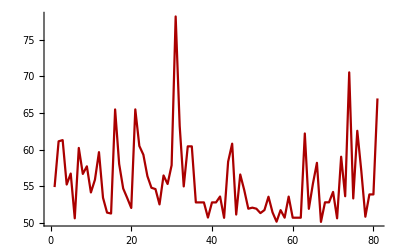

```mathematica
ListPlot[Select[primers,#[[10]]>50&][[All,10]],Joined->True,PlotStyle->Darker[Red]]
```

```mathematica
highhairpinTm=Select[primers,#[[10]]>50&];
```

```mathematica
highhairpinTm[[All,2]]
```

```mathematica
lowhairpinTm=Select[primers,#[[10]]<=50&]
```

{{21,Q21G,TTTAAGAAGGAGATATACATATGGGAAAAACGAATGCTGTACCAAGACC,,,,,,GGTCTTGGTACAGCATTCGTTTTTCCCATATGTATATCTCCTTCTTAAA,0.},{22,K22G,GGAGATATACATATGCAAGGAACGAATGCTGTACCAAGAC,,,,,,GTCTTGGTACAGCATTCGTTCCTTGCATATGTATATCTCC,37.5674},{23,T23G,GGAGATATACATATGCAAAAAGGGAATGCTGTACCAAGACCTAAAC,,,,,,GTTTAGGTCTTGGTACAGCATTCCCTTTTTGCATATGTATATCTCC,37.5674},{24,N24G,GAGATATACATATGCAAAAAACGGGTGCTGTACCAAGACCTAAACTTG,,,,,,CAAGTTTAGGTCTTGGTACAGCACCCGTTTTTTGCATATGTATATCTC,48.4667},{25,A25G,CATATGCAAAAAACGAATGGTGTACCAAGACCTAAACTTG,,,,,,CAAGTTTAGGTCTTGGTACACCATTCGTTTTTTGCATATG,47.0258},{26,V26G,GCAAAAAACGAATGCTGGACCAAGACCTAAACTTG,,,,,,CAAGTTTAGGTCTTGGTCCAGCATTCGTTTTTTGC,35.9688},{27,P27G,GCAAAAAACGAATGCTGTAGGAAGACCTAAACTTGTGGTAGG,,,,,,CCTACCACAAGTTTAGGTCTTCCTACAGCATTCGTTTTTTGC,37.4282},{28,R28G,ACGAATGCTGTACCAGGACCTAAACTTGTGGTAG,,,,,,CTACCACAAGTTTAGGTCCTGGTACAGCATTCGT,33.9985},{29,P29G,CGAATGCTGTACCAAGAGGTAAACTTGTGGTAGGACTG,,,,,,CAGTCCTACCACAAGTTTACCTCTTGGTACAGCATTCG,46.3414},{30,K30G,GCTGTACCAAGACCTGGACTTGTGGTAGGACTG,,,,,,CAGTCCTACCACAAGTCCAGGTCTTGGTACAGC,45.7393},{31,L31G,CTGTACCAAGACCTAAAGGTGTGGTAGGACTGGTAG,,,,,,CTACCAGTCCTACCACACCTTTAGGTCTTGGTACAG,45.0011},{32,V32G,CCAAGACCTAAACTTGGGGTAGGACTGGTAGTTG,,,,,,CAACTACCAGTCCTACCCCAAGTTTAGGTCTTGG,47.6946},{33,V33G,CAAGACCTAAACTTGTGGGAGGACTGGTAGTTGATCAG,,,,,,CTGATCAACTACCAGTCCTCCCACAAGTTTAGGTCTTG,35.4942},{34,G34A,GACCTAAACTTGTGGTAGCACTGGTAGTTGATCAGATG,,,,,,CATCTGATCAACTACCAGTGCTACCACAAGTTTAGGTC,30.0946},{35,L35G,CCTAAACTTGTGGTAGGAGGGGTAGTTGATCAGATGAG,,,,,,CTCATCTGATCAACTACCCCTCCTACCACAAGTTTAGG,32.6005},{36,V36G,CTTGTGGTAGGACTGGGAGTTGATCAGATGAG,,,,,,CTCATCTGATCAACTCCCAGTCCTACCACAAG,30.4788},{37,V37G,GTGGTAGGACTGGTAGGTGATCAGATGAGATG,,,,,,CATCTCATCTGATCACCTACCAGTCCTACCAC,32.3968},{38,D38G,GTAGGACTGGTAGTTGGTCAGATGAGATGGGA,,,,,,TCCCATCTCATCTGACCAACTACCAGTCCTAC,30.4788},{39,Q39G,GGTAGGACTGGTAGTTGATGGGATGAGATGGGATTATCTTTA,,,,,,TAAAGATAATCCCATCTCATCCCATCAACTACCAGTCCTACC,32.7421},{40,M40G,GGACTGGTAGTTGATCAGGGGAGATGGGATTATCTTTAC,,,,,,GTAAAGATAATCCCATCTCCCCTGATCAACTACCAGTCC,35.3055},{41,R41G,CTGGTAGTTGATCAGATGGGATGGGATTATCTTTACCG,,,,,,CGGTAAAGATAATCCCATCCCATCTGATCAACTACCAG,32.3968},{42,W42G,GGTAGTTGATCAGATGAGAGGGGATTATCTTTACCGTTATTA,,,,,,TAATAACGGTAAAGATAATCCCCTCTCATCTGATCAACTACC,0.},{43,D43G,GTAGTTGATCAGATGAGATGGGGTTATCTTTACCGTTATTATAG,,,,,,CTATAATAACGGTAAAGATAACCCCATCTCATCTGATCAACTAC,32.7421},{44,Y44G,GTTGATCAGATGAGATGGGATGGTCTTTACCGTTATTATAGCAAG,,,,,,CTTGCTATAATAACGGTAAAGACCATCCCATCTCATCTGATCAAC,46.1866},{45,L45G,GATCAGATGAGATGGGATTATGGTTACCGTTATTATAGCAAGTATG,,,,,,CATACTTGCTATAATAACGGTAACCATAATCCCATCTCATCTGATC,0.},{46,Y46G,CAGATGAGATGGGATTATCTTGGCCGTTATTATAGCAAGTATGGTG,,,,,,CACCATACTTGCTATAATAACGGCCAAGATAATCCCATCTCATCTG,32.7421},{47,R47G,GAGATGGGATTATCTTTACGGTTATTATAGCAAGTATGGTG,,,,,,CACCATACTTGCTATAATAACCGTAAAGATAATCCCATCTC,32.7421},{48,Y48G,GATGGGATTATCTTTACCGTGGTTATAGCAAGTATGGTGAAGG,,,,,,CCTTCACCATACTTGCTATAACCACGGTAAAGATAATCCCATC,34.1841},{49,Y49G,GGGATTATCTTTACCGTTATGGTAGCAAGTATGGTGAAGGAG,,,,,,CTCCTTCACCATACTTGCTACCATAACGGTAAAGATAATCCC,49.0146},{50,S50G,GATTATCTTTACCGTTATTATGGCAAGTATGGTGAAGGAGGTTTT,,,,,,AAAACCTCCTTCACCATACTTGCCATAATAACGGTAAAGATAATC,33.3533},{51,K51G,ATTATCTTTACCGTTATTATAGCGGGTATGGTGAAGGAGGTTTTAAGAG,,,,,,CTCTTAAAACCTCCTTCACCATACCCGCTATAATAACGGTAAAGATAAT,49.1435},{52,Y52G,CTTTACCGTTATTATAGCAAGGGTGGTGAAGGAGGTTTTAAGAG,,,,,,CTCTTAAAACCTCCTTCACCACCCTTGCTATAATAACGGTAAAG,36.9216},{54,E54G,GTTATTATAGCAAGTATGGTGGAGGAGGTTTTAAGAGAATGC,,,,,,GCATTCTCTTAAAACCTCCTCCACCATACTTGCTATAATAAC,34.1841},{55,G55A,GTTATTATAGCAAGTATGGTGAAGCAGGTTTTAAGAGAATGCTGAATA,,,,,,TATTCAGCATTCTCTTAAAACCTGCTTCACCATACTTGCTATAATAAC,33.9986},{56,G56A,TATAGCAAGTATGGTGAAGGAGCTTTTAAGAGAATGCTGAATAC,,,,,,GTATTCAGCATTCTCTTAAAAGCTCCTTCACCATACTTGCTATA,32.6604},{57,F57G,CAAGTATGGTGAAGGAGGTGGTAAGAGAATGCTGAATACC,,,,,,GGTATTCAGCATTCTCTTACCACCTCCTTCACCATACTTG,30.9744},{58,K58G,TATGGTGAAGGAGGTTTTGGGAGAATGCTGAATACCGG,,,,,,CCGGTATTCAGCATTCTCCCAAAACCTCCTTCACCATA,0.},{59,R59G,GAAGGAGGTTTTAAGGGAATGCTGAATACCGGG,,,,,,CCCGGTATTCAGCATTCCCTTAAAACCTCCTTC,0.},{60,M60G,GAAGGAGGTTTTAAGAGAGGGCTGAATACCGGGTATTC,,,,,,GAATACCCGGTATTCAGCCCTCTCTTAAAACCTCCTTC,44.265},{61,L61G,GTGAAGGAGGTTTTAAGAGAATGGGGAATACCGGGTATTCGTTAAATAA,,,,,,TTATTTAACGAATACCCGGTATTCCCCATTCTCTTAAAACCTCCTTCAC,43.634},{63,T63G,GAGGTTTTAAGAGAATGCTGAATGGCGGGTATTCGTTAAATAATGTTC,,,,,,GAACATTATTTAACGAATACCCGCCATTCAGCATTCTCTTAAAACCTC,33.3337},{64,G64A,GTTTTAAGAGAATGCTGAATACCGCGTATTCGTTAAATAATGTTCATA,,,,,,TATGAACATTATTTAACGAATACGCGGTATTCAGCATTCTCTTAAAAC,44.8135},{65,Y65G,TAAGAGAATGCTGAATACCGGGGGTTCGTTAAATAATGTTCATATAG,,,,,,CTATATGAACATTATTTAACGAACCCCCGGTATTCAGCATTCTCTTA,33.1582},{66,S66G,GAGAATGCTGAATACCGGGTATGGGTTAAATAATGTTCATATAGAC,,,,,,GTCTATATGAACATTATTTAACCCATACCCGGTATTCAGCATTCTC,35.6112},{67,L67G,GAATGCTGAATACCGGGTATTCGGGAAATAATGTTCATATAGACTATG,,,,,,CATAGTCTATATGAACATTATTTCCCGAATACCCGGTATTCAGCATTC,45.6332},{68,N68G,GCTGAATACCGGGTATTCGTTAGGTAATGTTCATATAGACTATGTAC,,,,,,GTACATAGTCTATATGAACATTACCTAACGAATACCCGGTATTCAGC,44.8135},{69,N69G,GAATACCGGGTATTCGTTAAATGGTGTTCATATAGACTATGTACCTAC,,,,,,GTAGGTACATAGTCTATATGAACACCATTTAACGAATACCCGGTATTC,37.3244},{70,V70G,CCGGGTATTCGTTAAATAATGGTCATATAGACTATGTACCTAC,,,,,,GTAGGTACATAGTCTATATGACCATTATTTAACGAATACCCGG,40.2756},{71,H71G,CCGGGTATTCGTTAAATAATGTTGGTATAGACTATGTACCTACAGTAAC,,,,,,GTTACTGTAGGTACATAGTCTATACCAACATTATTTAACGAATACCCGG,45.2033},{72,I72G,GGTATTCGTTAAATAATGTTCATGGAGACTATGTACCTACAGTAACTGC,,,,,,GCAGTTACTGTAGGTACATAGTCTCCATGAACATTATTTAACGAATACC,28.9734},{73,D73G,CGTTAAATAATGTTCATATAGGCTATGTACCTACAGTAACTGC,,,,,,GCAGTTACTGTAGGTACATAGCCTATATGAACATTATTTAACG,37.5164},{74,Y74G,CGTTAAATAATGTTCATATAGACGGTGTACCTACAGTAACTGCAATCGG,,,,,,CCGATTGCAGTTACTGTAGGTACACCGTCTATATGAACATTATTTAACG,32.8005},{75,V75G,ATAATGTTCATATAGACTATGGACCTACAGTAACTGCAATCGG,,,,,,CCGATTGCAGTTACTGTAGGTCCATAGTCTATATGAACATTAT,28.1935},{76,P76G,GTTCATATAGACTATGTAGGTACAGTAACTGCAATCGGAC,,,,,,GTCCGATTGCAGTTACTGTACCTACATAGTCTATATGAAC,35.0741},{77,T77G,GTTCATATAGACTATGTACCTGGAGTAACTGCAATCGGACATAC,,,,,,GTATGTCCGATTGCAGTTACTCCAGGTACATAGTCTATATGAAC,24.2432},{80,A80G,GACTATGTACCTACAGTAACTGGAATCGGACATACTTCAATTTTT,,,,,,AAAAATTGAAGTATGTCCGATTCCAGTTACTGTAGGTACATAGTC,36.1074},{81,I81G,CTATGTACCTACAGTAACTGCAGGCGGACATACTTCAATTTTTACAG,,,,,,CTGTAAAAATTGAAGTATGTCCGCCTGCAGTTACTGTAGGTACATAG,39.4335},{82,G82A,CCTACAGTAACTGCAATCGCACATACTTCAATTTTTACAG,,,,,,CTGTAAAAATTGAAGTATGTGCGATTGCAGTTACTGTAGG,40.6881},{83,H83G,CCTACAGTAACTGCAATCGGAGGTACTTCAATTTTTACAGGTTCTG,,,,,,CAGAACCTGTAAAAATTGAAGTACCTCCGATTGCAGTTACTGTAGG,47.6398},{84,T84G,CTACAGTAACTGCAATCGGACATGGTTCAATTTTTACAGGTTCTGTTC,,,,,,GAACAGAACCTGTAAAAATTGAACCATGTCCGATTGCAGTTACTGTAG,34.1215},{85,S85G,GTAACTGCAATCGGACATACTGGAATTTTTACAGGTTCTGTTCC,,,,,,GGAACAGAACCTGTAAAAATTCCAGTATGTCCGATTGCAGTTAC,36.0603},{86,I86G,GCAATCGGACATACTTCAGGTTTTACAGGTTCTGTTCCC,,,,,,GGGAACAGAACCTGTAAAACCTGAAGTATGTCCGATTGC,36.0603},{87,F87G,CGGACATACTTCAATTGGTACAGGTTCTGTTCCCTC,,,,,,GAGGGAACAGAACCTGTACCAATTGAAGTATGTCCG,40.8721},{89,G89A,CATACTTCAATTTTTACAGCTTCTGTTCCCTCCATCCAC,,,,,,GTGGATGGAGGGAACAGAAGCTGTAAAAATTGAAGTATG,36.0603},{90,S90G,CTTCAATTTTTACAGGTGGTGTTCCCTCCATCCACGG,,,,,,CCGTGGATGGAGGGAACACCACCTGTAAAAATTGAAG,43.0849},{91,V91G,CAATTTTTACAGGTTCTGGTCCCTCCATCCACGGAATT,,,,,,AATTCCGTGGATGGAGGGACCAGAACCTGTAAAAATTG,42.4532},{92,P92G,ATTTTTACAGGTTCTGTTGGCTCCATCCACGGAATTGCAG,,,,,,CTGCAATTCCGTGGATGGAGCCAACAGAACCTGTAAAAAT,36.0603},{95,H95G,CTGTTCCCTCCATCGGCGGAATTGCAGGAAAC,,,,,,GTTTCCTGCAATTCCGCCGATGGAGGGAACAG,29.768},{96,G96A,CTGTTCCCTCCATCCACGCAATTGCAGGAAACGATTG,,,,,,CAATCGTTTCCTGCAATTGCGTGGATGGAGGGAACAG,40.0706},{98,A98G,CTCCATCCACGGAATTGGAGGAAACGATTGGTATG,,,,,,CATACCAATCGTTTCCTCCAATTCCGTGGATGGAG,42.1272},{99,G99A,CCATCCACGGAATTGCAGCAAACGATTGGTATGATAAA,,,,,,TTTATCATACCAATCGTTTGCTGCAATTCCGTGGATGG,40.0051},{100,N100G,CCACGGAATTGCAGGAGGCGATTGGTATGATAAAG,,,,,,CTTTATCATACCAATCGCCTCCTGCAATTCCGTGG,47.1218},{101,D101G,CACGGAATTGCAGGAAACGGTTGGTATGATAAAGAATTAG,,,,,,CTAATTCTTTATCATACCAACCGTTTCCTGCAATTCCGTG,0.},{102,W102G,GGAATTGCAGGAAACGATGGGTATGATAAAGAATTAGGG,,,,,,CCCTAATTCTTTATCATACCCATCGTTTCCTGCAATTCC,0.},{103,Y103G,GGAATTGCAGGAAACGATTGGGGTGATAAAGAATTAGGGAAAAGTG,,,,,,CACTTTTCCCTAATTCTTTATCACCCCAATCGTTTCCTGCAATTCC,0.},{104,D104G,GCAGGAAACGATTGGTATGGTAAAGAATTAGGGAAAAGTG,,,,,,CACTTTTCCCTAATTCTTTACCATACCAATCGTTTCCTGC,0.},{105,K105G,GCAGGAAACGATTGGTATGATGGAGAATTAGGGAAAAGTGTTTAC,,,,,,GTAAACACTTTTCCCTAATTCTCCATCATACCAATCGTTTCCTGC,0.},{106,E106G,GGAAACGATTGGTATGATAAAGGATTAGGGAAAAGTGTTTACTG,,,,,,CAGTAAACACTTTTCCCTAATCCTTTATCATACCAATCGTTTCC,33.104},{107,L107G,GAAACGATTGGTATGATAAAGAAGGAGGGAAAAGTGTTTACTGTACATC,,,,,,GATGTACAGTAAACACTTTTCCCTCCTTCTTTATCATACCAATCGTTTC,33.104},{108,G108A,CGATTGGTATGATAAAGAATTAGCGAAAAGTGTTTACTGTACATCTG,,,,,,CAGATGTACAGTAAACACTTTTCGCTAATTCTTTATCATACCAATCG,26.3528},{109,K109G,TGGTATGATAAAGAATTAGGGGGAAGTGTTTACTGTACATCTGATG,,,,,,CATCAGATGTACAGTAAACACTTCCCCCTAATTCTTTATCATACCA,33.104},{110,S110G,GTATGATAAAGAATTAGGGAAAGGTGTTTACTGTACATCTGATGAAAC,,,,,,GTTTCATCAGATGTACAGTAAACACCTTTCCCTAATTCTTTATCATAC,31.0292},{111,V111G,GATAAAGAATTAGGGAAAAGTGGTTACTGTACATCTGATGAAACAG,,,,,,CTGTTTCATCAGATGTACAGTAACCACTTTTCCCTAATTCTTTATC,41.807},{112,Y112G,GAATTAGGGAAAAGTGTTGGCTGTACATCTGATGAAACAG,,,,,,CTGTTTCATCAGATGTACAGCCAACACTTTTCCCTAATTC,40.5033},{113,C113G,GAATTAGGGAAAAGTGTTTACGGTACATCTGATGAAACAGTACA,,,,,,TGTACTGTTTCATCAGATGTACCGTAAACACTTTTCCCTAATTC,31.7229},{114,T114G,ATTAGGGAAAAGTGTTTACTGTGGATCTGATGAAACAGTACAACCGG,,,,,,CCGGTTGTACTGTTTCATCAGATCCACAGTAAACACTTTTCCCTAAT,36.5983},{115,S115G,GGAAAAGTGTTTACTGTACAGGTGATGAAACAGTACAACCGG,,,,,,CCGGTTGTACTGTTTCATCACCTGTACAGTAAACACTTTTCC,42.5555},{116,D116G,GTGTTTACTGTACATCTGGTGAAACAGTACAACCGG,,,,,,CCGGTTGTACTGTTTCACCAGATGTACAGTAAACAC,42.0176},{117,E117G,GTTTACTGTACATCTGATGGAACAGTACAACCGGTAGG,,,,,,CCTACCGGTTGTACTGTTCCATCAGATGTACAGTAAAC,43.4767},{118,T118G,CTGTACATCTGATGAAGGAGTACAACCGGTAGGAAC,,,,,,GTTCCTACCGGTTGTACTCCTTCATCAGATGTACAG,36.684},{119,V119G,GTACATCTGATGAAACAGGACAACCGGTAGGAACTAC,,,,,,GTAGTTCCTACCGGTTGTCCTGTTTCATCAGATGTAC,43.7591},{120,Q120G,CATCTGATGAAACAGTAGGACCGGTAGGAACTACTTC,,,,,,GAAGTAGTTCCTACCGGTCCTACTGTTTCATCAGATG,42.0516},{121,P121G,CATCTGATGAAACAGTACAAGGGGTAGGAACTACTTCTAACTC,,,,,,GAGTTAGAAGTAGTTCCTACCCCTTGTACTGTTTCATCAGATG,42.8464},{123,G123A,GAAACAGTACAACCGGTAGCAACTACTTCTAACTCGGT,,,,,,ACCGAGTTAGAAGTAGTTGCTACCGGTTGTACTGTTTC,35.602},{129,V129G,GAACTACTTCTAACTCGGGTGGACAACATTCACCAAG,,,,,,CTTGGTGAATGTTGTCCACCCGAGTTAGAAGTAGTTC,45.3881},{130,G130A,CTACTTCTAACTCGGTTGCACAACATTCACCAAGAAAC,,,,,,GTTTCTTGGTGAATGTTGTGCAACCGAGTTAGAAGTAG,39.5557},{131,Q131G,CTTCTAACTCGGTTGGAGGACATTCACCAAGAAACC,,,,,,GGTTTCTTGGTGAATGTCCTCCAACCGAGTTAGAAG,43.9602},{132,H132G,CTAACTCGGTTGGACAAGGTTCACCAAGAAACCTTTGG,,,,,,CCAAAGGTTTCTTGGTGAACCTTGTCCAACCGAGTTAG,39.7407},{133,S133G,CTCGGTTGGACAACATGGACCAAGAAACCTTTGGTC,,,,,,GACCAAAGGTTTCTTGGTCCATGTTGTCCAACCGAG,47.3338},{134,P134G,CGGTTGGACAACATTCAGGAAGAAACCTTTGGTCTAC,,,,,,GTAGACCAAAGGTTTCTTCCTGAATGTTGTCCAACCG,39.5557},{135,R135G,GTTGGACAACATTCACCAGGAAACCTTTGGTCTACTAC,,,,,,GTAGTAGACCAAAGGTTTCCTGGTGAATGTTGTCCAAC,35.9296},{136,N136G,GACAACATTCACCAAGAGGCCTTTGGTCTACTACGG,,,,,,CCGTAGTAGACCAAAGGCCTCTTGGTGAATGTTGTC,30.187},{137,L137G,CAACATTCACCAAGAAACGGTTGGTCTACTACGGTAACAG,,,,,,CTGTTACCGTAGTAGACCAACCGTTTCTTGGTGAATGTTG,46.3361},{139,S139G,CACCAAGAAACCTTTGGGGTACTACGGTAACAGATCAG,,,,,,CTGATCTGTTACCGTAGTACCCCAAAGGTTTCTTGGTG,45.5142},{140,T140G,CAAGAAACCTTTGGTCTGGTACGGTAACAGATCAGC,,,,,,GCTGATCTGTTACCGTACCAGACCAAAGGTTTCTTG,49.0925},{141,T141G,GAAACCTTTGGTCTACTGGGGTAACAGATCAGCTAGG,,,,,,CCTAGCTGATCTGTTACCCCAGTAGACCAAAGGTTTC,30.6712},{142,V142G,CTTTGGTCTACTACGGGAACAGATCAGCTAGG,,,,,,CCTAGCTGATCTGTTCCCGTAGTAGACCAAAG,25.6232},{143,T143G,CTTTGGTCTACTACGGTAGGAGATCAGCTAGGTTTGGC,,,,,,GCCAAACCTAGCTGATCTCCTACCGTAGTAGACCAAAG,44.8399},{144,D144G,GTCTACTACGGTAACAGGTCAGCTAGGTTTGGCAAC,,,,,,GTTGCCAAACCTAGCTGACCTGTTACCGTAGTAGAC,28.4107},{148,L148G,GTAACAGATCAGCTAGGTGGGGCAACAAACTTTACTTC,,,,,,GAAGTAAAGTTTGTTGCCCCACCTAGCTGATCTGTTAC,39.7372},{150,T150G,CAGATCAGCTAGGTTTGGCAGGAAACTTTACTTCTAAGGTTG,,,,,,CAACCTTAGAAGTAAAGTTTCCTGCCAAACCTAGCTGATCTG,36.2557},{154,S154G,GGCAACAAACTTTACTGGTAAGGTTGTGGGGGTCTC,,,,,,GAGACCCCCACAACCTTACCAGTAAAGTTTGTTGCC,36.3742},{155,K155G,CAACAAACTTTACTTCTGGGGTTGTGGGGGTCTCTCTG,,,,,,CAGAGAGACCCCCACAACCCCAGAAGTAAAGTTTGTTG,0.},{156,V156G,CTTTACTTCTAAGGGTGTGGGGGTCTCTC,,,,,,GAGAGACCCCCACACCCTTAGAAGTAAAG,0.},{157,V157G,CTTTACTTCTAAGGTTGGGGGGGTCTCTCTGAAAG,,,,,,CTTTCAGAGAGACCCCCCCAACCTTAGAAGTAAAG,0.},{158,G158A,CTTCTAAGGTTGTGGCGGTCTCTCTGAAAGAC,,,,,,GTCTTTCAGAGAGACCGCCACAACCTTAGAAG,32.3191},{159,V159G,CTAAGGTTGTGGGGGGCTCTCTGAAAGACAG,,,,,,CTGTCTTTCAGAGAGCCCCCCACAACCTTAG,45.3915},{161,L161G,GTTGTGGGGGTCTCTGGGAAAGACAGAGCATC,,,,,,GATGCTCTGTCTTTCCCAGAGACCCCCACAAC,49.0087},{164,R164G,GTCTCTCTGAAAGACGGAGCATCAATTCTGCCTG,,,,,,CAGGCAGAATTGATGCTCCGTCTTTCAGAGAGAC,44.0929},{169,P169G,GACAGAGCATCAATTCTGGGTGCAGGGCACAACCCAAC,,,,,,GTTGGGTTGTGCCCTGCACCCAGAATTGATGCTCTGTC,46.228},{171,G171A,CAATTCTGCCTGCAGCGCACAACCCAACAG,,,,,,CTGTTGGGTTGTGCGCTGCAGGCAGAATTG,45.5677},{177,A177G,GCACAACCCAACAGGAGGATTTTGGTTCGATGATAC,,,,,,GTATCATCGAACCAAAATCCTCCTGTTGGGTTGTGC,33.0035},{178,F178G,CACAACCCAACAGGAGCAGGTTGGTTCGATGATACTAC,,,,,,GTAGTATCATCGAACCAACCTGCTCCTGTTGGGTTGTG,49.9565},{179,W179G,CCCAACAGGAGCATTTGGGTTCGATGATACTACAG,,,,,,CTGTAGTATCATCGAACCCAAATGCTCCTGTTGGG,45.236},{180,F180G,CCAACAGGAGCATTTTGGGGCGATGATACTACAGGTAAAT,,,,,,ATTTACCTGTAGTATCATCGCCCCAAAATGCTCCTGTTGG,31.5331},{181,D181G,CAGGAGCATTTTGGTTCGGTGATACTACAGGTAAATTC,,,,,,GAATTTACCTGTAGTATCACCGAACCAAAATGCTCCTG,30.2191},{182,D182G,AGGAGCATTTTGGTTCGATGGTACTACAGGTAAATTCATTAC,,,,,,GTAATGAATTTACCTGTAGTACCATCGAACCAAAATGCTCCT,33.5924},{185,G185A,CATTTTGGTTCGATGATACTACAGCTAAATTCATTACCAGTACATATT,,,,,,AATATGTACTGGTAATGAATTTAGCTGTAGTATCATCGAACCAAAATG,29.4272},{186,K186G,TTGGTTCGATGATACTACAGGTGGATTCATTACCAGTACATATTATAC,,,,,,GTATAATATGTACTGGTAATGAATCCACCTGTAGTATCATCGAACCAA,31.3227},{188,I188G,CGATGATACTACAGGTAAATTCGGTACCAGTACATATTATACTAAAG,,,,,,CTTTAGTATAATATGTACTGGTACCGAATTTACCTGTAGTATCATCG,38.7374},{189,T189G,GATACTACAGGTAAATTCATTGGCAGTACATATTATACTAAAGA,,,,,,TCTTTAGTATAATATGTACTGCCAATGAATTTACCTGTAGTATC,30.2191},{193,Y193G,GTAAATTCATTACCAGTACATATGGTACTAAAGAATTACCTAAATGGG,,,,,,CCCATTTAGGTAATTCTTTAGTACCATATGTACTGGTAATGAATTTAC,44.1448},{194,T194G,CATTACCAGTACATATTATGGTAAAGAATTACCTAAATGGG,,,,,,CCCATTTAGGTAATTCTTTACCATAATATGTACTGGTAATG,49.3802},{196,E196G,CCAGTACATATTATACTAAAGGATTACCTAAATGGGTAAACGAC,,,,,,GTCGTTTACCCATTTAGGTAATCCTTTAGTATAATATGTACTGG,35.7627},{197,L197G,CCAGTACATATTATACTAAAGAAGGACCTAAATGGGTAAACGACTTTAA,,,,,,TTAAAGTCGTTTACCCATTTAGGTCCTTCTTTAGTATAATATGTACTGG,28.9405},{198,P198G,GTACATATTATACTAAAGAATTAGGTAAATGGGTAAACGACTTTAATAA,,,,,,TTATTAAAGTCGTTTACCCATTTACCTAATTCTTTAGTATAATATGTAC,38.1822},{199,K199G,CATATTATACTAAAGAATTACCTGGATGGGTAAACGACTTTAATAATAA,,,,,,TTATTATTAAAGTCGTTTACCCATCCAGGTAATTCTTTAGTATAATATG,44.6991},{200,W200G,ATTATACTAAAGAATTACCTAAAGGGGTAAACGACTTTAATAATAAAAA,,,,,,TTTTTATTATTAAAGTCGTTTACCCCTTTAGGTAATTCTTTAGTATAAT,44.6991},{201,V201G,ATACTAAAGAATTACCTAAATGGGGAAACGACTTTAATAATAAAAATG,,,,,,CATTTTTATTATTAAAGTCGTTTCCCCATTTAGGTAATTCTTTAGTAT,38.816},{202,N202G,CTAAAGAATTACCTAAATGGGTAGGCGACTTTAATAATAAAAATGTTCC,,,,,,GGAACATTTTTATTATTAAAGTCGCCTACCCATTTAGGTAATTCTTTAG,39.4289},{203,D203G,GAATTACCTAAATGGGTAAACGGCTTTAATAATAAAAATGTTCCGG,,,,,,CCGGAACATTTTTATTATTAAAGCCGTTTACCCATTTAGGTAATTC,44.6991},{204,F204G,ATTACCTAAATGGGTAAACGACGGTAATAATAAAAATGTTCCGGCTC,,,,,,GAGCCGGAACATTTTTATTATTACCGTCGTTTACCCATTTAGGTAAT,44.6991},{205,N205G,CCTAAATGGGTAAACGACTTTGGTAATAAAAATGTTCCGGCTCAG,,,,,,CTGAGCCGGAACATTTTTATTACCAAAGTCGTTTACCCATTTAGG,0.},{206,N206G,CTAAATGGGTAAACGACTTTAATGGTAAAAATGTTCCGGCTCAGTTGG,,,,,,CCAACTGAGCCGGAACATTTTTACCATTAAAGTCGTTTACCCATTTAG,0.},{207,K207G,GGGTAAACGACTTTAATAATGGAAATGTTCCGGCTCAGTTGG,,,,,,CCAACTGAGCCGGAACATTTCCATTATTAAAGTCGTTTACCC,49.6603},{208,N208G,GTAAACGACTTTAATAATAAAGGTGTTCCGGCTCAGTTGGTAGC,,,,,,GCTACCAACTGAGCCGGAACACCTTTATTATTAAAGTCGTTTAC,43.4886},{209,V209G,GACTTTAATAATAAAAATGGTCCGGCTCAGTTGGTAGC,,,,,,GCTACCAACTGAGCCGGACCATTTTTATTATTAAAGTC,28.9516},{210,P210G,CGACTTTAATAATAAAAATGTTGGGGCTCAGTTGGTAGCTAATGGCTG,,,,,,CAGCCATTAGCTACCAACTGAGCCCCAACATTTTTATTATTAAAGTCG,34.9396},{211,A211G,TAATAATAAAAATGTTCCGGGTCAGTTGGTAGCTAATGGCTG,,,,,,CAGCCATTAGCTACCAACTGACCCGGAACATTTTTATTATTA,48.4099},{212,Q212G,TAATAATAAAAATGTTCCGGCTGGGTTGGTAGCTAATGGCTGGAATAC,,,,,,GTATTCCAGCCATTAGCTACCAACCCAGCCGGAACATTTTTATTATTA,46.2107},{213,L213G,GTTCCGGCTCAGGGGGTAGCTAATGGC,,,,,,GCCATTAGCTACCCCCTGAGCCGGAAC,35.646},{215,A215G,CGGCTCAGTTGGTAGGTAATGGCTGGAATAC,,,,,,GTATTCCAGCCATTACCTACCAACTGAGCCG,0.},{216,N216G,CGGCTCAGTTGGTAGCTGGTGGCTGGAATACACTATTG,,,,,,CAATAGTGTATTCCAGCCACCAGCTACCAACTGAGCCG,48.4099},{217,G217A,GCTCAGTTGGTAGCTAATGCCTGGAATACACTATTGCC,,,,,,GGCAATAGTGTATTCCAGGCATTAGCTACCAACTGAGC,38.4995},{218,W218G,GTTGGTAGCTAATGGCGGGAATACACTATTGCCC,,,,,,GGGCAATAGTGTATTCCCGCCATTAGCTACCAAC,44.1365},{219,N219G,TTGGTAGCTAATGGCTGGGGTACACTATTGCCCATTAATC,,,,,,GATTAATGGGCAATAGTGTACCCCAGCCATTAGCTACCAA,48.4099},{220,T220G,GGTAGCTAATGGCTGGAATGGACTATTGCCCATTAATCAG,,,,,,CTGATTAATGGGCAATAGTCCATTCCAGCCATTAGCTACC,48.4099},{221,L221G,GTAGCTAATGGCTGGAATACAGGATTGCCCATTAATCAGTATACAG,,,,,,CTGTATACTGATTAATGGGCAATCCTGTATTCCAGCCATTAGCTAC,48.4099},{222,L222G,CTAATGGCTGGAATACACTAGGGCCCATTAATCAGTATACAG,,,,,,CTGTATACTGATTAATGGGCCCTAGTGTATTCCAGCCATTAG,34.7316},{223,P223G,CTAATGGCTGGAATACACTATTGGGCATTAATCAGTATACAGAAAGCTC,,,,,,GAGCTTTCTGTATACTGATTAATGCCCAATAGTGTATTCCAGCCATTAG,35.909},{224,I224G,CTGGAATACACTATTGCCCGGTAATCAGTATACAGAAAGCTC,,,,,,GAGCTTTCTGTATACTGATTACCGGGCAATAGTGTATTCCAG,31.422},{225,N225G,GGAATACACTATTGCCCATTGGTCAGTATACAGAAAGCTCAG,,,,,,CTGAGCTTTCTGTATACTGACCAATGGGCAATAGTGTATTCC,26.8037},{227,Y227G,ATACACTATTGCCCATTAATCAGGGTACAGAAAGCTCAGAAGATAATG,,,,,,CATTATCTTCTGAGCTTTCTGTACCCTGATTAATGGGCAATAGTGTAT,43.7924},{228,T228G,CACTATTGCCCATTAATCAGTATGGAGAAAGCTCAGAAGATAATGTGG,,,,,,CCACATTATCTTCTGAGCTTTCTCCATACTGATTAATGGGCAATAGTG,38.7877},{229,E229G,GCCCATTAATCAGTATACAGGAAGCTCAGAAGATAATGTG,,,,,,CACATTATCTTCTGAGCTTCCTGTATACTGATTAATGGGC,0.},{230,S230G,CCATTAATCAGTATACAGAAGGCTCAGAAGATAATGTGGAATG,,,,,,CATTCCACATTATCTTCTGAGCCTTCTGTATACTGATTAATGG,0.},{231,S231G,CATTAATCAGTATACAGAAAGCGGAGAAGATAATGTGGAATGGGAAG,,,,,,CTTCCCATTCCACATTATCTTCTCCGCTTTCTGTATACTGATTAATG,0.},{232,E232G,GTATACAGAAAGCTCAGGAGATAATGTGGAATGGG,,,,,,CCCATTCCACATTATCTCCTGAGCTTTCTGTATAC,0.},{233,D233G,TATACAGAAAGCTCAGAAGGTAATGTGGAATGGGAAGG,,,,,,CCTTCCCATTCCACATTACCTTCTGAGCTTTCTGTATA,27.523},{234,N234G,GTATACAGAAAGCTCAGAAGATGGTGTGGAATGGGAAGGTTTATTAG,,,,,,CTAATAAACCTTCCCATTCCACACCATCTTCTGAGCTTTCTGTATAC,0.},{235,V235G,GAAAGCTCAGAAGATAATGGGGAATGGGAAGGTTTATTAG,,,,,,CTAATAAACCTTCCCATTCCCCATTATCTTCTGAGCTTTC,0.},{236,E236G,GCTCAGAAGATAATGTGGGATGGGAAGGTTTATTAGGG,,,,,,CCCTAATAAACCTTCCCATCCCACATTATCTTCTGAGC,0.},{237,W237G,CAGAAGATAATGTGGAAGGGGAAGGTTTATTAGGGAG,,,,,,CTCCCTAATAAACCTTCCCCTTCCACATTATCTTCTG,0.},{238,E238G,CAGAAGATAATGTGGAATGGGGAGGTTTATTAGGGAGTAAAAAA,,,,,,TTTTTTACTCCCTAATAAACCTCCCCATTCCACATTATCTTCTG,0.},{239,G239A,GAAGATAATGTGGAATGGGAAGCTTTATTAGGGAGTAAAAAAACAC,,,,,,GTGTTTTTTTACTCCCTAATAAAGCTTCCCATTCCACATTATCTTC,0.},{240,L240G,GATAATGTGGAATGGGAAGGTGGATTAGGGAGTAAAAAAACACC,,,,,,GGTGTTTTTTTACTCCCTAATCCACCTTCCCATTCCACATTATC,39.0712},{241,L241G,GTGGAATGGGAAGGTTTAGGAGGGAGTAAAAAAACACC,,,,,,GGTGTTTTTTTACTCCCTCCTAAACCTTCCCATTCCAC,0.},{242,G242A,TGGAATGGGAAGGTTTATTAGCGAGTAAAAAAACACCTACATTC,,,,,,GAATGTAGGTGTTTTTTTACTCGCTAATAAACCTTCCCATTCCA,30.1961},{243,S243G,GGGAAGGTTTATTAGGGGGTAAAAAAACACCTACATTC,,,,,,GAATGTAGGTGTTTTTTTACCCCCTAATAAACCTTCCC,37.9982},{244,K244G,ATGGGAAGGTTTATTAGGGAGTGGAAAAACACCTACATTCCCTTATAC,,,,,,GTATAAGGGAATGTAGGTGTTTTTCCACTCCCTAATAAACCTTCCCAT,40.1992},{245,K245G,GAAGGTTTATTAGGGAGTAAAGGAACACCTACATTCCCTTATACAG,,,,,,CTGTATAAGGGAATGTAGGTGTTCCTTTACTCCCTAATAAACCTTC,37.2723},{246,T246G,GGTTTATTAGGGAGTAAAAAAGGACCTACATTCCCTTATACAGATC,,,,,,GATCTGTATAAGGGAATGTAGGTCCTTTTTTACTCCCTAATAAACC,38.6388},{247,P247G,GTTTATTAGGGAGTAAAAAAACAGGTACATTCCCTTATACAGATCTGGC,,,,,,GCCAGATCTGTATAAGGGAATGTACCTGTTTTTTTACTCCCTAATAAAC,34.184},{248,T248G,GGGAGTAAAAAAACACCTGGATTCCCTTATACAGATCTGG,,,,,,CCAGATCTGTATAAGGGAATCCAGGTGTTTTTTTACTCCC,32.4988},{249,F249G,GGAGTAAAAAAACACCTACAGGCCCTTATACAGATCTGGCTAAA,,,,,,TTTAGCCAGATCTGTATAAGGGCCTGTAGGTGTTTTTTTACTCC,36.8581},{250,P250G,GGAGTAAAAAAACACCTACATTCGGTTATACAGATCTGGCTAAAGATT,,,,,,AATCTTTAGCCAGATCTGTATAACCGAATGTAGGTGTTTTTTTACTCC,27.1834},{252,T252G,AAAAAACACCTACATTCCCTTATGGAGATCTGGCTAAAGATTATGAAGC,,,,,,GCTTCATAATCTTTAGCCAGATCTCCATAAGGGAATGTAGGTGTTTTTT,41.9329},{253,D253G,CCTACATTCCCTTATACAGGTCTGGCTAAAGATTATGAAG,,,,,,CTTCATAATCTTTAGCCAGACCTGTATAAGGGAATGTAGG,37.6324},{254,L254G,CACCTACATTCCCTTATACAGATGGGGCTAAAGATTATGAAGCTAAAAA,,,,,,TTTTTAGCTTCATAATCTTTAGCCCCATCTGTATAAGGGAATGTAGGTG,36.9972},{255,A255G,CTACATTCCCTTATACAGATCTGGGTAAAGATTATGAAGCTAAAAAAG,,,,,,CTTTTTTAGCTTCATAATCTTTACCCAGATCTGTATAAGGGAATGTAG,31.9662},{256,K256G,CCCTTATACAGATCTGGCTGGAGATTATGAAGCTAAAAAAGG,,,,,,CCTTTTTTAGCTTCATAATCTCCAGCCAGATCTGTATAAGGG,36.8327},{257,D257G,CCCTTATACAGATCTGGCTAAAGGTTATGAAGCTAAAAAAGGATTAAT,,,,,,ATTAATCCTTTTTTAGCTTCATAACCTTTAGCCAGATCTGTATAAGGG,30.4769},{258,Y258G,CTTATACAGATCTGGCTAAAGATGGTGAAGCTAAAAAAGGATTAATCCG,,,,,,CGGATTAATCCTTTTTTAGCTTCACCATCTTTAGCCAGATCTGTATAAG,38.1372},{259,E259G,CAGATCTGGCTAAAGATTATGGAGCTAAAAAAGGATTAATCCG,,,,,,CGGATTAATCCTTTTTTAGCTCCATAATCTTTAGCCAGATCTG,38.1372},{260,A260G,GATCTGGCTAAAGATTATGAAGGTAAAAAAGGATTAATCCGTAC,,,,,,GTACGGATTAATCCTTTTTTACCTTCATAATCTTTAGCCAGATC,38.1372},{261,K261G,CTGGCTAAAGATTATGAAGCTGGAAAAGGATTAATCCGTACTACAC,,,,,,GTGTAGTACGGATTAATCCTTTTCCAGCTTCATAATCTTTAGCCAG,37.187},{262,K262G,GCTAAAGATTATGAAGCTAAAGGAGGATTAATCCGTACTACACC,,,,,,GGTGTAGTACGGATTAATCCTCCTTTAGCTTCATAATCTTTAGC,48.0408},{264,L264G,GATTATGAAGCTAAAAAAGGAGGAATCCGTACTACACCATTTGG,,,,,,CCAAATGGTGTAGTACGGATTCCTCCTTTTTTAGCTTCATAATC,34.5426},{265,I265G,ATTATGAAGCTAAAAAAGGATTAGGCCGTACTACACCATTTGGAAATAC,,,,,,GTATTTCCAAATGGTGTAGTACGGCCTAATCCTTTTTTAGCTTCATAAT,30.0496},{266,R266G,GAAGCTAAAAAAGGATTAATCGGTACTACACCATTTGGAAATAC,,,,,,GTATTTCCAAATGGTGTAGTACCGATTAATCCTTTTTTAGCTTC,45.0223},{268,T268G,CTAAAAAAGGATTAATCCGTACTGGACCATTTGGAAATACCTTAACTC,,,,,,GAGTTAAGGTATTTCCAAATGGTCCAGTACGGATTAATCCTTTTTTAG,48.9807},{269,P269G,AAAAAGGATTAATCCGTACTACAGGATTTGGAAATACCTTAACTCTTC,,,,,,GAAGAGTTAAGGTATTTCCAAATCCTGTAGTACGGATTAATCCTTTTT,45.1271},{270,F270G,GATTAATCCGTACTACACCAGGTGGAAATACCTTAACTCTTCAG,,,,,,CTGAAGAGTTAAGGTATTTCCACCTGGTGTAGTACGGATTAATC,43.2304},{271,G271A,ATTAATCCGTACTACACCATTTGCAAATACCTTAACTCTTCAGATG,,,,,,CATCTGAAGAGTTAAGGTATTTGCAAATGGTGTAGTACGGATTAAT,0.},{272,N272G,CCGTACTACACCATTTGGAGGTACCTTAACTCTTCAGATG,,,,,,CATCTGAAGAGTTAAGGTACCTCCAAATGGTGTAGTACGG,35.0151},{274,L274G,CACCATTTGGAAATACCGGAACTCTTCAGATGGCAG,,,,,,CTGCCATCTGAAGAGTTCCGGTATTTCCAAATGGTG,40.4268},{275,T275G,CCATTTGGAAATACCTTAGGTCTTCAGATGGCAGATGCTG,,,,,,CAGCATCTGCCATCTGAAGACCTAAGGTATTTCCAAATGG,36.4641},{276,L276G,CATTTGGAAATACCTTAACTGGTCAGATGGCAGATGCTGCAATT,,,,,,AATTGCAGCATCTGCCATCTGACCAGTTAAGGTATTTCCAAATG,43.2487},{277,Q277G,GGAAATACCTTAACTCTTGGGATGGCAGATGCTGCAATTG,,,,,,CAATTGCAGCATCTGCCATCCCAAGAGTTAAGGTATTTCC,41.8646},{278,M278G,AAATACCTTAACTCTTCAGGGGGCAGATGCTGCAATTGATG,,,,,,CATCAATTGCAGCATCTGCCCCCTGAAGAGTTAAGGTATTT,39.2075},{279,A279G,CCTTAACTCTTCAGATGGGAGATGCTGCAATTGATG,,,,,,CATCAATTGCAGCATCTCCCATCTGAAGAGTTAAGG,0.},{282,A282G,TTCAGATGGCAGATGCTGGAATTGATGGTAACCAAATG,,,,,,CATTTGGTTACCATCAATTCCAGCATCTGCCATCTGAA,39.776},{286,N286G,GCTGCAATTGATGGTGGCCAAATGGGAGTTGATG,,,,,,CATCAACTCCCATTTGGCCACCATCAATTGCAGC,36.9795},{287,Q287G,GATGCTGCAATTGATGGTAACGGAATGGGAGTTGATGATATTACTG,,,,,,CAGTAATATCATCAACTCCCATTCCGTTACCATCAATTGCAGCATC,42.5066},{288,M288G,CTGCAATTGATGGTAACCAAGGGGGAGTTGATGATATTACTG,,,,,,CAGTAATATCATCAACTCCCCCTTGGTTACCATCAATTGCAG,38.8014},{289,G289A,CAATTGATGGTAACCAAATGGCAGTTGATGATATTACTGACTTC,,,,,,GAAGTCAGTAATATCATCAACTGCCATTTGGTTACCATCAATTG,35.1834},{290,V290G,GATGGTAACCAAATGGGAGGTGATGATATTACTGACTTC,,,,,,GAAGTCAGTAATATCATCACCTCCCATTTGGTTACCATC,38.8014},{291,D291G,GTAACCAAATGGGAGTTGGTGATATTACTGACTTCC,,,,,,GGAAGTCAGTAATATCACCAACTCCCATTTGGTTAC,48.7243},{292,D292G,CCAAATGGGAGTTGATGGTATTACTGACTTCCTTAC,,,,,,GTAAGGAAGTCAGTAATACCATCAACTCCCATTTGG,36.9795},{293,I293G,TAACCAAATGGGAGTTGATGATGGTACTGACTTCCTTACAGTAAAC,,,,,,GTTTACTGTAAGGAAGTCAGTACCATCATCAACTCCCATTTGGTTA,38.0133},{294,T294G,CAAATGGGAGTTGATGATATTGGTGACTTCCTTACAGTAAACCTTG,,,,,,CAAGGTTTACTGTAAGGAAGTCACCAATATCATCAACTCCCATTTG,29.6929},{295,D295G,GGAGTTGATGATATTACTGGCTTCCTTACAGTAAACCTTG,,,,,,CAAGGTTTACTGTAAGGAAGCCAGTAATATCATCAACTCC,46.0616},{296,F296G,GAGTTGATGATATTACTGACGGCCTTACAGTAAACCTTGCTTC,,,,,,GAAGCAAGGTTTACTGTAAGGCCGTCAGTAATATCATCAACTC,45.1254},{297,L297G,GTTGATGATATTACTGACTTCGGTACAGTAAACCTTGCTTCAACGG,,,,,,CCGTTGAAGCAAGGTTTACTGTACCGAAGTCAGTAATATCATCAAC,45.1254},{298,T298G,GATATTACTGACTTCCTTGGAGTAAACCTTGCTTCAACGG,,,,,,CCGTTGAAGCAAGGTTTACTCCAAGGAAGTCAGTAATATC,29.2524},{299,V299G,CTGACTTCCTTACAGGAAACCTTGCTTCAACG,,,,,,CGTTGAAGCAAGGTTTCCTGTAAGGAAGTCAG,45.9649},{300,N300G,ATATTACTGACTTCCTTACAGTAGGCCTTGCTTCAACGGATTATGTTG,,,,,,CAACATAATCCGTTGAAGCAAGGCCTACTGTAAGGAAGTCAGTAATAT,39.9967},{301,L301G,CTGACTTCCTTACAGTAAACGGTGCTTCAACGGATTATGTTG,,,,,,CAACATAATCCGTTGAAGCACCGTTTACTGTAAGGAAGTCAG,44.2371},{302,A302G,CTTCCTTACAGTAAACCTTGGTTCAACGGATTATGTTGGA,,,,,,TCCAACATAATCCGTTGAACCAAGGTTTACTGTAAGGAAG,41.3924},{303,S303G,CCTTACAGTAAACCTTGCTGGAACGGATTATGTTGGACAC,,,,,,GTGTCCAACATAATCCGTTCCAGCAAGGTTTACTGTAAGG,41.7216},{304,T304G,CTTACAGTAAACCTTGCTTCAGGGGATTATGTTGGACACAACTTTG,,,,,,CAAAGTTGTGTCCAACATAATCCCCTGAAGCAAGGTTTACTGTAAG,41.4962},{305,D305G,GTAAACCTTGCTTCAACGGGTTATGTTGGACACAACTTT,,,,,,AAAGTTGTGTCCAACATAACCCGTTGAAGCAAGGTTTAC,40.7494},{306,Y306G,CCTTGCTTCAACGGATGGTGTTGGACACAACTTTGG,,,,,,CCAAAGTTGTGTCCAACACCATCCGTTGAAGCAAGG,49.0287},{307,V307G,GCTTCAACGGATTATGGTGGACACAACTTTGGTC,,,,,,GACCAAAGTTGTGTCCACCATAATCCGTTGAAGC,30.3814},{308,G308A,CTTCAACGGATTATGTTGCACACAACTTTGGTCCAAAC,,,,,,GTTTGGACCAAAGTTGTGTGCAACATAATCCGTTGAAG,48.8905},{309,H309G,CAACGGATTATGTTGGAGGCAACTTTGGTCCAAACTC,,,,,,GAGTTTGGACCAAAGTTGCCTCCAACATAATCCGTTG,38.395},{312,G312A,GATTATGTTGGACACAACTTTGCTCCAAACTCTATAGAAGTTGA,,,,,,TCAACTTCTATAGAGTTTGGAGCAAAGTTGTGTCCAACATAATC,49.0287},{313,P313G,GTTGGACACAACTTTGGTGGAAACTCTATAGAAGTTGAGG,,,,,,CCTCAACTTCTATAGAGTTTCCACCAAAGTTGTGTCCAAC,46.3704},{314,N314G,GACACAACTTTGGTCCAGGCTCTATAGAAGTTGAGG,,,,,,CCTCAACTTCTATAGAGCCTGGACCAAAGTTGTGTC,40.9388},{315,S315G,GGACACAACTTTGGTCCAAACGGTATAGAAGTTGAGGATACTTATC,,,,,,GATAAGTATCCTCAACTTCTATACCGTTTGGACCAAAGTTGTGTCC,40.8109},{319,E319G,GTCCAAACTCTATAGAAGTTGGGGATACTTATCTGAGATTAG,,,,,,CTAATCTCAGATAAGTATCCCCAACTTCTATAGAGTTTGGAC,32.3535},{320,D320G,CAAACTCTATAGAAGTTGAGGGTACTTATCTGAGATTAGACAG,,,,,,CTGTCTAATCTCAGATAAGTACCCTCAACTTCTATAGAGTTTG,31.3337},{321,T321G,CTCTATAGAAGTTGAGGATGGTTATCTGAGATTAGACAGAG,,,,,,CTCTGTCTAATCTCAGATAACCATCCTCAACTTCTATAGAG,40.5236},{326,D326G,GATACTTATCTGAGATTAGGCAGAGATTTGGCTGACTTC,,,,,,GAAGTCAGCCAAATCTCTGCCTAATCTCAGATAAGTATC,40.6503},{327,R327G,CTTATCTGAGATTAGACGGAGATTTGGCTGACTTCTTC,,,,,,GAAGAAGTCAGCCAAATCTCCGTCTAATCTCAGATAAG,0.},{328,D328G,CTGAGATTAGACAGAGGTTTGGCTGACTTCTTC,,,,,,GAAGAAGTCAGCCAAACCTCTGTCTAATCTCAG,31.1475},{329,L329G,CTGAGATTAGACAGAGATGGGGCTGACTTCTTCAATAACC,,,,,,GGTTATTGAAGAAGTCAGCCCCATCTCTGTCTAATCTCAG,33.7056},{330,A330G,GAGATTAGACAGAGATTTGGGTGACTTCTTCAATAACCTTG,,,,,,CAAGGTTATTGAAGAAGTCACCCAAATCTCTGTCTAATCTC,30.6527},{331,D331G,GACAGAGATTTGGCTGGCTTCTTCAATAACCTTG,,,,,,CAAGGTTATTGAAGAAGCCAGCCAAATCTCTGTC,32.3924},{332,F332G,GATTAGACAGAGATTTGGCTGACGGCTTCAATAACCTTGATAAAAAAG,,,,,,CTTTTTTATCAAGGTTATTGAAGCCGTCAGCCAAATCTCTGTCTAATC,31.1475},{333,F333G,GACAGAGATTTGGCTGACTTCGGCAATAACCTTGATAAAAAAGTTG,,,,,,CAACTTTTTTATCAAGGTTATTGCCGAAGTCAGCCAAATCTCTGTC,46.2358},{334,N334G,CAGAGATTTGGCTGACTTCTTCGGTAACCTTGATAAAAAAGTTGGA,,,,,,TCCAACTTTTTTATCAAGGTTACCGAAGAAGTCAGCCAAATCTCTG,30.4686},{335,N335G,GAGATTTGGCTGACTTCTTCAATGGCCTTGATAAAAAAGTTGGAAAAG,,,,,,CTTTTCCAACTTTTTTATCAAGGCCATTGAAGAAGTCAGCCAAATCTC,38.5331},{336,L336G,GGCTGACTTCTTCAATAACGGTGATAAAAAAGTTGGAAAAGG,,,,,,CCTTTTCCAACTTTTTTATCACCGTTATTGAAGAAGTCAGCC,27.4963},{337,D337G,GCTGACTTCTTCAATAACCTTGGTAAAAAAGTTGGAAAAGGAAAC,,,,,,GTTTCCTTTTCCAACTTTTTTACCAAGGTTATTGAAGAAGTCAGC,28.4413},{338,K338G,CTGACTTCTTCAATAACCTTGATGGAAAAGTTGGAAAAGGAAACTACC,,,,,,GGTAGTTTCCTTTTCCAACTTTTCCATCAAGGTTATTGAAGAAGTCAG,30.4033},{339,K339G,CTTCTTCAATAACCTTGATAAAGGAGTTGGAAAAGGAAACTACCTTG,,,,,,CAAGGTAGTTTCCTTTTCCAACTCCTTTATCAAGGTTATTGAAGAAG,39.2479},{340,V340G,CAATAACCTTGATAAAAAAGGTGGAAAAGGAAACTACCTTG,,,,,,CAAGGTAGTTTCCTTTTCCACCTTTTTTATCAAGGTTATTG,47.6905},{341,G341A,CAATAACCTTGATAAAAAAGTTGCAAAAGGAAACTACCTTGTATTCC,,,,,,GGAATACAAGGTAGTTTCCTTTTGCAACTTTTTTATCAAGGTTATTG,37.6348},{342,K342G,TAACCTTGATAAAAAAGTTGGAGGAGGAAACTACCTTGTATTCCTTTC,,,,,,GAAAGGAATACAAGGTAGTTTCCTCCTCCAACTTTTTTATCAAGGTTA,42.1997},{343,G343A,CTTGATAAAAAAGTTGGAAAAGCAAACTACCTTGTATTCCTTTCTG,,,,,,CAGAAAGGAATACAAGGTAGTTTGCTTTTCCAACTTTTTTATCAAG,32.1416},{344,N344G,GATAAAAAAGTTGGAAAAGGAGGCTACCTTGTATTCCTTTCTGCGG,,,,,,CCGCAGAAAGGAATACAAGGTAGCCTCCTTTTCCAACTTTTTTATC,41.549},{345,Y345G,ATAAAAAAGTTGGAAAAGGAAACGGCCTTGTATTCCTTTCTGCGGATC,,,,,,GATCCGCAGAAAGGAATACAAGGCCGTTTCCTTTTCCAACTTTTTTAT,48.0602},{346,L346G,GTTGGAAAAGGAAACTACGGTGTATTCCTTTCTGCGGATC,,,,,,GATCCGCAGAAAGGAATACACCGTAGTTTCCTTTTCCAAC,48.0602},{347,V347G,GAAAAGGAAACTACCTTGGATTCCTTTCTGCGGATC,,,,,,GATCCGCAGAAAGGAATCCAAGGTAGTTTCCTTTTC,48.0602},{348,F348G,GGAAACTACCTTGTAGGCCTTTCTGCGGATCATG,,,,,,CATGATCCGCAGAAAGGCCTACAAGGTAGTTTCC,34.6277},{349,L349G,GAAACTACCTTGTATTCGGTTCTGCGGATCATGGCGC,,,,,,GCGCCATGATCCGCAGAACCGAATACAAGGTAGTTTC,31.4871},{350,S350G,CTACCTTGTATTCCTTGGTGCGGATCATGGCGCTG,,,,,,CAGCGCCATGATCCGCACCAAGGAATACAAGGTAG,36.5683},{351,A351G,CTTGTATTCCTTTCTGGGGATCATGGCGCTGCAC,,,,,,GTGCAGCGCCATGATCCCCAGAAAGGAATACAAG,34.101},{352,D352G,CTTGTATTCCTTTCTGCGGGTCATGGCGCTGCACATTC,,,,,,GAATGTGCAGCGCCATGACCCGCAGAAAGGAATACAAG,28.5173},{353,H353G,CCTTTCTGCGGATGGTGGCGCTGCACATTC,,,,,,GAATGTGCAGCGCCACCATCCGCAGAAAGG,34.2572},{355,A355G,GCGGATCATGGCGGTGCACATTCTGTG,,,,,,CACAGAATGTGCACCGCCATGATCCGC,47.0406},{356,A356G,GATCATGGCGCTGGACATTCTGTGGGC,,,,,,GCCCACAGAATGTCCAGCGCCATGATC,30.9143},{357,H357G,GATCATGGCGCTGCAGGTTCTGTGGGCTTTATG,,,,,,CATAAAGCCCACAGAACCTGCAGCGCCATGATC,37.5176},{359,V359G,GCGCTGCACATTCTGGGGGCTTTATGCAAG,,,,,,CTTGCATAAAGCCCCCAGAATGTGCAGCGC,42.9297},{360,G360A,CTGCACATTCTGTGGCCTTTATGCAAGCAC,,,,,,GTGCTTGCATAAAGGCCACAGAATGTGCAG,43.096},{364,A364G,CTGTGGGCTTTATGCAAGGACATAAAATGCCAACAG,,,,,,CTGTTGGCATTTTATGTCCTTGCATAAAGCCCACAG,48.1636},{367,M367G,CTTTATGCAAGCACATAAAGGGCCAACAGGCTTCTTTGTAG,,,,,,CTACAAAGAAGCCTGTTGGCCCTTTATGTGCTTGCATAAAG,47.3335},{368,P368G,GCTTTATGCAAGCACATAAAATGGGAACAGGCTTCTTTGTAGAAGATAT,,,,,,ATATCTTCTACAAAGAAGCCTGTTCCCATTTTATGTGCTTGCATAAAGC,47.8878},{369,T369G,TATGCAAGCACATAAAATGCCAGGAGGCTTCTTTGTAGAAGATATG,,,,,,CATATCTTCTACAAAGAAGCCTCCTGGCATTTTATGTGCTTGCATA,43.861},{370,G370A,GCACATAAAATGCCAACAGCCTTCTTTGTAGAAGATATG,,,,,,CATATCTTCTACAAAGAAGGCTGTTGGCATTTTATGTGC,43.2494},{371,F371G,GCACATAAAATGCCAACAGGCGGCTTTGTAGAAGATATGAAAAAAG,,,,,,CTTTTTTCATATCTTCTACAAAGCCGCCTGTTGGCATTTTATGTGC,48.2031},{372,F372G,CACATAAAATGCCAACAGGCTTCGGTGTAGAAGATATGAAAAAAGAAA,,,,,,TTTCTTTTTTCATATCTTCTACACCGAAGCCTGTTGGCATTTTATGTG,43.6902},{373,V373G,TAAAATGCCAACAGGCTTCTTTGGAGAAGATATGAAAAAAGAAATG,,,,,,CATTTCTTTTTTCATATCTTCTCCAAAGAAGCCTGTTGGCATTTTA,49.8493},{374,E374G,GCCAACAGGCTTCTTTGTAGGAGATATGAAAAAAGAAATG,,,,,,CATTTCTTTTTTCATATCTCCTACAAAGAAGCCTGTTGGC,41.8772},{375,D375G,CAACAGGCTTCTTTGTAGAAGGTATGAAAAAAGAAATGAACGC,,,,,,GCGTTCATTTCTTTTTTCATACCTTCTACAAAGAAGCCTGTTG,46.8763},{376,M376G,CAACAGGCTTCTTTGTAGAAGATGGGAAAAAAGAAATGAACGCTAAGC,,,,,,GCTTAGCGTTCATTTCTTTTTTCCCATCTTCTACAAAGAAGCCTGTTG,48.898},{377,K377G,GGCTTCTTTGTAGAAGATATGGGAAAAGAAATGAACGCTAAGCTG,,,,,,CAGCTTAGCGTTCATTTCTTTTCCCATATCTTCTACAAAGAAGCC,48.898},{378,K378G,CTTCTTTGTAGAAGATATGAAAGGAGAAATGAACGCTAAGCTGAAGC,,,,,,GCTTCAGCTTAGCGTTCATTTCTCCTTTCATATCTTCTACAAAGAAG,48.898},{379,E379G,GTAGAAGATATGAAAAAAGGAATGAACGCTAAGCTGAAGC,,,,,,GCTTCAGCTTAGCGTTCATTCCTTTTTTCATATCTTCTAC,42.4861},{380,M380G,GTAGAAGATATGAAAAAAGAAGGGAACGCTAAGCTGAAGCAAAAA,,,,,,TTTTTGCTTCAGCTTAGCGTTCCCTTCTTTTTTCATATCTTCTAC,42.9751},{381,N381G,GAAGATATGAAAAAAGAAATGGGCGCTAAGCTGAAGCAAAAATTCG,,,,,,CGAATTTTTGCTTCAGCTTAGCGCCCATTTCTTTTTTCATATCTTC,45.2922},{382,A382G,GATATGAAAAAAGAAATGAACGGTAAGCTGAAGCAAAAATTCGGTG,,,,,,CACCGAATTTTTGCTTCAGCTTACCGTTCATTTCTTTTTTCATATC,42.9751},{383,K383G,GAAAAAAGAAATGAACGCTGGGCTGAAGCAAAAATTCGGTGC,,,,,,GCACCGAATTTTTGCTTCAGCCCAGCGTTCATTTCTTTTTTC,42.1386},{384,L384G,GAAAAAAGAAATGAACGCTAAGGGGAAGCAAAAATTCGGTGCTGATAA,,,,,,TTATCAGCACCGAATTTTTGCTTCCCCTTAGCGTTCATTTCTTTTTTC,42.4813},{385,K385G,GAAATGAACGCTAAGCTGGGGCAAAAATTCGGTGCTGA,,,,,,TCAGCACCGAATTTTTGCCCCAGCTTAGCGTTCATTTC,39.6218},{386,Q386G,GAAATGAACGCTAAGCTGAAGGGAAAATTCGGTGCTGATAATAT,,,,,,ATATTATCAGCACCGAATTTTCCCTTCAGCTTAGCGTTCATTTC,31.8605},{387,K387G,ATGAACGCTAAGCTGAAGCAAGGATTCGGTGCTGATAATATAATTG,,,,,,CAATTATATTATCAGCACCGAATCCTTGCTTCAGCTTAGCGTTCAT,42.4813},{388,F388G,CGCTAAGCTGAAGCAAAAAGGCGGTGCTGATAATATAATTGC,,,,,,GCAATTATATTATCAGCACCGCCTTTTTGCTTCAGCTTAGCG,42.4813},{389,G389A,CTAAGCTGAAGCAAAAATTCGCTGCTGATAATATAATTGCAGC,,,,,,GCTGCAATTATATTATCAGCAGCGAATTTTTGCTTCAGCTTAG,48.0479},{390,A390G,GCTGAAGCAAAAATTCGGTGGTGATAATATAATTGCAGCTG,,,,,,CAGCTGCAATTATATTATCACCACCGAATTTTTGCTTCAGC,39.6093},{391,D391G,GCAAAAATTCGGTGCTGGTAATATAATTGCAGCTGC,,,,,,GCAGCTGCAATTATATTACCAGCACCGAATTTTTGC,39.2788},{392,N392G,GCAAAAATTCGGTGCTGATGGTATAATTGCAGCTGCGATG,,,,,,CATCGCAGCTGCAATTATACCATCAGCACCGAATTTTTGC,42.7927},{393,I393G,CAAAAATTCGGTGCTGATAATGGAATTGCAGCTGCGATGAACTATC,,,,,,GATAGTTCATCGCAGCTGCAATTCCATTATCAGCACCGAATTTTTG,46.436},{394,I394G,CGGTGCTGATAATATAGGTGCAGCTGCGATGAAC,,,,,,GTTCATCGCAGCTGCACCTATATTATCAGCACCG,42.7927},{395,A395G,GGTGCTGATAATATAATTGGAGCTGCGATGAACTATCAG,,,,,,CTGATAGTTCATCGCAGCTCCAATTATATTATCAGCACC,35.2038},{396,A396G,GTGCTGATAATATAATTGCAGGTGCGATGAACTATCAGGTTTA,,,,,,TAAACCTGATAGTTCATCGCACCTGCAATTATATTATCAGCAC,39.0225},{397,A397G,GCTGATAATATAATTGCAGCTGGGATGAACTATCAGGTTTATTTC,,,,,,GAAATAAACCTGATAGTTCATCCCAGCTGCAATTATATTATCAGC,40.155},{398,M398G,GATAATATAATTGCAGCTGCGGGGAACTATCAGGTTTATTTCGAC,,,,,,GTCGAAATAAACCTGATAGTTCCCCGCAGCTGCAATTATATTATC,43.5796},{399,N399G,ATATAATTGCAGCTGCGATGGGCTATCAGGTTTATTTCGACAG,,,,,,CTGTCGAAATAAACCTGATAGCCCATCGCAGCTGCAATTATAT,39.0225},{400,Y400G,GCAGCTGCGATGAACGGTCAGGTTTATTTCGAC,,,,,,GTCGAAATAAACCTGACCGTTCATCGCAGCTGC,34.3078},{401,Q401G,GCAGCTGCGATGAACTATGGGGTTTATTTCGACAGAAAG,,,,,,CTTTCTGTCGAAATAAACCCCATAGTTCATCGCAGCTGC,43.5065},{402,V402G,CTGCGATGAACTATCAGGGTTATTTCGACAGAAAGG,,,,,,CCTTTCTGTCGAAATAACCCTGATAGTTCATCGCAG,38.0099},{403,Y403G,CTGCGATGAACTATCAGGTTGGTTTCGACAGAAAGGTTTTAG,,,,,,CTAAAACCTTTCTGTCGAAACCAACCTGATAGTTCATCGCAG,36.6343},{404,F404G,CGATGAACTATCAGGTTTATGGCGACAGAAAGGTTTTAGCAG,,,,,,CTGCTAAAACCTTTCTGTCGCCATAAACCTGATAGTTCATCG,38.4022},{405,D405G,GAACTATCAGGTTTATTTCGGCAGAAAGGTTTTAGCAGAC,,,,,,GTCTGCTAAAACCTTTCTGCCGAAATAAACCTGATAGTTC,43.5065},{406,R406G,TATCAGGTTTATTTCGACGGAAAGGTTTTAGCAGACAGC,,,,,,GCTGTCTGCTAAAACCTTTCCGTCGAAATAAACCTGATA,40.1608},{407,K407G,CTATCAGGTTTATTTCGACAGAGGGGTTTTAGCAGACAGCAAATTAG,,,,,,CTAATTTGCTGTCTGCTAAAACCCCTCTGTCGAAATAAACCTGATAG,46.614},{408,V408G,GGTTTATTTCGACAGAAAGGGTTTAGCAGACAGCAAATTAG,,,,,,CTAATTTGCTGTCTGCTAAACCCTTTCTGTCGAAATAAACC,43.5065},{409,L409G,GGTTTATTTCGACAGAAAGGTTGGAGCAGACAGCAAATTAGAATTG,,,,,,CAATTCTAATTTGCTGTCTGCTCCAACCTTTCTGTCGAAATAAACC,43.5065},{410,A410G,TATTTCGACAGAAAGGTTTTAGGAGACAGCAAATTAGAATTGGATG,,,,,,CATCCAATTCTAATTTGCTGTCTCCTAAAACCTTTCTGTCGAAATA,43.5065},{411,D411G,GACAGAAAGGTTTTAGCAGGCAGCAAATTAGAATTGGATG,,,,,,CATCCAATTCTAATTTGCTGCCTGCTAAAACCTTTCTGTC,46.614},{412,S412G,CAGAAAGGTTTTAGCAGACGGCAAATTAGAATTGGATGAC,,,,,,GTCATCCAATTCTAATTTGCCGTCTGCTAAAACCTTTCTG,45.759},{413,K413G,GAAAGGTTTTAGCAGACAGCGGATTAGAATTGGATGACGTAAG,,,,,,CTTACGTCATCCAATTCTAATCCGCTGTCTGCTAAAACCTTTC,49.2628},{414,L414G,GGTTTTAGCAGACAGCAAAGGAGAATTGGATGACGTAAGAG,,,,,,CTCTTACGTCATCCAATTCTCCTTTGCTGTCTGCTAAAACC,46.614},{415,E415G,GCAGACAGCAAATTAGGATTGGATGACGTAAGAG,,,,,,CTCTTACGTCATCCAATCCTAATTTGCTGTCTGC,42.5941},{416,L416G,GCAGACAGCAAATTAGAAGGGGATGACGTAAGAGATTATG,,,,,,CATAATCTCTTACGTCATCCCCTTCTAATTTGCTGTCTGC,42.5941},{417,D417G,CAGACAGCAAATTAGAATTGGGTGACGTAAGAGATTATGTAATG,,,,,,CATTACATAATCTCTTACGTCACCCAATTCTAATTTGCTGTCTG,40.1538},{418,D418G,GACAGCAAATTAGAATTGGATGGCGTAAGAGATTATGTAATGAC,,,,,,GTCATTACATAATCTCTTACGCCATCCAATTCTAATTTGCTGTC,32.9565},{419,V419G,GCAAATTAGAATTGGATGACGGAAGAGATTATGTAATGACAG,,,,,,CTGTCATTACATAATCTCTTCCGTCATCCAATTCTAATTTGC,35.1111},{420,R420G,GCAAATTAGAATTGGATGACGTAGGAGATTATGTAATGACAGAACTTAA,,,,,,TTAAGTTCTGTCATTACATAATCTCCTACGTCATCCAATTCTAATTTGC,33.151},{421,D421G,GAATTGGATGACGTAAGAGGTTATGTAATGACAGAACT,,,,,,AGTTCTGTCATTACATAACCTCTTACGTCATCCAATTC,42.4762},{422,Y422G,GAATTGGATGACGTAAGAGATGGTGTAATGACAGAACTTAAAAAAG,,,,,,CTTTTTTAAGTTCTGTCATTACACCATCTCTTACGTCATCCAATTC,43.623},{423,V423G,ATTGGATGACGTAAGAGATTATGGAATGACAGAACTTAAAAAAGAG,,,,,,CTCTTTTTTAAGTTCTGTCATTCCATAATCTCTTACGTCATCCAAT,43.623},{424,M424G,GGATGACGTAAGAGATTATGTAGGGACAGAACTTAAAAAAGAGCCATC,,,,,,GATGGCTCTTTTTTAAGTTCTGTCCCTACATAATCTCTTACGTCATCC,34.0799},{425,T425G,GACGTAAGAGATTATGTAATGGGAGAACTTAAAAAAGAGCCATCAG,,,,,,CTGATGGCTCTTTTTTAAGTTCTCCCATTACATAATCTCTTACGTC,43.623},{426,E426G,GTAAGAGATTATGTAATGACAGGACTTAAAAAAGAGCCATCAGTTC,,,,,,GAACTGATGGCTCTTTTTTAAGTCCTGTCATTACATAATCTCTTAC,35.1111},{427,L427G,GAGATTATGTAATGACAGAAGGTAAAAAAGAGCCATCAGTTC,,,,,,GAACTGATGGCTCTTTTTTACCTTCTGTCATTACATAATCTC,33.794},{428,K428G,GAGATTATGTAATGACAGAACTTGGAAAAGAGCCATCAGTTCTTTATG,,,,,,CATAAAGAACTGATGGCTCTTTTCCAAGTTCTGTCATTACATAATCTC,41.9759},{429,K429G,ATTATGTAATGACAGAACTTAAAGGAGAGCCATCAGTTCTTTATGTTC,,,,,,GAACATAAAGAACTGATGGCTCTCCTTTAAGTTCTGTCATTACATAAT,41.4179},{430,E430G,ATGTAATGACAGAACTTAAAAAAGGGCCATCAGTTCTTTATGTTCTTAG,,,,,,CTAAGAACATAAAGAACTGATGGCCCTTTTTTAAGTTCTGTCATTACAT,37.333},{431,P431G,TAATGACAGAACTTAAAAAAGAGGGATCAGTTCTTTATGTTCTTAGCAC,,,,,,GTGCTAAGAACATAAAGAACTGATCCCTCTTTTTTAAGTTCTGTCATTA,37.333},{432,S432G,GACAGAACTTAAAAAAGAGCCAGGAGTTCTTTATGTTCTTAGCACGG,,,,,,CCGTGCTAAGAACATAAAGAACTCCTGGCTCTTTTTTAAGTTCTGTC,43.9498},{434,L434G,CTTAAAAAAGAGCCATCAGTTGGTTATGTTCTTAGCACGGATGA,,,,,,TCATCCGTGCTAAGAACATAACCAACTGATGGCTCTTTTTTAAG,44.616},{435,Y435G,GAGCCATCAGTTCTTGGTGTTCTTAGCACGGATG,,,,,,CATCCGTGCTAAGAACACCAAGAACTGATGGCTC,30.59},{436,V436G,AGCCATCAGTTCTTTATGGTCTTAGCACGGATGAAATC,,,,,,GATTTCATCCGTGCTAAGACCATAAAGAACTGATGGCT,37.3365},{437,L437G,GCCATCAGTTCTTTATGTTGGTAGCACGGATGAAATCTGG,,,,,,CCAGATTTCATCCGTGCTACCAACATAAAGAACTGATGGC,38.0542},{439,T439G,GTTCTTTATGTTCTTAGCGGGGATGAAATCTGGGAATCG,,,,,,CGATTCCCAGATTTCATCCCCGCTAAGAACATAAAGAAC,40.6166},{440,D440G,CTTTATGTTCTTAGCACGGGTGAAATCTGGGAATCGTC,,,,,,GACGATTCCCAGATTTCACCCGTGCTAAGAACATAAAG,0.},{441,E441G,GTTCTTAGCACGGATGGAATCTGGGAATCGTC,,,,,,GACGATTCCCAGATTCCATCCGTGCTAAGAAC,49.4319},{442,I442G,GTTCTTAGCACGGATGAAGGCTGGGAATCGTCTATTCC,,,,,,GGAATAGACGATTCCCAGCCTTCATCCGTGCTAAGAAC,43.0542},{443,W443G,GCACGGATGAAATCGGGGAATCGTCTATTCCG,,,,,,CGGAATAGACGATTCCCCGATTTCATCCGTGC,46.8053},{444,E444G,CACGGATGAAATCTGGGGATCGTCTATTCCGGAAC,,,,,,GTTCCGGAATAGACGATCCCCAGATTTCATCCGTG,48.7676},{445,S445G,GATGAAATCTGGGAAGGGTCTATTCCGGAACCG,,,,,,CGGTTCCGGAATAGACCCTTCCCAGATTTCATC,37.6612},{446,S446G,GATGAAATCTGGGAATCGGGTATTCCGGAACCGATAAAG,,,,,,CTTTATCGGTTCCGGAATACCCGATTCCCAGATTTCATC,44.8159},{447,I447G,GAAATCTGGGAATCGTCTGGTCCGGAACCGATAAAGTC,,,,,,GACTTTATCGGTTCCGGACCAGACGATTCCCAGATTTC,48.7285},{449,E449G,GAATCGTCTATTCCGGGACCGATAAAGTCCAGAG,,,,,,CTCTGGACTTTATCGGTCCCGGAATAGACGATTC,41.0758},{450,P450G,GGAATCGTCTATTCCGGAAGGGATAAAGTCCAGAGTAATC,,,,,,GATTACTCTGGACTTTATCCCTTCCGGAATAGACGATTCC,44.4858},{453,S453G,GTCTATTCCGGAACCGATAAAGGGCAGAGTAATCAATGGTTATAAC,,,,,,GTTATAACCATTGATTACTCTGCCCTTTATCGGTTCCGGAATAGAC,40.6321},{454,R454G,CGGAACCGATAAAGTCCGGAGTAATCAATGGTTATAAC,,,,,,GTTATAACCATTGATTACTCCGGACTTTATCGGTTCCG,44.6642},{455,V455G,GAACCGATAAAGTCCAGAGGAATCAATGGTTATAACTGG,,,,,,CCAGTTATAACCATTGATTCCTCTGGACTTTATCGGTTC,37.2792},{456,I456G,GAACCGATAAAGTCCAGAGTAGGCAATGGTTATAACTGGAAAAG,,,,,,CTTTTCCAGTTATAACCATTGCCTACTCTGGACTTTATCGGTTC,41.0605},{457,N457G,CCGATAAAGTCCAGAGTAATCGGTGGTTATAACTGGAAAAGAAG,,,,,,CTTCTTTTCCAGTTATAACCACCGATTACTCTGGACTTTATCGG,41.4419},{458,G458A,ATAAAGTCCAGAGTAATCAATGCTTATAACTGGAAAAGAAGCGG,,,,,,CCGCTTCTTTTCCAGTTATAAGCATTGATTACTCTGGACTTTAT,41.0605},{459,Y459G,GTCCAGAGTAATCAATGGTGGTAACTGGAAAAGAAGCGGA,,,,,,TCCGCTTCTTTTCCAGTTACCACCATTGATTACTCTGGAC,41.0605},{460,N460G,TCCAGAGTAATCAATGGTTATGGCTGGAAAAGAAGCGGAGATATTC,,,,,,GAATATCTCCGCTTCTTTTCCAGCCATAACCATTGATTACTCTGGA,36.8119},{461,W461G,GAGTAATCAATGGTTATAACGGGAAAAGAAGCGGAGATATTC,,,,,,GAATATCTCCGCTTCTTTTCCCGTTATAACCATTGATTACTC,0.},{462,K462G,GTAATCAATGGTTATAACTGGGGAAGAAGCGGAGATATTCAGATC,,,,,,GATCTGAATATCTCCGCTTCTTCCCCAGTTATAACCATTGATTAC,0.},{463,R463G,CAATGGTTATAACTGGAAAGGAAGCGGAGATATTCAGATC,,,,,,GATCTGAATATCTCCGCTTCCTTTCCAGTTATAACCATTG,0.},{464,S464G,ATGGTTATAACTGGAAAAGAGGCGGAGATATTCAGATCATTTC,,,,,,GAAATGATCTGAATATCTCCGCCTCTTTTCCAGTTATAACCAT,27.5144},{465,G465A,GGTTATAACTGGAAAAGAAGCGCAGATATTCAGATCATTTCTAAAG,,,,,,CTTTAGAAATGATCTGAATATCTGCGCTTCTTTTCCAGTTATAACC,27.4438},{466,D466G,TATAACTGGAAAAGAAGCGGAGGTATTCAGATCATTTCTAAAGAC,,,,,,GTCTTTAGAAATGATCTGAATACCTCCGCTTCTTTTCCAGTTATA,32.3015},{467,I467G,CTGGAAAAGAAGCGGAGATGGTCAGATCATTTCTAAAGACG,,,,,,CGTCTTTAGAAATGATCTGACCATCTCCGCTTCTTTTCCAG,27.1959},{468,Q468G,CTGGAAAAGAAGCGGAGATATTGGGATCATTTCTAAAGACGGATATC,,,,,,GATATCCGTCTTTAGAAATGATCCCAATATCTCCGCTTCTTTTCCAG,0.},{469,I469G,GAAAAGAAGCGGAGATATTCAGGGCATTTCTAAAGACGGATATCTTTC,,,,,,GAAAGATATCCGTCTTTAGAAATGCCCTGAATATCTCCGCTTCTTTTC,37.553},{470,I470G,GAAGCGGAGATATTCAGATCGGTTCTAAAGACGGATATCTTTC,,,,,,GAAAGATATCCGTCTTTAGAACCGATCTGAATATCTCCGCTTC,38.199},{471,S471G,GCGGAGATATTCAGATCATTGGTAAAGACGGATATCTTTCAG,,,,,,CTGAAAGATATCCGTCTTTACCAATGATCTGAATATCTCCGC,37.553},{472,K472G,CGGAGATATTCAGATCATTTCTGGAGACGGATATCTTTCAGCATATTC,,,,,,GAATATGCTGAAAGATATCCGTCTCCAGAAATGATCTGAATATCTCCG,45.6849},{473,D473G,GATATTCAGATCATTTCTAAAGGCGGATATCTTTCAGCATATTC,,,,,,GAATATGCTGAAAGATATCCGCCTTTAGAAATGATCTGAATATC,29.3119},{474,G474A,CAGATCATTTCTAAAGACGCATATCTTTCAGCATATTCC,,,,,,GGAATATGCTGAAAGATATGCGTCTTTAGAAATGATCTG,40.4493},{476,L476G,GATCATTTCTAAAGACGGATATGGTTCAGCATATTCCAAAAAAGGGAC,,,,,,GTCCCTTTTTTGGAATATGCTGAACCATATCCGTCTTTAGAAATGATC,28.883},{477,S477G,CATTTCTAAAGACGGATATCTTGGAGCATATTCCAAAAAAGGGACAAC,,,,,,GTTGTCCCTTTTTTGGAATATGCTCCAAGATATCCGTCTTTAGAAATG,46.5602},{478,A478G,CTAAAGACGGATATCTTTCAGGATATTCCAAAAAAGGGACAAC,,,,,,GTTGTCCCTTTTTTGGAATATCCTGAAAGATATCCGTCTTTAG,37.553},{479,Y479G,GACGGATATCTTTCAGCAGGTTCCAAAAAAGGGACAACAC,,,,,,GTGTTGTCCCTTTTTTGGAACCTGCTGAAAGATATCCGTC,33.5099},{480,S480G,CGGATATCTTTCAGCATATGGCAAAAAAGGGACAACACACAG,,,,,,CTGTGTGTTGTCCCTTTTTTGCCATATGCTGAAAGATATCCG,45.759},{481,K481G,GATATCTTTCAGCATATTCCGGAAAAGGGACAACACACAGTG,,,,,,CACTGTGTGTTGTCCCTTTTCCGGAATATGCTGAAAGATATC,30.8483},{482,K482G,TATCTTTCAGCATATTCCAAAGGAGGGACAACACACAGTGTATG,,,,,,CATACACTGTGTGTTGTCCCTCCTTTGGAATATGCTGAAAGATA,32.9397},{483,G483A,CAGCATATTCCAAAAAAGCGACAACACACAGTGTATGG,,,,,,CCATACACTGTGTGTTGTCGCTTTTTTGGAATATGCTG,41.0337},{484,T484G,GCATATTCCAAAAAAGGGGGAACACACAGTGTATGGAAC,,,,,,GTTCCATACACTGTGTGTTCCCCCTTTTTTGGAATATGC,41.0337},{485,T485G,GCATATTCCAAAAAAGGGACAGGACACAGTGTATGGAACTCTTATG,,,,,,CATAAGAGTTCCATACACTGTGTCCTGTCCCTTTTTTGGAATATGC,33.3808},{486,H486G,CATATTCCAAAAAAGGGACAACAGGCAGTGTATGGAACTCTTATGATTC,,,,,,GAATCATAAGAGTTCCATACACTGCCTGTTGTCCCTTTTTTGGAATATG,28.0966},{487,S487G,CAAAAAAGGGACAACACACGGTGTATGGAACTCTTATGATT,,,,,,AATCATAAGAGTTCCATACACCGTGTGTTGTCCCTTTTTTG,41.0337},{488,V488G,AGGGACAACACACAGTGGATGGAACTCTTATGATTC,,,,,,GAATCATAAGAGTTCCATCCACTGTGTGTTGTCCCT,34.0593},{489,W489G,GGACAACACACAGTGTAGGGAACTCTTATGATTCAC,,,,,,GTGAATCATAAGAGTTCCCTACACTGTGTGTTGTCC,41.0337},{490,N490G,GGACAACACACAGTGTATGGGGCTCTTATGATTCACATATTC,,,,,,GAATATGTGAATCATAAGAGCCCCATACACTGTGTGTTGTCC,41.0337},{491,S491G,GACAACACACAGTGTATGGAACGGTTATGATTCACATATTCCTTTAC,,,,,,GTAAAGGAATATGTGAATCATAACCGTTCCATACACTGTGTGTTGTC,41.0337},{492,Y492G,CACACAGTGTATGGAACTCTGGTGATTCACATATTCCTTTACTC,,,,,,GAGTAAAGGAATATGTGAATCACCAGAGTTCCATACACTGTGTG,43.7951},{493,D493G,CAGTGTATGGAACTCTTATGGTTCACATATTCCTTTACTC,,,,,,GAGTAAAGGAATATGTGAACCATAAGAGTTCCATACACTG,36.9735},{494,S494G,CAGTGTATGGAACTCTTATGATGGACATATTCCTTTACTCTTTATGGG,,,,,,CCCATAAAGAGTAAAGGAATATGTCCATCATAAGAGTTCCATACACTG,36.7419},{495,H495G,GTGTATGGAACTCTTATGATTCAGGTATTCCTTTACTCTTTATGGGGTG,,,,,,CACCCCATAAAGAGTAAAGGAATACCTGAATCATAAGAGTTCCATACAC,38.8488},{496,I496G,GGAACTCTTATGATTCACATGGTCCTTTACTCTTTATGGGGTG,,,,,,CACCCCATAAAGAGTAAAGGACCATGTGAATCATAAGAGTTCC,36.4367},{497,P497G,CTCTTATGATTCACATATTGGTTTACTCTTTATGGGGTGGGG,,,,,,CCCCACCCCATAAAGAGTAAACCAATATGTGAATCATAAGAG,36.4651},{498,L498G,CTTATGATTCACATATTCCTGGACTCTTTATGGGGTGGGGTA,,,,,,TACCCCACCCCATAAAGAGTCCAGGAATATGTGAATCATAAG,36.4651},{499,L499G,CTTATGATTCACATATTCCTTTAGGCTTTATGGGGTGGGGTATCAAAC,,,,,,GTTTGATACCCCACCCCATAAAGCCTAAAGGAATATGTGAATCATAAG,36.4651},{500,F500G,ATTCACATATTCCTTTACTCGGTATGGGGTGGGGTATCAAAC,,,,,,GTTTGATACCCCACCCCATACCGAGTAAAGGAATATGTGAAT,0.},{501,M501G,CATATTCCTTTACTCTTTGGGGGGTGGGGTATCAAACAG,,,,,,CTGTTTGATACCCCACCCCCCAAAGAGTAAAGGAATATG,0.},{502,G502A,CCTTTACTCTTTATGGCGTGGGGTATCAAACAGG,,,,,,CCTGTTTGATACCCCACGCCATAAAGAGTAAAGG,0.},{503,W503G,CTTTACTCTTTATGGGGGGGGGTATCAAACAGGGAGAG,,,,,,CTCTCCCTGTTTGATACCCCCCCCCATAAAGAGTAAAG,0.},{504,G504A,CTCTTTATGGGGTGGGCTATCAAACAGGGAGAG,,,,,,CTCTCCCTGTTTGATAGCCCACCCCATAAAGAG,0.},{505,I505G,CTTTATGGGGTGGGGTGGCAAACAGGGAGAGTCC,,,,,,GGACTCTCCCTGTTTGCCACCCCACCCCATAAAG,32.9248},{506,K506G,GGGGTGGGGTATCGGACAGGGAGAGTCC,,,,,,GGACTCTCCCTGTCCGATACCCCACCCC,46.7493},{507,Q507G,GGGGTGGGGTATCAAAGGGGGAGAGTCCAATCAG,,,,,,CTGATTGGACTCTCCCCCTTTGATACCCCACCCC,33.9623},{508,G508A,GGGGTATCAAACAGGCAGAGTCCAATCAGCC,,,,,,GGCTGATTGGACTCTGCCTGTTTGATACCCC,44.6151},{509,E509G,GTATCAAACAGGGAGGGTCCAATCAGCCATAC,,,,,,GTATGGCTGATTGGACCCTCCCTGTTTGATAC,33.9623},{511,N511G,CAAACAGGGAGAGTCCGGTCAGCCATACCATATGAC,,,,,,GTCATATGGTATGGCTGACCGGACTCTCCCTGTTTG,32.7715},{512,Q512G,CAGGGAGAGTCCAATGGGCCATACCATATGACGG,,,,,,CCGTCATATGGTATGGCCCATTGGACTCTCCCTG,41.4612},{513,P513G,CAGGGAGAGTCCAATCAGGGATACCATATGACGGATATT,,,,,,AATATCCGTCATATGGTATCCCTGATTGGACTCTCCCTG,46.7945},{514,Y514G,GAGAGTCCAATCAGCCAGGCCATATGACGGATATTG,,,,,,CAATATCCGTCATATGGCCTGGCTGATTGGACTCTC,26.4576},{515,H515G,GAGTCCAATCAGCCATACGGTATGACGGATATTGCACC,,,,,,GGTGCAATATCCGTCATACCGTATGGCTGATTGGACTC,32.3367},{516,M516G,CAATCAGCCATACCATGGGACGGATATTGCACCAAC,,,,,,GTTGGTGCAATATCCGTCCCATGGTATGGCTGATTG,47.1588},{517,T517G,CAGCCATACCATATGGGGGATATTGCACCAACTG,,,,,,CAGTTGGTGCAATATCCCCCATATGGTATGGCTG,40.2854},{518,D518G,CAGCCATACCATATGACGGGTATTGCACCAACTGTTTC,,,,,,GAAACAGTTGGTGCAATACCCGTCATATGGTATGGCTG,44.5498},{519,I519G,CCATACCATATGACGGATGGTGCACCAACTGTTTCATC,,,,,,GATGAAACAGTTGGTGCACCATCCGTCATATGGTATGG,44.2162},{520,A520G,CATACCATATGACGGATATTGGACCAACTGTTTCATCATTAC,,,,,,GTAATGATGAAACAGTTGGTCCAATATCCGTCATATGGTATG,0.},{522,T522G,CCATATGACGGATATTGCACCAGGTGTTTCATCATTACTTAAAATTC,,,,,,GAATTTTAAGTAATGATGAAACACCTGGTGCAATATCCGTCATATGG,32.1328},{523,V523G,GACGGATATTGCACCAACTGGTTCATCATTACTTAAAATTC,,,,,,GAATTTTAAGTAATGATGAACCAGTTGGTGCAATATCCGTC,43.7877},{525,S525G,CGGATATTGCACCAACTGTTTCAGGATTACTTAAAATTCAGTTCCCTAG,,,,,,CTAGGGAACTGAATTTTAAGTAATCCTGAAACAGTTGGTGCAATATCCG,26.7652},{526,L526G,ATATTGCACCAACTGTTTCATCAGGACTTAAAATTCAGTTCCCTAGTG,,,,,,CACTAGGGAACTGAATTTTAAGTCCTGATGAAACAGTTGGTGCAATAT,36.4954},{527,L527G,GCACCAACTGTTTCATCATTAGGTAAAATTCAGTTCCCTAGTGGTG,,,,,,CACCACTAGGGAACTGAATTTTACCTAATGATGAAACAGTTGGTGC,37.3464},{528,K528G,CAACTGTTTCATCATTACTTGGAATTCAGTTCCCTAGTGGTGC,,,,,,GCACCACTAGGGAACTGAATTCCAAGTAATGATGAAACAGTTG,48.8664},{529,I529G,CTGTTTCATCATTACTTAAAGGTCAGTTCCCTAGTGGTGCTG,,,,,,CAGCACCACTAGGGAACTGACCTTTAAGTAATGATGAAACAG,35.0773},{530,Q530G,GTTTCATCATTACTTAAAATTGGGTTCCCTAGTGGTGCTGTAGG,,,,,,CCTACAGCACCACTAGGGAACCCAATTTTAAGTAATGATGAAAC,31.3214},{531,F531G,CATTACTTAAAATTCAGGGCCCTAGTGGTGCTGTAGG,,,,,,CCTACAGCACCACTAGGGCCCTGAATTTTAAGTAATG,33.6181},{532,P532G,CATTACTTAAAATTCAGTTCGGTAGTGGTGCTGTAGGTAAACC,,,,,,GGTTTACCTACAGCACCACTACCGAACTGAATTTTAAGTAATG,0.},{533,S533G,CTTAAAATTCAGTTCCCTGGTGGTGCTGTAGGTAAACC,,,,,,GGTTTACCTACAGCACCACCAGGGAACTGAATTTTAAG,35.9313},{534,G534A,TAAAATTCAGTTCCCTAGTGCTGCTGTAGGTAAACCAATTAC,,,,,,GTAATTGGTTTACCTACAGCAGCACTAGGGAACTGAATTTTA,39.8475},{535,A535G,ATTCAGTTCCCTAGTGGTGGTGTAGGTAAACCAATTAC,,,,,,GTAATTGGTTTACCTACACCACCACTAGGGAACTGAAT,42.7603},{536,V536G,GTTCCCTAGTGGTGCTGGAGGTAAACCAATTACCG,,,,,,CGGTAATTGGTTTACCTCCAGCACCACTAGGGAAC,44.9678},{537,G537A,CCCTAGTGGTGCTGTAGCTAAACCAATTACCGAAG,,,,,,CTTCGGTAATTGGTTTAGCTACAGCACCACTAGGG,37.717},{538,K538G,CCTAGTGGTGCTGTAGGTGGACCAATTACCGAAGTTATA,,,,,,TATAACTTCGGTAATTGGTCCACCTACAGCACCACTAGG,47.2525},{540,I540G,GGTGCTGTAGGTAAACCAGGTACCGAAGTTATAGGAAG,,,,,,CTTCCTATAACTTCGGTACCTGGTTTACCTACAGCACC,40.7598},{541,T541G,GCTGTAGGTAAACCAATTGGCGAAGTTATAGGAAGAGGAG,,,,,,CTCCTCTTCCTATAACTTCGCCAATTGGTTTACCTACAGC,36.8581},{544,I544G,CCAATTACCGAAGTTGGAGGAAGAGGAGGAGGG,,,,,,CCCTCCTCCTCTTCCTCCAACTTCGGTAATTGG,39.6521},{545,G545A,CAATTACCGAAGTTATAGCAAGAGGAGGAGGGTCTG,,,,,,CAGACCCTCCTCCTCTTGCTATAACTTCGGTAATTG,0.},{546,R546G,CGAAGTTATAGGAGGAGGAGGAGGGTCTG,,,,,,CAGACCCTCCTCCTCCTCCTATAACTTCG,0.}}